## First cracks at an approach

#### Static case

```mathematica
smg=l^4/z^4 Sqrt[(1-z^4/zh^4)+l^4/z^4 dz^2]
com =D[smg,dz](*constant r momentum flux in r direction *)
```

(l^4 √(1+(dz^2 l^4)/z^4-z^4/zh^4))/z^4

(dz l^8)/(z^8 √(1+(dz^2 l^4)/z^4-z^4/zh^4))

```mathematica
soldz = Solve[com== Prr,dz][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{dz→-(Prr z^8 √(z^4-zh^4))/(l^2 √(-l^12+Prr^2 z^12) zh^2)}

```mathematica
Simplify[smg/.soldz]
```

(l^4 r^2 √(-(l^12 r^4 (z^4-zh^4))/((l^12 r^4-Prr^2 z^12) zh^4)))/z^4

```mathematica
Simplify[com/.z->zh](*value at horizon which must be equal*)
```

(dz l^8 r^2)/(√((dz^2 l^4)/zh^4) zh^8)

but this is equal to 1 at any r so we have Prr = 1 and we have that the action is 

*** no longer 1

```mathematica
PowerExpand[Simplify[smg/.soldz]/.Prr->1]
```

(ⅈ l^10 r^4 √(z^4-zh^4))/(z^4 √(l^12 r^4-z^12) zh^2)

note that we can do this same analysis using this r constant with some time dependence to find the eom as an ode in t

we can also solve the eom as a first order ode to find the profile as a 1 parameter (with l==1) family of solutions that depend on zh and the initial conditions

```mathematica
odelhs =dz /. soldz/.Prr->1/.z->z[r]
```

-(z[r]^8 √(-zh^4+z[r]^4))/(l^2 zh^2 √(-l^12+z[r]^12))

```mathematica
ndsol =NDSolve[{D[z[r],r]==odelhs/.{l->1,zh->1},z[0]==3},z,{r,0,2}]
```

{{z→InterpolatingFunction[…]}}

```mathematica
ndsol =NDSolve[{D[z[r],r]==odelhs/.{l->1,zh->1},z'[0]==0},z,{r,0,2}]
```

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{}

InterpolatingFunction[…]

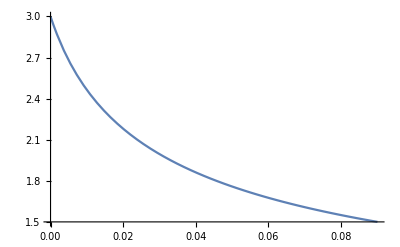

```mathematica
z/.ndsol[[1]]
Plot[%[r],{r,0,0.09},PlotRange->All]
```

Hmm doesn’t seem right, we are not actually solving dynamics here, also there is a cusp at r = 0, we probably do need to include the measure factor of r^2?

Also won’t work since getting rid of the cusp at r = 0 involve setting z’[0] = 0 which isn’t satisfied by the constraint, only satisfied at infinity and at the horizon for nonzero prr

so to fix this it seems we need to include r^2 from the measure, that way prr isn't conserved in the lagrangian, and it can take on the value of 0 at the centre of the bubble and go to 1 at the horizon

Wait hold on, this is the flux in r. The thing that is conserved is the 0th component integrated over the bubble, which is a scalar. we should find that, spherical symmetry implies this will only be a function of r (up to angular volume factors). However, doing the same for procedure above for time will give the energy density of the bubble, which we can integrate over r to find the energy

#### dynamic case

***** made a mistake here, wrong sign in kinetic, and used metric instead of inverse metric there

```mathematica
smg=l^4/z^4 Sqrt[(1-z^4/zh^4)+l^4/z^4(drz^2+dtz^2)]
pr = D[smg,drz]
pt = D[smg,dtz]
```

(l^4 √(1+((drz^2+dtz^2) l^4)/z^4-z^4/zh^4))/z^4

(drz l^8)/(z^8 √(1+((drz^2+dtz^2) l^4)/z^4-z^4/zh^4))

(dtz l^8)/(z^8 √(1+((drz^2+dtz^2) l^4)/z^4-z^4/zh^4))

```mathematica
zrepl= {z->z[t,r],dtz->D[z[t,r],t],drz->D[z[t,r],r]};
pr/.zrepl
pt/.zrepl
Simplify[D[smg,z]]/.zrepl
```

(l^8 z^(0,1)[t,r])/(z[t,r]^8 √(1-z[t,r]^4/zh^4+(l^4 ((z^(0,1)[t,r])^2+(z^(1,0)[t,r])^2))/z[t,r]^4))

(l^8 z^(1,0)[t,r])/(z[t,r]^8 √(1-z[t,r]^4/zh^4+(l^4 ((z^(0,1)[t,r])^2+(z^(1,0)[t,r])^2))/z[t,r]^4))

(2 l^4 (-2 zh^4 z[t,r]^4+z[t,r]^8-3 l^4 zh^4 ((z^(0,1)[t,r])^2+(z^(1,0)[t,r])^2)))/(zh^4 z[t,r]^9 √(1-z[t,r]^4/zh^4+(l^4 ((z^(0,1)[t,r])^2+(z^(1,0)[t,r])^2))/z[t,r]^4))

Need to decide if we should include the r measure factor. If not then the rhs of EL equations is equal to zero since the coordinates are cyclic.
**** consult goldstein
**** nah do luke notes instead

**** also we are doing this wrong, we need to solve for the energy momentum tensor. then write down conservation equation

also if we go back to probe brane rs notes, and take a conformal potential for the z on the brane, then we get a wave equation in the coordinates I think

no we get just blackening factor + kinetic term under the radical, which we can solve either in the near horizon limit, or with some other fancy wizardry

```mathematica
Simplify[pt dtz - smg]/.zrepl
```

(l^4 (-zh^4 z[t,r]^4+z[t,r]^8-l^4 zh^4 (z^(0,1)[t,r])^2))/(zh^4 z[t,r]^8 √(1-z[t,r]^4/zh^4+(l^4 ((z^(0,1)[t,r])^2+(z^(1,0)[t,r])^2))/z[t,r]^4))

fixing action and taking conformal tension **** check

**** this is not how the blackening factor appears in the inverse metric

```mathematica
smg=Sqrt[(1-z^4/zh^4)+(drz^2-(1-z^4/zh^4)^-1 dtz^2)]
pr = D[smg,drz]
pt = D[smg,dtz]
```

√(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4)

drz/(√(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4))

-dtz/((1-z^4/zh^4) √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4))

#### static case with expansions

```mathematica
smg=l^4/z^4 Sqrt[(1-z^4/zh^4)+drz^2]/.zrepl
smgnearhorizon=Series[%/.z[t,r]-> zh + R1 ϵ[r]+R2 ϵ[r]^2,{ϵ[r],0,2}]
%/.ϵ[r]->ρs-r
```

(l^4 √(1-z[t,r]^4/zh^4+(z^(0,1)[t,r])^2))/z[t,r]^4

(l^4 √((z^(0,1)[t,r])^2))/zh^4-(2 (l^4 R1 (1+2 (z^(0,1)[t,r])^2)) ϵ[r])/(zh^5 √((z^(0,1)[t,r])^2))+(l^4 (-2 R1^2+5 R1^2 (z^(0,1)[t,r])^2-2 R2 zh (z^(0,1)[t,r])^2+10 R1^2 (z^(0,1)[t,r])^4-4 R2 zh (z^(0,1)[t,r])^4) ϵ[r]^2)/(zh^6 ((z^(0,1)[t,r])^2)^(3/2))+O[ϵ[r]]^3

SeriesData::sdatv: First argument -r+ρs is not a valid variable.

(l^4 √((z^(0,1)[t,r])^2))/zh^4-(2 (l^4 R1 (1+2 (z^(0,1)[t,r])^2)) (-r+ρs))/(zh^5 √((z^(0,1)[t,r])^2))+(l^4 (-2 R1^2+5 R1^2 (z^(0,1)[t,r])^2-2 R2 zh (z^(0,1)[t,r])^2+10 R1^2 (z^(0,1)[t,r])^4-4 R2 zh (z^(0,1)[t,r])^4) (-r+ρs)^2)/(zh^6 ((z^(0,1)[t,r])^2)^(3/2))+O[-r+ρs]^3

```mathematica
smg=l^4/z^4 Sqrt[(1-z^4/zh^4)+drz^2]
Simplify[Series[(%/.{z-> zh + R1 ϵ+R2 ϵ^2,drz->-R1+-2 R2 ϵ}),{ϵ,0,2}]]
```

(l^4 √(1+drz^2-z^4/zh^4))/z^4

(l^4 √(R1^2))/zh^4-(2 (l^4 (R1+2 R1^3-R1 R2 zh)) ϵ)/(√(R1^2) zh^5)+(l^4 (-2+10 R1^4+2 R2 zh+R1^2 (5-12 R2 zh)) ϵ^2)/(√(R1^2) zh^6)+O[ϵ]^3

```mathematica
smg
pr = D[%,drz]
D[smg,z]
Series[D[pr/.{z-> zh + R1 ϵ+R2 ϵ^2,drz->-R1+-2 R2 ϵ},ϵ],{R2,0,1}]
D[smg,z]/.{z-> zh + R1 ϵ+R2 ϵ^2,drz->-R1+-2 R2 ϵ}
lhsEL = CoefficientList[Normal[Series[Simplify[D[pr/.{z-> zh + R1 ϵ+R2 ϵ^2,drz->-R1-2 R2 ϵ},ϵ]],{ϵ,0,2}]],ϵ]
rhsEL =CoefficientList[Normal[Series[Simplify[D[smg,z]/.{z-> zh + R1 ϵ+R2 ϵ^2,drz->-R1-2 R2 ϵ}],{ϵ,0,2}]],ϵ]
```

(l^4 √(1+drz^2-z^4/zh^4))/z^4

(drz l^4)/(z^4 √(1+drz^2-z^4/zh^4))

-(4 l^4 √(1+drz^2-z^4/zh^4))/z^5-(2 l^4)/(z √(1+drz^2-z^4/zh^4) zh^4)

(-(2 l^4 R1^2)/(zh^4 (zh+R1 ϵ) (-(R1 (-R1 zh^4+4 zh^3 ϵ+6 R1 zh^2 ϵ^2+4 R1^2 zh ϵ^3+R1^3 ϵ^4))/zh^4)^(3/2))+(4 l^4 R1^2)/((zh+R1 ϵ)^5 √(-(R1 (-R1 zh^4+4 zh^3 ϵ+6 R1 zh^2 ϵ^2+4 R1^2 zh ϵ^3+R1^3 ϵ^4))/zh^4)))+(2 l^4 (6 R1 zh^9 ϵ+4 R1^3 zh^9 ϵ-6 zh^8 ϵ^2-19 R1^2 zh^8 ϵ^2-6 R1^4 zh^8 ϵ^2+84 R1 zh^7 ϵ^3+20 R1^3 zh^7 ϵ^3+190 R1^2 zh^6 ϵ^4+65 R1^4 zh^6 ϵ^4+96 R1^3 zh^5 ϵ^5+56 R1^5 zh^5 ϵ^5-161 R1^4 zh^4 ϵ^6+16 R1^6 zh^4 ϵ^6-288 R1^5 zh^3 ϵ^7-201 R1^6 zh^2 ϵ^8-70 R1^7 zh ϵ^9-10 R1^8 ϵ^10) R2)/((zh+R1 ϵ)^6 (R1 zh^4-4 zh^3 ϵ-6 R1 zh^2 ϵ^2-4 R1^2 zh ϵ^3-R1^3 ϵ^4)^2 √((R1 (R1 zh^4-4 zh^3 ϵ-6 R1 zh^2 ϵ^2-4 R1^2 zh ϵ^3-R1^3 ϵ^4))/zh^4))+O[R2]^2

-(2 l^4)/(zh^4 (zh+R1 ϵ+R2 ϵ^2) √(1+(-R1-2 R2 ϵ)^2-((zh+R1 ϵ+R2 ϵ^2)^4)/zh^4))-(4 l^4 √(1+(-R1-2 R2 ϵ)^2-((zh+R1 ϵ+R2 ϵ^2)^4)/zh^4))/((zh+R1 ϵ+R2 ϵ^2)^5)

{(2 l^4 (-R1^2+2 R1^4))/((R1^2)^(3/2) zh^5),(2 l^4 (-6+5 R1^2-10 R1^4+6 R2 zh+4 R1^2 R2 zh))/(R1 √(R1^2) zh^6),-(6 l^4 (10-3 R1^2+5 R1^4-10 R1^6-18 R2 zh+5 R1^2 R2 zh+10 R1^4 R2 zh+8 R2^2 zh^2))/((R1^2)^(3/2) zh^7)}

{-(2 l^4 (1+2 R1^2))/(√(R1^2) zh^5),-(2 l^4 (2-5 R1^2-10 R1^4-2 R2 zh+4 R1^2 R2 zh))/(R1 √(R1^2) zh^6),-(2 l^4 (6-3 R1^2+15 R1^4+30 R1^6-10 R2 zh+5 R1^2 R2 zh-30 R1^4 R2 zh+4 R2^2 zh^2))/((R1^2)^(3/2) zh^7)}

```mathematica
Solve[lhsEL[[1]]==rhsEL[[1]],R1]
```

{}

```mathematica
lhsEL[[1]]==rhsEL[[1]]
Simplify[lhsEL[[1]]==rhsEL[[1]]]
```

(2 l^4 (-R1^2+2 R1^4))/((R1^2)^(3/2) zh^5)==-(2 l^4 (1+2 R1^2))/(√(R1^2) zh^5)

(l √(R1^2))/zh==0

```mathematica
lhsEL[[2]]==rhsEL[[2]]/.R1->0
Simplify[%]
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ComplexInfinity==ComplexInfinity

ComplexInfinity==ComplexInfinity

```mathematica
zrepl
```

{z→z[t,r],dtz→z^(1,0)[t,r],drz→z^(0,1)[t,r]}

```mathematica
staticrdepsmg = smg/.{z -> z[ r],  drz -> z'[r]}
pr = D[staticrdepsmg,D[z[r],r]]
lhsEL=Simplify[D[pr,r]]
rhsEL = Simplify[D[staticrdepsmg,r]]
```

(l^4 √(1-z[r]^4/zh^4+z'[r]^2))/z[r]^4

(l^4 z'[r])/(z[r]^4 √(1-z[r]^4/zh^4+z'[r]^2))

(l^4 ((-4 zh^4+6 z[r]^4) z'[r]^2-4 zh^4 z'[r]^4+z[r] (zh^4-z[r]^4) z''[r]))/(z[r]^5 √(1-z[r]^4/zh^4+z'[r]^2) (-z[r]^4+zh^4 (1+z'[r]^2)))

(l^4 z'[r] (2 z[r]^4-4 zh^4 (1+z'[r]^2)+zh^4 z[r] z''[r]))/(zh^4 z[r]^5 √(1-z[r]^4/zh^4+z'[r]^2))

```mathematica
Simplify[(lhsEL-rhsEL) (z[r]^5 Sqrt[1-z[r]^4/zh^4+z'[r]^2])/l^4(-zh^4 z[r]^4+zh^8 (1+z'[r]^2))](*this = 0 is eom, factor out nonsingular numerators*)
coffs=CoefficientList[Series[Simplify[%/.{z[r]-> zh + R1 ϵ+R2 ϵ^2,z'[r]->-R1-2 R2 ϵ+3 R3 ϵ^2,z''[r]->2 R2 + 6 R3 ϵ -12 }],{ϵ,0,2}],ϵ] (*ϵ is rstar - r*)
Solve[coffs[[1]]==0,R1];
R1sol=%[[3]](*vanishing R1 leads to singularity, so take non zero one*)
```

(-4 zh^8+6 zh^4 z[r]^4) z'[r]^2-4 zh^8 z'[r]^4+4 zh^8 z'[r]^5+zh^4 z[r] (zh^4-z[r]^4) z''[r]-(zh^4-z[r]^4) z'[r] (-4 zh^4+2 z[r]^4+zh^4 z[r] z''[r])-z'[r]^3 (-8 zh^8+6 zh^4 z[r]^4+zh^8 z[r] z''[r])

{2 R1^2 zh^8-4 R1^4 zh^8-4 R1^5 zh^8+R1^3 (-2 zh^8+2 (-6+R2) zh^9),-2 (-4 R1^2 zh^7-12 R1^3 zh^7-12 R1^4 zh^7-24 R1 zh^8-24 R1^2 zh^8+6 R1^4 zh^8+10 R1^2 R2 zh^8+16 R1^3 R2 zh^8+19 R1^4 R2 zh^8+36 R1^2 R2 zh^9-6 R1^2 R2^2 zh^9-3 R1^3 R3 zh^9),2 (-10 R1^3 zh^6+18 R1^4 zh^6+18 R1^5 zh^6+60 R1^2 zh^7+60 R1^3 zh^7+12 R1 R2 zh^7+50 R1^2 R2 zh^7+74 R1^3 R2 zh^7+24 R2 zh^8+72 R1 R2 zh^8-42 R1^3 R2 zh^8-24 R1 R2^2 zh^8-48 R1^2 R2^2 zh^8-73 R1^3 R2^2 zh^8-18 R1 R3 zh^8-3 R1^2 R3 zh^8+24 R1^3 R3 zh^8+33 R1^4 R3 zh^8-72 R1 R2^2 zh^9+12 R1 R2^3 zh^9+54 R1^2 R3 zh^9+9 R1^2 R2 R3 zh^9)}

{R1→-1/3+(8+144 zh-24 R2 zh)/(6 2^(2/3) (-1024-1728 zh+288 R2 zh+√(4 (8+144 zh-24 R2 zh)^3+(-1024-1728 zh+288 R2 zh)^2))^(1/3))-((-1024-1728 zh+288 R2 zh+√(4 (8+144 zh-24 R2 zh)^3+(-1024-1728 zh+288 R2 zh)^2))^(1/3))/(12 2^(1/3))}

```mathematica
Simplify[(coffs[[2]]/.R1sol)==0]
(*Solve[(coffs[[2]]/.R1sol)==0,R2];*)
(*R1sol=%[[3]](*vanishing R1 leads to singularity, so take non zero one*)*)
```

1/24 zh^7 (-16-(8 2^(2/3) (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))-8 2^(1/3) (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3)) (-4/3+16 zh+(10 R2 zh)/3+12 R2 zh^2-2 R2^2 zh^2-(2 2^(2/3) (-1+3 (-6+R2) zh))/(3 (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))-(4 2^(2/3) zh (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))+(5 2^(2/3) R2 zh (-1+3 (-6+R2) zh))/(3 (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))+(6 2^(2/3) R2 zh^2 (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))-(2^(2/3) R2^2 zh^2 (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))-2/3 2^(1/3) (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3)-4 2^(1/3) zh (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3)+5/3 2^(1/3) R2 zh (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3)+6 2^(1/3) R2 zh^2 (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3)-2^(1/3) R2^2 zh^2 (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3)+1/3 (2+(2^(2/3) (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))+2^(1/3) (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))^2-4/9 R2 zh (2+(2^(2/3) (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))+2^(1/3) (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))^2+1/12 R3 zh^2 (2+(2^(2/3) (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))+2^(1/3) (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))^2-1/18 (2+(2^(2/3) (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))+2^(1/3) (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))^3+1/36 zh (2+(2^(2/3) (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))+2^(1/3) (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))^3+19/216 R2 zh (2+(2^(2/3) (-1+3 (-6+R2) zh))/((-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))+2^(1/3) (-32-54 zh+9 R2 zh+1/16 √((8-24 (-6+R2) zh)^3+256 (32-9 (-6+R2) zh)^2))^(1/3))^3)==0

```mathematica
Denominator[%331]
```

-zh^4 z[r]^4+zh^8 (1+z'[r]^2)

#### Straight eom no weirdness

```mathematica
sqrtmg = Sqrt[(1-z^4/zh^4)+(drz^2-(1-z^4/zh^4)^-1 dtz^2)]
L = Vb[z]/z^4 sqrtmg
```

√(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4)

(√(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4) Vb[z])/z^4

```mathematica
lhs =D[L,z]/.zrepl
pr = D[L,drz]/.zrepl
pt = D[L,dtz]/.zrepl
```

(Vb[z[t,r]] (-(4 z[t,r]^3)/zh^4-(4 z[t,r]^3 (z^(1,0)[t,r])^2)/(zh^4 (1-z[t,r]^4/zh^4)^2)))/(2 z[t,r]^4 √(1-z[t,r]^4/zh^4+(z^(0,1)[t,r])^2-((z^(1,0)[t,r])^2)/(1-z[t,r]^4/zh^4)))-(4 Vb[z[t,r]] √(1-z[t,r]^4/zh^4+(z^(0,1)[t,r])^2-((z^(1,0)[t,r])^2)/(1-z[t,r]^4/zh^4)))/z[t,r]^5+(Vb'[z[t,r]] √(1-z[t,r]^4/zh^4+(z^(0,1)[t,r])^2-((z^(1,0)[t,r])^2)/(1-z[t,r]^4/zh^4)))/z[t,r]^4

(Vb[z[t,r]] z^(0,1)[t,r])/(z[t,r]^4 √(1-z[t,r]^4/zh^4+(z^(0,1)[t,r])^2-((z^(1,0)[t,r])^2)/(1-z[t,r]^4/zh^4)))

-(Vb[z[t,r]] z^(1,0)[t,r])/(z[t,r]^4 (1-z[t,r]^4/zh^4) √(1-z[t,r]^4/zh^4+(z^(0,1)[t,r])^2-((z^(1,0)[t,r])^2)/(1-z[t,r]^4/zh^4)))

```mathematica
rhs = (D[pr,r] +D[pt,t]) ;
Simplify[rhs==lhs]
```

(z[t,r] (zh^4-z[t,r]^4) Vb'[z[t,r]] (z[t,r]^8-zh^4 z[t,r]^4 (2+(z^(0,1)[t,r])^2)+zh^8 (1+(z^(0,1)[t,r])^2-(z^(1,0)[t,r])^2))+Vb[z[t,r]] (-8 zh^4 z[t,r]^8+2 z[t,r]^12-zh^4 z[t,r]^9 z^(0,2)[t,r]-4 zh^12 (1+(z^(0,1)[t,r])^2-(z^(1,0)[t,r])^2)+2 zh^8 z[t,r]^4 (5+2 (z^(0,1)[t,r])^2+(z^(1,0)[t,r])^2)+zh^8 z[t,r]^5 (2 z^(0,2)[t,r]-z^(2,0)[t,r])+zh^12 z[t,r] (z^(0,2)[t,r] (-1+(z^(1,0)[t,r])^2)-2 z^(0,1)[t,r] z^(1,0)[t,r] z^(1,1)[t,r]+z^(2,0)[t,r]+(z^(0,1)[t,r])^2 z^(2,0)[t,r])))/(zh z[t,r] √(1-z[t,r]^4/zh^4+(z^(0,1)[t,r])^2-((z^(1,0)[t,r])^2)/(1-z[t,r]^4/zh^4)) (z[t,r]^8-zh^4 z[t,r]^4 (2+(z^(0,1)[t,r])^2)+zh^8 (1+(z^(0,1)[t,r])^2-(z^(1,0)[t,r])^2)))==0

#### asymptotic ads limit (away from horizon)

as a starting point we can simplify by taking constant tension on the brane (as in pujolas) and then

```mathematica
Limit[rhs /. {Vb[z[t,r]]->σ,Vb'[z[t,r]]->0},zh->∞]
Limit[lhs/. {Vb[z[t,r]]->σ,Vb'[z[t,r]]->0},zh->∞]
```

-((σ (4 (z^(0,1)[t,r])^4+4 (z^(1,0)[t,r])^2 (-1+(z^(1,0)[t,r])^2)-2 z[t,r] z^(0,1)[t,r] z^(1,0)[t,r] z^(1,1)[t,r]+z[t,r] (z^(0,2)[t,r] (-1+(z^(1,0)[t,r])^2)+z^(2,0)[t,r])+(z^(0,1)[t,r])^2 (4-8 (z^(1,0)[t,r])^2+z[t,r] z^(2,0)[t,r])))/(z[t,r]^5 (1+(z^(0,1)[t,r])^2-(z^(1,0)[t,r])^2)^(3/2)))

-(4 σ √(1+(z^(0,1)[t,r])^2-(z^(1,0)[t,r])^2))/z[t,r]^5

do the same starting from the limit in the lagrangian

```mathematica
sqrtmg = Sqrt[1+(drz^2-dtz^2)]
L = σ/z^4 sqrtmg
```

√(1+drz^2-dtz^2)

(√(1+drz^2-dtz^2) σ)/z^4

```mathematica
lhs =D[L,z]/.zrepl
pr = D[L,drz]/.zrepl
pt = D[L,dtz]/.zrepl
```

-(4 σ √(1+(z^(0,1)[t,r])^2-(z^(1,0)[t,r])^2))/z[t,r]^5

(σ z^(0,1)[t,r])/(z[t,r]^4 √(1+(z^(0,1)[t,r])^2-(z^(1,0)[t,r])^2))

-(σ z^(1,0)[t,r])/(z[t,r]^4 √(1+(z^(0,1)[t,r])^2-(z^(1,0)[t,r])^2))

```mathematica
rhs = (D[pr,r] +D[pt,t]) ;
Simplify[rhs==lhs]
```

(σ (4 (-1+(z^(1,0)[t,r])^2)-2 z[t,r] z^(0,1)[t,r] z^(1,0)[t,r] z^(1,1)[t,r]+z[t,r] (z^(0,2)[t,r] (-1+(z^(1,0)[t,r])^2)+z^(2,0)[t,r])+(z^(0,1)[t,r])^2 (-4+z[t,r] z^(2,0)[t,r])))/(z[t,r] (1+(z^(0,1)[t,r])^2-(z^(1,0)[t,r])^2)^(3/2))==0

#### energy momentum tensor (maybe!)

******** also need ot check if it is minkowski or spacetime metric we need to use!

```mathematica
gμν = DiagonalMatrix[{-1,1,1,1}] (*minkowski metric*)
Πdz = Outer[Times,{pt,pr,0,0},{dtz,drz,0,0}] (*first term in the legendre transform of our lagrangian*)
```

{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

{{-(dtz^2 Vb[z])/(z^4 (1-z^4/zh^4) √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4)),-(drz dtz Vb[z])/(z^4 (1-z^4/zh^4) √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4)),0,0},{(drz dtz Vb[z])/(z^4 √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4)),(drz^2 Vb[z])/(z^4 √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4)),0,0},{0,0,0,0},{0,0,0,0}}

**** need to check sign because of our metric convention

```mathematica
gμν = DiagonalMatrix[{-1,1,1,1}] (*minkowski metric*)
Πdz = Outer[Times,{pt,pr,0,0},{dtz,drz,0,0}]
```

```mathematica
Tμν = Πdz + gμν L;  (*energy momentum tensor*)
MatrixForm[%]
```

(-(dtz^2 Vb[z])/(z^4 (1-z^4/zh^4) √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4))-(√(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4) Vb[z])/z^4 | -(drz dtz Vb[z])/(z^4 (1-z^4/zh^4) √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4)) | 0 | 0
(drz dtz Vb[z])/(z^4 √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4)) | (drz^2 Vb[z])/(z^4 √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4))+(√(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4) Vb[z])/z^4 | 0 | 0
0 | 0 | (√(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4) Vb[z])/z^4 | 0
0 | 0 | 0 | (√(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4) Vb[z])/z^4)

#### t(r,z)=ξ(r)+z/v

```mathematica
L = r^2 l^4/z^4 Sqrt[-1/(1-z^4/zh^4)+drξ^2+(1-z^4/zh^4)dzt^2]
```

(l^4 r^2 √(drξ^2-1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4)))/z^4

```mathematica
ξrepl ={drξ->ξ'[r],dzt->1/v}
```

{drξ→ξ'[r],dzt→1/v}

```mathematica
pz =D[L,dzt]/.ξrepl
pr = D[L,drξ]/.ξrepl
```

(l^4 r^2 (1-z^4/zh^4))/(v z^4 √(-1/(1-z^4/zh^4)+(1-z^4/zh^4)/v^2+ξ'[r]^2))

(l^4 r^2 ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+(1-z^4/zh^4)/v^2+ξ'[r]^2))

```mathematica
sol=Solve[D[pz,z]+D[pr,r]==0,ξ''[r]]
ξ2der=Simplify[ξ''[r]/.sol[[1]]]
```

{{ξ''[r]→((l^4 r^2 (1-z^4/zh^4) (-(4 z^3)/(v^2 zh^4)-(4 z^3)/((1-z^4/zh^4)^2 zh^4)))/(2 v z^4 (-1/(1-z^4/zh^4)+(1-z^4/zh^4)/v^2+ξ'[r]^2)^(3/2))+(4 l^4 r^2 (1-z^4/zh^4))/(v z^5 √(-1/(1-z^4/zh^4)+(1-z^4/zh^4)/v^2+ξ'[r]^2))+(4 l^4 r^2)/(v z zh^4 √(-1/(1-z^4/zh^4)+(1-z^4/zh^4)/v^2+ξ'[r]^2))-(2 l^4 r ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+(1-z^4/zh^4)/v^2+ξ'[r]^2)))/(-(l^4 r^2 ξ'[r]^2)/(z^4 (-1/(1-z^4/zh^4)+(1-z^4/zh^4)/v^2+ξ'[r]^2)^(3/2))+(l^4 r^2)/(z^4 √(-1/(1-z^4/zh^4)+(1-z^4/zh^4)/v^2+ξ'[r]^2)))}}

(2 (r (z^12-4 z^8 zh^4+(5+v^2) z^4 zh^8+2 (-1+v^2) zh^12)+v z zh^4 (z^8-2 z^4 zh^4-(-1+v^2) zh^8) ξ'[r]+2 r v^2 zh^8 (z^4-zh^4) ξ'[r]^2+v^3 z zh^8 (-z^4+zh^4) ξ'[r]^3))/(r v z zh^4 (-z^8+2 z^4 zh^4+(-1+v^2) zh^8))

```mathematica
truncedξ2der=Normal[Series[ξ2der,{ξ'[r],0,1}]]
DSolve[ξ''[r]==%,ξ[r],r]
```

(2 (z^12-4 z^8 zh^4+(5+v^2) z^4 zh^8+2 (-1+v^2) zh^12))/(v z zh^4 (-z^8+2 z^4 zh^4+(-1+v^2) zh^8))-(2 ξ'[r])/r

{{ξ[r]→(r^2 (z^12-4 z^8 zh^4+5 z^4 zh^8+v^2 z^4 zh^8-2 zh^12+2 v^2 zh^12))/(3 v z zh^4 (-z^8+2 z^4 zh^4-zh^8+v^2 zh^8))-C[1]/r+C[2]}}

```mathematica
DSolve[ξ''[r]==Normal[Series[ξ2der,{ξ'[r],0,2}]],ξ[r],r]
```

{{ξ[r]→C[2]-(z (z^8-2 z^4 zh^4-(-1+v^2) zh^8) (Log[r]-Log[Cos[(2 √2 r v zh^4 (-z^4+zh^4) √(-(z^12-4 z^8 zh^4+(5+v^2) z^4 zh^8+2 (-1+v^2) zh^12)/(v^2 zh^8 (-z^4+zh^4)))+z (z^8-2 z^4 zh^4-(-1+v^2) zh^8) C[1])/(z^9-2 z^5 zh^4-(-1+v^2) z zh^8)]]))/(4 v zh^4 (z^4-zh^4))}}

```mathematica
DSolve[ξ''[r]==ξ2der,ξ[r],r]
```

DSolve[ξ''[r]==(2 (r (z^12-4 z^8 zh^4+(5+v^2) z^4 zh^8+2 (-1+v^2) zh^12)+v z zh^4 (z^8-2 z^4 zh^4-(-1+v^2) zh^8) ξ'[r]+2 r v^2 zh^8 (z^4-zh^4) ξ'[r]^2+v^3 z zh^8 (-z^4+zh^4) ξ'[r]^3))/(r v z zh^4 (-z^8+2 z^4 zh^4+(-1+v^2) zh^8)),ξ[r],r]

#### find the metric for t(z,r)=ξ(r)+χ(z)

```mathematica
met = l^2/z^2{{-(1-z^4/zh^4) dzt dzt+1/(1-z^4/zh^4),-(1-z^4/zh^4) dzt drt,0,0},{-(1-z^4/zh^4) drt dzt,-(1-z^4/zh^4) drt drt  + 1 ,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
-Det[met]
Simplify[% z^8/(l^8 r^4 Sin[θ]^2)]
Simplify[%  /(drt^2 - 1/(1-z^4/zh^4) + (1-z^4/zh^4) dzt^2)]
```

((l^2 (1/(1-z^4/zh^4)+dzt^2 (-1+z^4/zh^4)))/z^2 | (drt dzt l^2 (-1+z^4/zh^4))/z^2 | 0 | 0
(drt dzt l^2 (-1+z^4/zh^4))/z^2 | (l^2 (1+drt^2 (-1+z^4/zh^4)))/z^2 | 0 | 0
0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

(dzt^2 l^8 r^4 Sin[θ]^2)/z^8-(l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))+(drt^2 l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))-(dzt^2 l^8 r^4 Sin[θ]^2)/(z^4 zh^4)-(drt^2 l^8 r^4 Sin[θ]^2)/(z^4 (1-z^4/zh^4) zh^4)

drt^2+dzt^2 (1-z^4/zh^4)+zh^4/(z^4-zh^4)

1

#### find eom for t(z,r)=ξ(r)+χ(z)

```mathematica
L = r^2 l^4/z^4 Sqrt[-1/(1-z^4/zh^4)+drt^2+(1-z^4/zh^4)dzt^2]
```

(l^4 r^2 √(drt^2-1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4)))/z^4

```mathematica
trepl ={drt->ξ'[r],dzt->χ'[z]}
```

{drt→ξ'[r],dzt→χ'[z]}

```mathematica
pz =D[L,dzt]/.trepl
pr = D[L,drt]/.trepl
```

(l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))

(l^4 r^2 ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))

```mathematica
D[pz,z]+D[pr,r]==0
```

(2 l^4 r ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))-(4 l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^5 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))-(4 l^4 r^2 χ'[z])/(z zh^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))-(l^4 r^2 ξ'[r]^2 ξ''[r])/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))+(l^4 r^2 ξ''[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(l^4 r^2 (1-z^4/zh^4) χ''[z])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))-(l^4 r^2 (1-z^4/zh^4) χ'[z] (-(4 z^3)/((1-z^4/zh^4)^2 zh^4)-(4 z^3 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) χ'[z] χ''[z]))/(2 z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))==0

```mathematica
sol=Solve[D[pz,z]+D[pr,r]==0,ξ''[r]]
ξ2der=Simplify[ξ''[r]/.sol[[1]]]
CoefficientList[ξ2der,ξ'[r]];
ξcoeffs=%/.{χ'[z]->1/v,χ''[z]->0}
%%/.zh->Subscript[z, h]
```

{{ξ''[r]→(-(2 l^4 r ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^5 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 χ'[z])/(z zh^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))-(l^4 r^2 (1-z^4/zh^4) χ''[z])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(l^4 r^2 (1-z^4/zh^4) χ'[z] (-(4 z^3)/((1-z^4/zh^4)^2 zh^4)-(4 z^3 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) χ'[z] χ''[z]))/(2 z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2)))/(-(l^4 r^2 ξ'[r]^2)/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))+(l^4 r^2)/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)))}}

-1/(r z zh^4 (-zh^8+(z^4-zh^4)^2 χ'[z]^2))(2 z zh^8 (-z^4+zh^4) ξ'[r]^3+2 z zh^4 ξ'[r] (-zh^8+(z^4-zh^4)^2 χ'[z]^2)+r zh^4 (z^4-zh^4) ξ'[r]^2 (4 zh^4 χ'[z]+z (z^4-zh^4) χ''[z])+r (2 zh^8 (z^4+2 zh^4) χ'[z]+2 (z^4-2 zh^4) (z^4-zh^4)^2 χ'[z]^3+z zh^8 (z^4-zh^4) χ''[z]))

{-((2 (z^4-2 zh^4) (z^4-zh^4)^2)/v^3+(2 zh^8 (z^4+2 zh^4))/v)/(z zh^4 (-zh^8+((z^4-zh^4)^2)/v^2)),-2/r,-(4 zh^4 (z^4-zh^4))/(v z (-zh^8+((z^4-zh^4)^2)/v^2)),-(2 zh^4 (-z^4+zh^4))/(r (-zh^8+((z^4-zh^4)^2)/v^2))}

{-(2 z_h^8 (z^4+2 z_h^4) χ'[z]+2 (z^4-2 z_h^4) (z^4-z_h^4)^2 χ'[z]^3+z z_h^8 (z^4-z_h^4) χ''[z])/(z z_h^4 (-z_h^8+(z^4-z_h^4)^2 χ'[z]^2)),-2/r,-((z^4-z_h^4) (4 z_h^4 χ'[z]+z (z^4-z_h^4) χ''[z]))/(z (-z_h^8+(z^4-z_h^4)^2 χ'[z]^2)),-(2 z_h^4 (-z^4+z_h^4))/(r (-z_h^8+(z^4-z_h^4)^2 χ'[z]^2))}

```mathematica
sol=Solve[D[pz,z]+D[pr,r]==0,χ''[z]]
χ2der=Simplify[χ''[z]/.sol[[1]]]
Simplify[CoefficientList[χ2der,χ'[z]]]
```

{{χ''[z]→(-(2 l^4 r^2 χ'[z])/(z (1-z^4/zh^4) zh^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(2 l^4 r^2 (1-z^4/zh^4) χ'[z]^3)/(z zh^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(2 l^4 r ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^5 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 χ'[z])/(z zh^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(l^4 r^2 ξ'[r]^2 ξ''[r])/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(l^4 r^2 ξ''[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)))/(-(l^4 r^2 (1-z^4/zh^4)^2 χ'[z]^2)/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))+(l^4 r^2 (1-z^4/zh^4))/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)))}}

1/(r z zh^4 (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2))(2 z zh^8 (z^4-zh^4) ξ'[r]^3+4 r zh^8 (-z^4+zh^4) ξ'[r]^2 χ'[z]-2 z zh^4 ξ'[r] (-zh^8+(z^4-zh^4)^2 χ'[z]^2)-r (2 zh^8 (z^4+2 zh^4) χ'[z]+2 (z^4-2 zh^4) (z^4-zh^4)^2 χ'[z]^3-z zh^12 ξ''[r]+z zh^4 (z^4-zh^4)^2 χ'[z]^2 ξ''[r]))

{(2 zh^8 ξ'[r]+2 zh^4 (z^4-zh^4) ξ'[r]^3+r zh^8 ξ''[r])/(r (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2)),-(2 zh^4 (z^4+2 zh^4+2 (z^4-zh^4) ξ'[r]^2))/(z (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2)),((z^4-zh^4) (2 ξ'[r]+r ξ''[r]))/(r (-zh^4+(-z^4+zh^4) ξ'[r]^2)),-(2 (z^8-3 z^4 zh^4+2 zh^8))/(z zh^4 (zh^4+(z^4-zh^4) ξ'[r]^2))}

#### find eom for t(z,r)=ξ(r)+χ(z) using M auxiliary measure variable

```mathematica
Clear[zh]
f[z_]:=(1-z^4/zh^4)
L = r^2 l^4/z^4 Sqrt[-1/f[z]+drt^2+f[z] dzt^2]
```

(l^4 r^2 √(drt^2-1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4)))/z^4

```mathematica
trepl ={drt->ξ'[r],dzt->χ'[z]}
D[L,dzt]/.trepl
D[L,drt]/.trepl
```

{drt→ξ'[r],dzt→χ'[z]}

(l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))

(l^4 r^2 ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))

```mathematica
Clear[pr,pz]
pz = (l^4 r^2 f[z]dzt)/(z^4 M[r,z])/.trepl
pr = (l^4 r^2 drt)/(z^4 M[r,z])/.trepl
```

(l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^4 M[r,z])

(l^4 r^2 ξ'[r])/(z^4 M[r,z])

```mathematica
dLdt = D[pz,z]+D[pr,r]
Simplify[(M[r,z] z^4)/(l^4 r^2)dLdt]
```

(2 l^4 r ξ'[r])/(z^4 M[r,z])-(4 l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^5 M[r,z])-(4 l^4 r^2 χ'[z])/(z zh^4 M[r,z])+(l^4 r^2 ξ''[r])/(z^4 M[r,z])+(l^4 r^2 (1-z^4/zh^4) χ''[z])/(z^4 M[r,z])-(l^4 r^2 (1-z^4/zh^4) χ'[z] M^(0,1)[r,z])/(z^4 M[r,z]^2)-(l^4 r^2 ξ'[r] M^(1,0)[r,z])/(z^4 M[r,z]^2)

ξ''[r]+χ''[z]-(z^4 χ''[z])/zh^4+χ'[z] (-4/z+((z^4-zh^4) M^(0,1)[r,z])/(zh^4 M[r,z]))+ξ'[r] (2/r-(M^(1,0)[r,z])/M[r,z])

#### find the metric for t(z,r)=ξ(r)+χ(z) in euclidean time

```mathematica
met = l^2/z^2{{(1-z^4/zh^4) dzt dzt+1/(1-z^4/zh^4),(1-z^4/zh^4) dzt drt,0,0},{(1-z^4/zh^4) drt dzt,(1-z^4/zh^4) drt drt  + 1 ,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
Det[met]
Simplify[% z^8/(l^8 r^4 Sin[θ]^2)]
Simplify[%  /(drt^2 + 1/(1-z^4/zh^4) + (1-z^4/zh^4) dzt^2)]
```

((l^2 (1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4)))/z^2 | (drt dzt l^2 (1-z^4/zh^4))/z^2 | 0 | 0
(drt dzt l^2 (1-z^4/zh^4))/z^2 | (l^2 (1+drt^2 (1-z^4/zh^4)))/z^2 | 0 | 0
0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

(dzt^2 l^8 r^4 Sin[θ]^2)/z^8+(l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))+(drt^2 l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))-(dzt^2 l^8 r^4 Sin[θ]^2)/(z^4 zh^4)-(drt^2 l^8 r^4 Sin[θ]^2)/(z^4 (1-z^4/zh^4) zh^4)

(zh^8+dzt^2 (z^4-zh^4)^2+drt^2 (-z^4 zh^4+zh^8))/(-z^4 zh^4+zh^8)

1

#### find eom for t(z,r)=ξ(r)+χ(z) using M auxiliary measure variable and euclidean time

```mathematica
Clear[zh]
f[z_]:=(1-z^4/zh^4)
Measure = Sqrt[1/f[z]+drt^2+f[z] dzt^2]
L = r^2 l^4/z^4 Measure
```

√(drt^2+1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4))

(l^4 r^2 √(drt^2+1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4)))/z^4

```mathematica
trepl ={drt->ξ'[r],dzt->χ'[z]}
D[L,dzt]/.trepl
D[L,drt]/.trepl
```

{drt→ξ'[r],dzt→χ'[z]}

(l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^4 √(1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))

(l^4 r^2 ξ'[r])/(z^4 √(1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))

```mathematica
Clear[pr,pz]
pz = (l^4 r^2 f[z]dzt)/(z^4 M[r,z])/.trepl
pr = (l^4 r^2 drt)/(z^4 M[r,z])/.trepl
```

(l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^4 M[r,z])

(l^4 r^2 ξ'[r])/(z^4 M[r,z])

```mathematica
dLdt = D[pz,z]+D[pr,r]
Simplify[(M[r,z] z^4)/(l^4 r^2)dLdt]
```

(2 l^4 r ξ'[r])/(z^4 M[r,z])-(4 l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^5 M[r,z])-(4 l^4 r^2 χ'[z])/(z zh^4 M[r,z])+(l^4 r^2 ξ''[r])/(z^4 M[r,z])+(l^4 r^2 (1-z^4/zh^4) χ''[z])/(z^4 M[r,z])-(l^4 r^2 (1-z^4/zh^4) χ'[z] M^(0,1)[r,z])/(z^4 M[r,z]^2)-(l^4 r^2 ξ'[r] M^(1,0)[r,z])/(z^4 M[r,z]^2)

ξ''[r]+χ''[z]-(z^4 χ''[z])/zh^4+χ'[z] (-4/z+((z^4-zh^4) M^(0,1)[r,z])/(zh^4 M[r,z]))+ξ'[r] (2/r-(M^(1,0)[r,z])/M[r,z])

```mathematica
Simplify[-ξ'[r]D[Log[Measure/.trepl],r]-χ'[z]f[z]D[Log[Measure/.trepl],z]]
```

(-2 z^3 zh^8 χ'[z]+2 z^3 (z^4-zh^4)^2 χ'[z]^3+zh^8 (z^4-zh^4) ξ'[r]^2 ξ''[r]+(z^4-zh^4)^3 χ'[z]^2 χ''[z])/(zh^4 (zh^8+(-z^4 zh^4+zh^8) ξ'[r]^2+(z^4-zh^4)^2 χ'[z]^2))

```mathematica
χsol=DSolve[f[z]χ''[z]-χ'[z] 4/z==Λ,χ[z],z][[1]]
ξsol=DSolve[ξ''[r]-ξ'[r] 2/r==-Λ,ξ[r],r][[1]]
```

{χ[z]→C[2]+1/12 (12 z C[1]-6 zh ArcTan[z/zh] C[1]+zh (zh Λ+3 C[1]) Log[-z+zh]+zh^2 Λ Log[z+zh]-3 zh C[1] Log[z+zh]-zh^2 Λ Log[z^2+zh^2])}

{ξ[r]→(r^2 Λ)/2+(r^3 C[1])/3+C[2]}

```mathematica
D[χsol,z]
```

{χ'[z]→1/12 ((zh^2 Λ)/(z+zh)-(2 z zh^2 Λ)/(z^2+zh^2)+12 C[1]-(6 C[1])/(1+z^2/zh^2)-(3 zh C[1])/(z+zh)-(zh (zh Λ+3 C[1]))/(-z+zh))}

Near horizon limit

```mathematica
PowerExpand[Series[Measure/.z->zh-ϵ/.trepl,{ϵ,0,1}]]
PowerExpand[Series[Measure/.z->zh-ϵ/.trepl,{ϵ,0,0}]]
MeasureNearHorizon = Normal[%]/.ϵ->zh-z
```

(√zh)/(2 √ϵ)+((3+8 ξ'[r]^2) √ϵ)/(8 √zh)+O[ϵ]^(3/2)

(√zh)/(2 √ϵ)+√O[ϵ]

(√zh)/(2 √(-z+zh))

far horizon limit

```mathematica
MeasureFarHorizon=Limit[Measure,zh->∞]/.trepl
D[Log[MeasureFarHorizon],r]
D[Log[MeasureFarHorizon],z]
```

√(1+ξ'[r]^2+χ'[z]^2)

(ξ'[r] ξ''[r])/(1+ξ'[r]^2+χ'[z]^2)

(χ'[z] χ''[z])/(1+ξ'[r]^2+χ'[z]^2)

```mathematica
Simplify[χsol/.C[1]->0]
```

{χ[z]→C[2]+1/12 zh^2 Λ (Log[-z+zh]+Log[z+zh]-Log[z^2+zh^2])}

```mathematica
Information[C]
```

```mathematica
D[Log[Measure]/.trepl,r]
D[Log[Measure]/.trepl,z]
```

(ξ'[r] ξ''[r])/(1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)

((4 z^3)/((1-z^4/zh^4)^2 zh^4)-(4 z^3 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) χ'[z] χ''[z])/(2 (1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))

try using the above near horizon expansion in the ODE

```mathematica
D[Log[MeasureNearHorizon],z]
χsol=DSolve[f[z]χ''[z]-χ'[z](4/z+%)==Λ,χ[z],z][[1]]
ξsol=DSolve[ξ''[r]-ξ'[r] 2/r==-Λ,ξ[r],r][[1]]
```

1/(2 (-z+zh))

{χ[z]→C[2]+(ⅇ^(1/16 (2 ArcTan[K[2]/zh]-(2 zh)/(-zh+K[2])+64 Log[K[2]]-19 Log[-zh+K[2]]-15 Log[zh+K[2]]-15 Log[zh^2+K[2]^2])) C[1]+ⅇ^(1/16 (2 ArcTan[K[2]/zh]-(2 zh)/(-zh+K[2])+64 Log[K[2]]-19 Log[-zh+K[2]]-15 Log[zh+K[2]]-15 Log[zh^2+K[2]^2])) (ⅇ^(1/16 (-2 ArcTan[K[1]/zh]+(2 zh)/(-zh+K[1])-64 Log[K[1]]+19 Log[-zh+K[1]]+15 Log[zh+K[1]]+15 Log[zh^2+K[1]^2])) (2 zh^5 Λ K[1]-2 zh^4 Λ K[1]^2))/(2 K[1] (-zh+K[1])^2 (zh^3+zh^2 K[1]+zh K[1]^2+K[1]^3))K[1]1K[2])K[2]1z}

{ξ[r]→(r^2 Λ)/2+(r^3 C[1])/3+C[2]}

we run into the same issue that for our ansatz to be consistent, we need the Measure to depend only on one of the coordinates, so this only works in the near and far horizon limits

we also have the issue of only being able to solve this with euclidean time evolution (as far as I can tell, maybe this isn’t true)

#### Ansatz for z

we can explicitly solve these equations if we choose a form for the seperated functions.

We motivate a choice for z and then find the profile and velocity in r and t. 

We expect that the bubble will eventually reach a terminal velocity so the evolution in z at terminal velocity so at late times

```mathematica
Integrate[Apart[1/(a + b y + c y^2+d y^3)],{y,y0,y1},Assumptions->{{a,b,c,d}∈Reals}]
```

$Aborted

```mathematica
Apart[1/(a + b y + c y^2+d y^3),y]
```

1/(a+b y+c y^2+d y^3)

```mathematica
Factor[a + b y + c y^2+d y^3]
```

a+b y+c y^2+d y^3

```mathematica
Roots[a + b y + c y^2+ y^3==0,y][[1]]
```

y==-c/3-(2^(1/3) (3 b-c^2))/(3 (-27 a+9 b c-2 c^3+3 √3 √(27 a^2+4 b^3-18 a b c-b^2 c^2+4 a c^3))^(1/3))+((-27 a+9 b c-2 c^3+3 √3 √(27 a^2+4 b^3-18 a b c-b^2 c^2+4 a c^3))^(1/3))/(3 2^(1/3))

#### crack at solving quartic polynomial ode

because of the time has a killing vector, the ode is secretly first order, the functions themselves don’t show up only their derivatives

```mathematica
DSolve[y'[x]==1 + 2 y[x] + 3 y[x]^2+ y[x]^3,y[x],x]
```

Solve[RootSum[1+2 #1+3 #1^2+#1^3&,Log[-#1+y[x]]/(2+6 #1+3 #1^2)&]==x+C[1],y[x]]

```mathematica
NIntegrate[1/(a + b y + c y^2+d y^3)/.{a->1,b->2,c->3,d->4},{y,0,3}]
```

0.449833

### Solving as r(t,z)

#### finding the measure

```mathematica
met = l^2/z^2{{ dzr dzr+1/(1-z^4/zh^4), dzr dtr,0,0},{dtr dzr , dtr dtr -(1-z^4/zh^4),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
-Det[met]
Simplify[% z^8/(l^8 r^4 Sin[θ]^2)]
Simplify[%  /(-1/(1-z^4/zh^4)dtr^2  +1 + (1-z^4/zh^4) dzr^2)]
```

((l^2 (dzr^2+1/(1-z^4/zh^4)))/z^2 | (dtr dzr l^2)/z^2 | 0 | 0
(dtr dzr l^2)/z^2 | (l^2 (-1+dtr^2+z^4/zh^4))/z^2 | 0 | 0
0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

-(l^4 r^4 (-(dtr^2 dzr^2 l^4)/z^4+(l^4 (dzr^2+1/(1-z^4/zh^4)) (-1+dtr^2+z^4/zh^4))/z^4) Sin[θ]^2)/z^4

(z^4 zh^4+(-1+dtr^2) zh^8-dzr^2 (z^4-zh^4)^2)/(zh^4 (z^4-zh^4))

1

#### finding eom

```mathematica
L = r^2 l^4/z^4 Sqrt[-1/(1-z^4/zh^4)dtr^2  +1 + (1-z^4/zh^4) dzr^2]
```

(l^4 r^2 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))/z^4

```mathematica
rrepl ={r->ξ[t]+χ[z],dtr->ξ'[t],dzr->χ'[z]}
```

{r→ξ[t]+χ[z],dtr→ξ'[t],dzr→χ'[z]}

```mathematica
D[L,dzr] dzr+D[L,dtr] dtr - L
```

-(l^4 r^2 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))/z^4-(dtr^2 l^4 r^2)/(z^4 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)) (1-z^4/zh^4))+(dzr^2 l^4 r^2 (1-z^4/zh^4))/(z^4 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))

```mathematica
pz =D[L,dzr]/.rrepl
pt = D[L,dtr]/.rrepl
dLdr = D[L,r]/.rrepl
```

(l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ'[z])/(z^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))

-(l^4 (ξ[t]+χ[z])^2 ξ'[t])/(z^4 (1-z^4/zh^4) √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))

(2 l^4 (ξ[t]+χ[z]) √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))/z^4

```mathematica
D[pz,z]+D[pt,r]==dLdr
```

-(4 l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ'[z])/(z^5 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))-(4 l^4 (ξ[t]+χ[z])^2 χ'[z])/(z zh^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(2 l^4 (1-z^4/zh^4) (ξ[t]+χ[z]) χ'[z]^2)/(z^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ''[z])/(z^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))-(l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ'[z] (-(4 z^3 ξ'[t]^2)/((1-z^4/zh^4)^2 zh^4)-(4 z^3 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) χ'[z] χ''[z]))/(2 z^4 (1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2)^(3/2))==(2 l^4 (ξ[t]+χ[z]) √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))/z^4

```mathematica
rsol=Solve[D[pz,z]+D[pt,t]==dLdr,ξ''[t]]
ξ2der=Simplify[ξ''[t]/.rsol[[1]]]
CoefficientList[ξ2der,ξ'[t]];
ξcoeffs=%/.{χ'[z]->1/v,χ''[z]->0};
%%/.zh->Subscript[z, h]
```

{{ξ''[t]→((2 l^4 (ξ[t]+χ[z]) ξ'[t]^2)/(z^4 (1-z^4/zh^4) √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ'[z])/(z^5 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 (ξ[t]+χ[z])^2 χ'[z])/(z zh^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))-(2 l^4 (1-z^4/zh^4) (ξ[t]+χ[z]) χ'[z]^2)/(z^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(2 l^4 (ξ[t]+χ[z]) √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))/z^4-(l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ''[z])/(z^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ'[z] (-(4 z^3 ξ'[t]^2)/((1-z^4/zh^4)^2 zh^4)-(4 z^3 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) χ'[z] χ''[z]))/(2 z^4 (1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2)^(3/2)))/(-(l^4 (ξ[t]+χ[z])^2 ξ'[t]^2)/(z^4 (1-z^4/zh^4)^2 (1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(l^4 (ξ[t]+χ[z])^2)/(z^4 (1-z^4/zh^4) √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2)))}}

-((zh^8 ξ'[t]^2 (2 z zh^4+ξ[t] (2 (z^4+2 zh^4) χ'[z]+z (z^4-zh^4) χ''[z])+χ[z] (2 (z^4+2 zh^4) χ'[z]+z (z^4-zh^4) χ''[z]))+(z^4-zh^4) (2 z zh^4 (zh^4+(-z^4+zh^4) χ'[z]^2)+ξ[t] (4 zh^8 χ'[z]+2 (z^8-3 z^4 zh^4+2 zh^8) χ'[z]^3+z zh^4 (z^4-zh^4) χ''[z])+χ[z] (4 zh^8 χ'[z]+2 (z^8-3 z^4 zh^4+2 zh^8) χ'[z]^3+z zh^4 (z^4-zh^4) χ''[z])))/(z zh^8 (ξ[t]+χ[z]) (-zh^4+(z^4-zh^4) χ'[z]^2)))

{-(((z^4-z_h^4) (2 z z_h^4 (z_h^4+(-z^4+z_h^4) χ'[z]^2)+ξ[t] (4 z_h^8 χ'[z]+2 (z^8-3 z^4 z_h^4+2 z_h^8) χ'[z]^3+z z_h^4 (z^4-z_h^4) χ''[z])+χ[z] (4 z_h^8 χ'[z]+2 (z^8-3 z^4 z_h^4+2 z_h^8) χ'[z]^3+z z_h^4 (z^4-z_h^4) χ''[z])))/(z z_h^8 (ξ[t]+χ[z]) (-z_h^4+(z^4-z_h^4) χ'[z]^2))),0,-((2 z z_h^4+ξ[t] (2 (z^4+2 z_h^4) χ'[z]+z (z^4-z_h^4) χ''[z])+χ[z] (2 (z^4+2 z_h^4) χ'[z]+z (z^4-z_h^4) χ''[z]))/(z (ξ[t]+χ[z]) (-z_h^4+(z^4-z_h^4) χ'[z]^2)))}

```mathematica
Solve[a + b y^2+c y^4==0,y]/.{a->1,b->2,c->3}
```

{{y→-√(1/2 (-2/3-(2 ⅈ √2)/3))},{y→√(1/2 (-2/3-(2 ⅈ √2)/3))},{y→-√(1/2 (-2/3+(2 ⅈ √2)/3))},{y→√(1/2 (-2/3+(2 ⅈ √2)/3))}}

can also do this and then define a new variable for the pure function

```mathematica
Integrate[1/(a + b y^2+c y^4),{y,0,1}]
```

ConditionalExpression[(√2 √c (ArcTan[(√2 √c)/(√(b-√(b^2-4 a c)))]/(√(b-√(b^2-4 a c)))-ArcTan[(√2 √c)/(√(b+√(b^2-4 a c)))]/(√(b+√(b^2-4 a c)))))/(√(b^2-4 a c)), ]

#### Hamiltonian formalism

first try just as in notes, then later we can try seperating by making a seperation of variables ansatz

We can use the definition of the conjugate momentum to solve for the measure and take them out of the EOM

```mathematica
L
```

(l^4 r^2 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))/z^4

```mathematica
Πrepl = {dtr -> Π[t,z],dzr->D[r[t,z],z],r->r[t,z]};
Π0 = D[L,dtr]
```

-(dtr l^4 r^2)/(z^4 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)) (1-z^4/zh^4))

```mathematica
dtrsol = Solve[Π Denominator[Π0^2] == Numerator[Π0^2],dtr][[1]]
```

{dtr→-(z^4 (z^4-zh^4) √(dzr^2 z^4-zh^4-dzr^2 zh^4) √Π)/(zh^6 √(-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4)))}

```mathematica
LΠ=L/.dtrsol
```

(l^4 r^2 √(1+dzr^2 (1-z^4/zh^4)-(z^8 (z^4-zh^4)^2 (dzr^2 z^4-zh^4-dzr^2 zh^4) Π)/((1-z^4/zh^4) zh^12 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4)))))/z^4

```mathematica
Solve[Π0==Π,dtr]
```

$Aborted

this gives the measure as

```mathematica
Clear[Π]
measure = - (dtr l^4 r^2)/(z^4 (1-z^4/zh^4) Π)
LΠ = l^4/z^4 r^2 measure
```

-(dtr l^4 r^2)/(z^4 (1-z^4/zh^4) Π)

-(dtr l^8 r^4)/(z^8 (1-z^4/zh^4) Π)

```mathematica
measure/.Π->Π0
```

√(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4))

```mathematica
Clear[H,dtr]
H = Π dtr - LΠ/.dtrsol
```

-(z^4 (z^4-zh^4) √(dzr^2 z^4-zh^4-dzr^2 zh^4) Π^(3/2))/(zh^6 √(-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4)))-(l^4 r^2 √(1+dzr^2 (1-z^4/zh^4)-(z^8 (z^4-zh^4)^2 (dzr^2 z^4-zh^4-dzr^2 zh^4) Π)/((1-z^4/zh^4) zh^12 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4)))))/z^4

```mathematica
D[H,Π]
```

(z^4 (-z^8/(1-z^4/zh^4)-z^16/((1-z^4/zh^4) zh^8)+(2 z^12)/((1-z^4/zh^4) zh^4)) (z^4-zh^4) √(dzr^2 z^4-zh^4-dzr^2 zh^4) Π^(3/2))/(2 zh^6 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4))^(3/2))-(3 z^4 (z^4-zh^4) √(dzr^2 z^4-zh^4-dzr^2 zh^4) √Π)/(2 zh^6 √(-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4)))-(l^4 r^2 ((z^8 (-z^8/(1-z^4/zh^4)-z^16/((1-z^4/zh^4) zh^8)+(2 z^12)/((1-z^4/zh^4) zh^4)) (z^4-zh^4)^2 (dzr^2 z^4-zh^4-dzr^2 zh^4) Π)/((1-z^4/zh^4) zh^12 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4))^2)-(z^8 (z^4-zh^4)^2 (dzr^2 z^4-zh^4-dzr^2 zh^4))/((1-z^4/zh^4) zh^12 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4)))))/(2 z^4 √(1+dzr^2 (1-z^4/zh^4)-(z^8 (z^4-zh^4)^2 (dzr^2 z^4-zh^4-dzr^2 zh^4) Π)/((1-z^4/zh^4) zh^12 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4)))))

```mathematica
Clear[dtr,dtΠ]
dtΠ =- D[H,r]
dtr =Simplify[- D[H,Π]]
```

(2 l^8 r^3 z^4 (z^4-zh^4) √(dzr^2 z^4-zh^4-dzr^2 zh^4) Π^(3/2))/(zh^6 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4))^(3/2))-(2 l^12 r^5 z^4 (z^4-zh^4)^2 (dzr^2 z^4-zh^4-dzr^2 zh^4) Π)/((1-z^4/zh^4) zh^12 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4))^2 √(1+dzr^2 (1-z^4/zh^4)-(z^8 (z^4-zh^4)^2 (dzr^2 z^4-zh^4-dzr^2 zh^4) Π)/((1-z^4/zh^4) zh^12 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4)))))+(2 l^4 r √(1+dzr^2 (1-z^4/zh^4)-(z^8 (z^4-zh^4)^2 (dzr^2 z^4-zh^4-dzr^2 zh^4) Π)/((1-z^4/zh^4) zh^12 (-l^8 r^4-(z^8 Π)/(1-z^4/zh^4)-(z^16 Π)/((1-z^4/zh^4) zh^8)+(2 z^12 Π)/((1-z^4/zh^4) zh^4)))))/z^4

(z^4 (z^4-zh^4) (l^12 r^6 zh^10 √(-l^8 r^4+z^8 (-1+z^4/zh^4) Π)+dzr^2 l^12 r^6 zh^6 (-z^4+zh^4) √(-l^8 r^4+z^8 (-1+z^4/zh^4) Π)+3 l^16 r^8 zh^8 √(-zh^4+dzr^2 (z^4-zh^4)) √Π √((l^8 r^4 (zh^4+dzr^2 (-z^4+zh^4)))/(l^8 r^4 zh^4+z^8 (-z^4+zh^4) Π))+5 l^8 r^4 z^8 zh^4 (-z^4+zh^4) √(-zh^4+dzr^2 (z^4-zh^4)) Π^(3/2) √((l^8 r^4 (zh^4+dzr^2 (-z^4+zh^4)))/(l^8 r^4 zh^4+z^8 (-z^4+zh^4) Π))+2 z^16 (z^4-zh^4)^2 √(-zh^4+dzr^2 (z^4-zh^4)) Π^(5/2) √((l^8 r^4 (zh^4+dzr^2 (-z^4+zh^4)))/(l^8 r^4 zh^4+z^8 (-z^4+zh^4) Π))))/(2 zh^6 √(-l^8 r^4+z^8 (-1+z^4/zh^4) Π) √((l^8 r^4 (zh^4+dzr^2 (-z^4+zh^4)))/(l^8 r^4 zh^4+z^8 (-z^4+zh^4) Π)) (l^8 r^4 zh^4+z^8 (-z^4+zh^4) Π)^2)

now give hamiltons equations for r(t,z)

```mathematica
dtr = D[]
```

```mathematica
Simplify[D[H,Π[t,z]]]
```

Π[t,z] (2+(l^4 r[t,z]^2)/(z^4 (1-z^4/zh^4) √(1+(zh^4 Π[t,z]^2)/(z^4-zh^4)+(1-z^4/zh^4) (r^(0,1)[t,z])^2)))

#### energy momentum tensor

```mathematica
D[L,dzr]/.rrepl
pt = D[L,dtr]/
```

```mathematica
gμν = DiagonalMatrix[{-1,1,1,1}] (*minkowski metric*)
Πdz = Outer[Times,{pt,pr,0,0},{dzt,dtr,0,0}]
```

```mathematica
Tμν = Πdz + gμν L;  (*energy momentum tensor*)
MatrixForm[%]
```

#### redefine with metric determinant variable

```mathematica
met = l^2/z^2{{-(1-z^4/zh^4) dzt dzt+1/(1-z^4/zh^4),-(1-z^4/zh^4) dzt drt,0,0},{-(1-z^4/zh^4) drt dzt,-(1-z^4/zh^4) drt drt  + 1 ,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
-Det[met]
Simplify[% z^8/(l^8 r^4 Sin[θ]^2)]
Simplify[%  /(drt^2 - 1/(1-z^4/zh^4) + (1-z^4/zh^4) dzt^2)]
```

((l^2 (1/(1-z^4/zh^4)+dzt^2 (-1+z^4/zh^4)))/z^2 | (drt dzt l^2 (-1+z^4/zh^4))/z^2 | 0 | 0
(drt dzt l^2 (-1+z^4/zh^4))/z^2 | (l^2 (1+drt^2 (-1+z^4/zh^4)))/z^2 | 0 | 0
0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

(dzt^2 l^8 r^4 Sin[θ]^2)/z^8-(l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))+(drt^2 l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))-(dzt^2 l^8 r^4 Sin[θ]^2)/(z^4 zh^4)-(drt^2 l^8 r^4 Sin[θ]^2)/(z^4 (1-z^4/zh^4) zh^4)

drt^2+dzt^2 (1-z^4/zh^4)+zh^4/(z^4-zh^4)

1

```mathematica
L = r^2 l^4/z^4 Sqrt[-1/(1-z^4/zh^4)+drt^2+(1-z^4/zh^4)dzt^2]
```

(l^4 r^2 √(drt^2-1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4)))/z^4

```mathematica
trepl ={drt->drt[r,z],dzt->dzt[r,z]}
```

{drt→drt[r,z],dzt→dzt[r,z]}

```mathematica
pz =D[L,dzt]/.trepl
pr = D[L,drt]/.trepl
```

(l^4 r^2 (1-z^4/zh^4) dzt[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))

(l^4 r^2 drt[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))

define variables with derivatives normalized by metric determinant, then solve for original variables after we have solutions, or just consider flow. 

ie. this is tantamount to a hamiltonian formalism

```mathematica
pznorm = l^4/z^4 r^2 (1-z^4/zh^4)dztnorm[r,z]
pznorm = l^4/z^4 r^2 drtnorm[r,z]

Simplify[Numerator[Simplify[D[Pz[r,z],z]+D[pr,r]]]==0]
```

(l^4 r^2 (1-z^4/zh^4) dztnorm[r,z])/z^4

(l^4 r^2 drtnorm[r,z])/z^4

l r (2 zh^4 (z^4-zh^4) drt[r,z]^3+r (zh^8-(z^4-zh^4)^2 dzt[r,z]^2) drt^(1,0)[r,z]+drt[r,z] (2 zh^8-2 (z^4-zh^4)^2 dzt[r,z]^2+r (z^4-zh^4)^2 dzt[r,z] dzt^(1,0)[r,z]))==0

```mathematica
sol=Solve[D[pz,z]+D[pr,r]==0,D[drt[r,z],z]]
ξ2der=Simplify[ξ''[r]/.sol[[1]]]
CoefficientList[ξ2der,ξ'[r]];
ξcoeffs=%/.{χ'[z]->1/v,χ''[z]->0}
%%/.zh->Subscript[z, h]
```

{{drt^(0,1)[r,z]→-1/(l^4 r^2 (1-z^4/zh^4) drt[r,z] dzt[r,z])z^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2) (-(2 l^4 r^2 dzt[r,z])/(z (1-z^4/zh^4) zh^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2))-(2 l^4 r^2 (1-z^4/zh^4) dzt[r,z]^3)/(z zh^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2))-(2 l^4 r drt[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))+(4 l^4 r^2 (1-z^4/zh^4) dzt[r,z])/(z^5 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))+(4 l^4 r^2 dzt[r,z])/(z zh^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))+(l^4 r^2 (1-z^4/zh^4)^2 dzt[r,z]^2 dzt^(0,1)[r,z])/(z^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2))-(l^4 r^2 (1-z^4/zh^4) dzt^(0,1)[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))-(l^4 r^2 drt^(1,0)[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))+(l^4 r^2 drt[r,z] (2 drt[r,z] drt^(1,0)[r,z]+2 (1-z^4/zh^4) dzt[r,z] dzt^(1,0)[r,z]))/(2 z^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2)))}}

ξ''[r]

{ξ''[r]}

{ξ''[r]}

```mathematica
sol=Solve[D[pz,z]+D[pr,r]==0,χ''[z]]
χ2der=Simplify[χ''[z]/.sol[[1]]]
Simplify[CoefficientList[χ2der,χ'[z]]]
```

{{χ''[z]→(-(2 l^4 r^2 χ'[z])/(z (1-z^4/zh^4) zh^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(2 l^4 r^2 (1-z^4/zh^4) χ'[z]^3)/(z zh^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(2 l^4 r ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^5 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 χ'[z])/(z zh^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(l^4 r^2 ξ'[r]^2 ξ''[r])/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(l^4 r^2 ξ''[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)))/(-(l^4 r^2 (1-z^4/zh^4)^2 χ'[z]^2)/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))+(l^4 r^2 (1-z^4/zh^4))/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)))}}

1/(r z zh^4 (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2))(2 z zh^8 (z^4-zh^4) ξ'[r]^3+4 r zh^8 (-z^4+zh^4) ξ'[r]^2 χ'[z]-2 z zh^4 ξ'[r] (-zh^8+(z^4-zh^4)^2 χ'[z]^2)-r (2 zh^8 (z^4+2 zh^4) χ'[z]+2 (z^4-2 zh^4) (z^4-zh^4)^2 χ'[z]^3-z zh^12 ξ''[r]+z zh^4 (z^4-zh^4)^2 χ'[z]^2 ξ''[r]))

{(2 zh^8 ξ'[r]+2 zh^4 (z^4-zh^4) ξ'[r]^3+r zh^8 ξ''[r])/(r (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2)),-(2 zh^4 (z^4+2 zh^4+2 (z^4-zh^4) ξ'[r]^2))/(z (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2)),((z^4-zh^4) (2 ξ'[r]+r ξ''[r]))/(r (-zh^4+(-z^4+zh^4) ξ'[r]^2)),-(2 (z^8-3 z^4 zh^4+2 zh^8))/(z zh^4 (zh^4+(z^4-zh^4) ξ'[r]^2))}

#### just t(z,r)

```mathematica
met = l^2/z^2{{-(1-z^4/zh^4) dzt dzt+1/(1-z^4/zh^4),-(1-z^4/zh^4) dzt drt,0,0},{-(1-z^4/zh^4) drt dzt,-(1-z^4/zh^4) drt drt  + 1 ,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
-Det[met]
Simplify[% z^8/(l^8 r^4 Sin[θ]^2)]
Simplify[%  /(drt^2 - 1/(1-z^4/zh^4) + (1-z^4/zh^4) dzt^2)]
```

((l^2 (1/(1-z^4/zh^4)+dzt^2 (-1+z^4/zh^4)))/z^2 | (drt dzt l^2 (-1+z^4/zh^4))/z^2 | 0 | 0
(drt dzt l^2 (-1+z^4/zh^4))/z^2 | (l^2 (1+drt^2 (-1+z^4/zh^4)))/z^2 | 0 | 0
0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

(dzt^2 l^8 r^4 Sin[θ]^2)/z^8-(l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))+(drt^2 l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))-(dzt^2 l^8 r^4 Sin[θ]^2)/(z^4 zh^4)-(drt^2 l^8 r^4 Sin[θ]^2)/(z^4 (1-z^4/zh^4) zh^4)

drt^2+dzt^2 (1-z^4/zh^4)+zh^4/(z^4-zh^4)

1

```mathematica
L = r^2 l^4/z^4 Sqrt[-1/(1-z^4/zh^4)+drt^2+(1-z^4/zh^4)dzt^2]
```

(l^4 r^2 √(drt^2-1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4)))/z^4

```mathematica
trepl ={drt->drt[r,z],dzt->dzt[r,z]}
```

{drt→drt[r,z],dzt→dzt[r,z]}

```mathematica
pz =D[L,dzt]/.trepl
pr = D[L,drt]/.trepl
```

(l^4 r^2 (1-z^4/zh^4) dzt[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))

(l^4 r^2 drt[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))

```mathematica
Simplify[Numerator[Simplify[D[pz,z]+D[pr,r]]]==0]
```

l r (2 z zh^8 (-z^4+zh^4) drt[r,z]^3+r zh^4 (z^4-zh^4) drt[r,z]^2 (4 zh^4 dzt[r,z]+z (z^4-zh^4) dzt^(0,1)[r,z])+r (2 zh^8 (z^4+2 zh^4) dzt[r,z]+2 (z^4-2 zh^4) (z^4-zh^4)^2 dzt[r,z]^3+z zh^4 (z^4-zh^4)^2 dzt[r,z]^2 drt^(1,0)[r,z]+z zh^8 ((z^4-zh^4) dzt^(0,1)[r,z]-zh^4 drt^(1,0)[r,z]))+z zh^4 drt[r,z] (-2 zh^8+2 (z^4-zh^4)^2 dzt[r,z]^2-r (z^4-zh^4)^2 dzt[r,z] (drt^(0,1)[r,z]+dzt^(1,0)[r,z])))==0

```mathematica
sol=Solve[D[pz,z]+D[pr,r]==0,D[drt[r,z],z]]
ξ2der=Simplify[ξ''[r]/.sol[[1]]]
CoefficientList[ξ2der,ξ'[r]];
ξcoeffs=%/.{χ'[z]->1/v,χ''[z]->0}
%%/.zh->Subscript[z, h]
```

{{drt^(0,1)[r,z]→-1/(l^4 r^2 (1-z^4/zh^4) drt[r,z] dzt[r,z])z^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2) (-(2 l^4 r^2 dzt[r,z])/(z (1-z^4/zh^4) zh^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2))-(2 l^4 r^2 (1-z^4/zh^4) dzt[r,z]^3)/(z zh^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2))-(2 l^4 r drt[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))+(4 l^4 r^2 (1-z^4/zh^4) dzt[r,z])/(z^5 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))+(4 l^4 r^2 dzt[r,z])/(z zh^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))+(l^4 r^2 (1-z^4/zh^4)^2 dzt[r,z]^2 dzt^(0,1)[r,z])/(z^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2))-(l^4 r^2 (1-z^4/zh^4) dzt^(0,1)[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))-(l^4 r^2 drt^(1,0)[r,z])/(z^4 √(-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2))+(l^4 r^2 drt[r,z] (2 drt[r,z] drt^(1,0)[r,z]+2 (1-z^4/zh^4) dzt[r,z] dzt^(1,0)[r,z]))/(2 z^4 (-1/(1-z^4/zh^4)+drt[r,z]^2+(1-z^4/zh^4) dzt[r,z]^2)^(3/2)))}}

ξ''[r]

{ξ''[r]}

{ξ''[r]}

```mathematica
sol=Solve[D[pz,z]+D[pr,r]==0,χ''[z]]
χ2der=Simplify[χ''[z]/.sol[[1]]]
Simplify[CoefficientList[χ2der,χ'[z]]]
```

{{χ''[z]→(-(2 l^4 r^2 χ'[z])/(z (1-z^4/zh^4) zh^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(2 l^4 r^2 (1-z^4/zh^4) χ'[z]^3)/(z zh^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(2 l^4 r ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^5 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 χ'[z])/(z zh^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(l^4 r^2 ξ'[r]^2 ξ''[r])/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(l^4 r^2 ξ''[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)))/(-(l^4 r^2 (1-z^4/zh^4)^2 χ'[z]^2)/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))+(l^4 r^2 (1-z^4/zh^4))/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)))}}

1/(r z zh^4 (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2))(2 z zh^8 (z^4-zh^4) ξ'[r]^3+4 r zh^8 (-z^4+zh^4) ξ'[r]^2 χ'[z]-2 z zh^4 ξ'[r] (-zh^8+(z^4-zh^4)^2 χ'[z]^2)-r (2 zh^8 (z^4+2 zh^4) χ'[z]+2 (z^4-2 zh^4) (z^4-zh^4)^2 χ'[z]^3-z zh^12 ξ''[r]+z zh^4 (z^4-zh^4)^2 χ'[z]^2 ξ''[r]))

{(2 zh^8 ξ'[r]+2 zh^4 (z^4-zh^4) ξ'[r]^3+r zh^8 ξ''[r])/(r (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2)),-(2 zh^4 (z^4+2 zh^4+2 (z^4-zh^4) ξ'[r]^2))/(z (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2)),((z^4-zh^4) (2 ξ'[r]+r ξ''[r]))/(r (-zh^4+(-z^4+zh^4) ξ'[r]^2)),-(2 (z^8-3 z^4 zh^4+2 zh^8))/(z zh^4 (zh^4+(z^4-zh^4) ξ'[r]^2))}

#### finding eom - auxiliary measure variable

```mathematica
L = r^2 l^4/z^4 Sqrt[-1/(1-z^4/zh^4)dtr^2  +1 + (1-z^4/zh^4) dzr^2]
```

(l^4 r^2 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))/z^4

```mathematica
rrepl ={r->ξ[t]χ[z],dtr->χ[z]ξ'[t],dzr->ξ[t]χ'[z]}
f[z_]:=1 - z^4/zh^4
```

{r→ξ[t] χ[z],dtr→χ[z] ξ'[t],dzr→ξ[t] χ'[z]}

Now define the measure as M[t,z]

```mathematica
D[L,dzr]
D[L,dtr]
D[L,r]
```

(dzr l^4 r^2 (1-z^4/zh^4))/(z^4 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))

-(dtr l^4 r^2)/(z^4 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)) (1-z^4/zh^4))

(2 l^4 r √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))/z^4

```mathematica
pz = (dzr l^4 r^2 f[z])/(z^4 M[t,z])/.rrepl
pt = (dtr l^4 r^2)/(z^4 f[z]M[t,z])/.rrepl
dLdr = D[r^2 l^4/z^4 M[t,z],r]/.rrepl
```

(l^4 (1-z^4/zh^4) ξ[t]^3 χ[z]^2 χ'[z])/(z^4 M[t,z])

(l^4 ξ[t]^2 χ[z]^3 ξ'[t])/(z^4 (1-z^4/zh^4) M[t,z])

(2 l^4 M[t,z] ξ[t] χ[z])/z^4

```mathematica
(D[pz,z]+D[pt,t]-dLdr)
FullSimplify[(D[pz,z]+D[pt,t]-dLdr)M[t,z] (r^-3/.rrepl)z^4/l^4 f[z]]
```

-(2 l^4 M[t,z] ξ[t] χ[z])/z^4+(2 l^4 ξ[t] χ[z]^3 ξ'[t]^2)/(z^4 (1-z^4/zh^4) M[t,z])-(4 l^4 (1-z^4/zh^4) ξ[t]^3 χ[z]^2 χ'[z])/(z^5 M[t,z])-(4 l^4 ξ[t]^3 χ[z]^2 χ'[z])/(z zh^4 M[t,z])+(2 l^4 (1-z^4/zh^4) ξ[t]^3 χ[z] χ'[z]^2)/(z^4 M[t,z])+(l^4 ξ[t]^2 χ[z]^3 ξ''[t])/(z^4 (1-z^4/zh^4) M[t,z])+(l^4 (1-z^4/zh^4) ξ[t]^3 χ[z]^2 χ''[z])/(z^4 M[t,z])-(l^4 (1-z^4/zh^4) ξ[t]^3 χ[z]^2 χ'[z] M^(0,1)[t,z])/(z^4 M[t,z]^2)-(l^4 ξ[t]^2 χ[z]^3 ξ'[t] M^(1,0)[t,z])/(z^4 (1-z^4/zh^4) M[t,z]^2)

1/(z zh^8 M[t,z] ξ[t]^2 χ[z]^2)(2 z zh^4 (z^4-zh^4) M[t,z]^3+M[t,z] (2 z (z^4-zh^4)^2 ξ[t]^2 χ'[z]^2+z zh^8 χ[z]^2 (2 ξ'[t]^2+ξ[t] ξ''[t])+(z^4-zh^4) ξ[t]^2 χ[z] (4 zh^4 χ'[z]+z (z^4-zh^4) χ''[z]))-z ξ[t] χ[z] ((z^4-zh^4)^2 ξ[t] χ'[z] M^(0,1)[t,z]+zh^8 χ[z] ξ'[t] M^(1,0)[t,z]))

see overleaf note for simplifications

```mathematica
Simplify[1/g[x]^3 D[g[x]^3 D[Log[g[x]],x],x]]
```

(2 g'[x]^2+g[x] g''[x])/g[x]^2

```mathematica
Measure = Sqrt[-1/(1-z^4/zh^4)dtr^2  +1 + (1-z^4/zh^4) dzr^2]/.rrepl
D[Measure,t]
```

√(1-(χ[z]^2 ξ'[t]^2)/(1-z^4/zh^4)+(1-z^4/zh^4) ξ[t]^2 χ'[z]^2)

(2 (1-z^4/zh^4) ξ[t] ξ'[t] χ'[z]^2-(2 χ[z]^2 ξ'[t] ξ''[t])/(1-z^4/zh^4))/(2 √(1-(χ[z]^2 ξ'[t]^2)/(1-z^4/zh^4)+(1-z^4/zh^4) ξ[t]^2 χ'[z]^2))

```mathematica
rsol=Solve[D[pz,z]+D[pt,t]==dLdr,ξ''[t]]
ξ2der=Simplify[ξ''[t]/.rsol[[1]]]
CoefficientList[ξ2der,ξ'[t]];
ξcoeffs=%/.{χ'[z]->1/v,χ''[z]->0};
%%/.zh->Subscript[z, h]
```

{{ξ''[t]→((2 l^4 (ξ[t]+χ[z]) ξ'[t]^2)/(z^4 (1-z^4/zh^4) √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ'[z])/(z^5 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 (ξ[t]+χ[z])^2 χ'[z])/(z zh^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))-(2 l^4 (1-z^4/zh^4) (ξ[t]+χ[z]) χ'[z]^2)/(z^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(2 l^4 (ξ[t]+χ[z]) √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))/z^4-(l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ''[z])/(z^4 √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2))+(l^4 (1-z^4/zh^4) (ξ[t]+χ[z])^2 χ'[z] (-(4 z^3 ξ'[t]^2)/((1-z^4/zh^4)^2 zh^4)-(4 z^3 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) χ'[z] χ''[z]))/(2 z^4 (1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2)^(3/2)))/(-(l^4 (ξ[t]+χ[z])^2 ξ'[t]^2)/(z^4 (1-z^4/zh^4)^2 (1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(l^4 (ξ[t]+χ[z])^2)/(z^4 (1-z^4/zh^4) √(1-ξ'[t]^2/(1-z^4/zh^4)+(1-z^4/zh^4) χ'[z]^2)))}}

-((zh^8 ξ'[t]^2 (2 z zh^4+ξ[t] (2 (z^4+2 zh^4) χ'[z]+z (z^4-zh^4) χ''[z])+χ[z] (2 (z^4+2 zh^4) χ'[z]+z (z^4-zh^4) χ''[z]))+(z^4-zh^4) (2 z zh^4 (zh^4+(-z^4+zh^4) χ'[z]^2)+ξ[t] (4 zh^8 χ'[z]+2 (z^8-3 z^4 zh^4+2 zh^8) χ'[z]^3+z zh^4 (z^4-zh^4) χ''[z])+χ[z] (4 zh^8 χ'[z]+2 (z^8-3 z^4 zh^4+2 zh^8) χ'[z]^3+z zh^4 (z^4-zh^4) χ''[z])))/(z zh^8 (ξ[t]+χ[z]) (-zh^4+(z^4-zh^4) χ'[z]^2)))

{-(((z^4-z_h^4) (2 z z_h^4 (z_h^4+(-z^4+z_h^4) χ'[z]^2)+ξ[t] (4 z_h^8 χ'[z]+2 (z^8-3 z^4 z_h^4+2 z_h^8) χ'[z]^3+z z_h^4 (z^4-z_h^4) χ''[z])+χ[z] (4 z_h^8 χ'[z]+2 (z^8-3 z^4 z_h^4+2 z_h^8) χ'[z]^3+z z_h^4 (z^4-z_h^4) χ''[z])))/(z z_h^8 (ξ[t]+χ[z]) (-z_h^4+(z^4-z_h^4) χ'[z]^2))),0,-((2 z z_h^4+ξ[t] (2 (z^4+2 z_h^4) χ'[z]+z (z^4-z_h^4) χ''[z])+χ[z] (2 (z^4+2 z_h^4) χ'[z]+z (z^4-z_h^4) χ''[z]))/(z (ξ[t]+χ[z]) (-z_h^4+(z^4-z_h^4) χ'[z]^2)))}

```mathematica
Solve[a + b y^2+c y^4==0,y]/.{a->1,b->2,c->3}
```

{{y→-√(1/2 (-2/3-(2 ⅈ √2)/3))},{y→√(1/2 (-2/3-(2 ⅈ √2)/3))},{y→-√(1/2 (-2/3+(2 ⅈ √2)/3))},{y→√(1/2 (-2/3+(2 ⅈ √2)/3))}}

can also do this and then define a new variable for the pure function

```mathematica
Integrate[1/(a + b y^2+c y^4),{y,0,1}]
```

ConditionalExpression[(√2 √c (ArcTan[(√2 √c)/(√(b-√(b^2-4 a c)))]/(√(b-√(b^2-4 a c)))-ArcTan[(√2 √c)/(√(b+√(b^2-4 a c)))]/(√(b+√(b^2-4 a c)))))/(√(b^2-4 a c)), ]

## Static / bubble solutions

#### static r(z)

```mathematica
L = r^2 l^4/z^4 Sqrt[-1/(1-z^4/zh^4)dtr^2  +1 + (1-z^4/zh^4) dzr^2]
```

(l^4 r^2 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))/z^4

```mathematica
rrepl ={r->χ[z],dtr->0,dzr->χ'[z]}
```

{r→χ[z],dtr→0,dzr→χ'[z]}

```mathematica
D[L,dzr] dzr+D[L,dtr] dtr - L
```

-(l^4 r^2 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))/z^4-(dtr^2 l^4 r^2)/(z^4 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)) (1-z^4/zh^4))+(dzr^2 l^4 r^2 (1-z^4/zh^4))/(z^4 √(1-dtr^2/(1-z^4/zh^4)+dzr^2 (1-z^4/zh^4)))

```mathematica
pz =D[L,dzr]/.rrepl
pt = D[L,dtr]/.rrepl
dLdr = D[L,r]/.rrepl
```

(l^4 (1-z^4/zh^4) χ[z]^2 χ'[z])/(z^4 √(1+(1-z^4/zh^4) χ'[z]^2))

0

(2 l^4 χ[z] √(1+(1-z^4/zh^4) χ'[z]^2))/z^4

```mathematica
D[pz,z]+D[pt,r]==dLdr
```

-(4 l^4 (1-z^4/zh^4) χ[z]^2 χ'[z])/(z^5 √(1+(1-z^4/zh^4) χ'[z]^2))-(4 l^4 χ[z]^2 χ'[z])/(z zh^4 √(1+(1-z^4/zh^4) χ'[z]^2))+(2 l^4 (1-z^4/zh^4) χ[z] χ'[z]^2)/(z^4 √(1+(1-z^4/zh^4) χ'[z]^2))+(l^4 (1-z^4/zh^4) χ[z]^2 χ''[z])/(z^4 √(1+(1-z^4/zh^4) χ'[z]^2))-(l^4 (1-z^4/zh^4) χ[z]^2 χ'[z] (-(4 z^3 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) χ'[z] χ''[z]))/(2 z^4 (1+(1-z^4/zh^4) χ'[z]^2)^(3/2))==(2 l^4 χ[z] √(1+(1-z^4/zh^4) χ'[z]^2))/z^4

```mathematica
rsol=Solve[D[pz,z]+D[pt,t]==dLdr,χ''[z]]
χ2der=Simplify[χ''[z]/.rsol[[1]]]
Simplify[CoefficientList[χ2der,χ'[z]]]
ξcoeffs=%/.{χ'[z]->1/v,χ''[z]->0};
%%/.zh->Subscript[z, h]
```

{{χ''[z]→(-(2 l^4 (1-z^4/zh^4) χ[z]^2 χ'[z]^3)/(z zh^4 (1+(1-z^4/zh^4) χ'[z]^2)^(3/2))+(4 l^4 (1-z^4/zh^4) χ[z]^2 χ'[z])/(z^5 √(1+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 χ[z]^2 χ'[z])/(z zh^4 √(1+(1-z^4/zh^4) χ'[z]^2))-(2 l^4 (1-z^4/zh^4) χ[z] χ'[z]^2)/(z^4 √(1+(1-z^4/zh^4) χ'[z]^2))+(2 l^4 χ[z] √(1+(1-z^4/zh^4) χ'[z]^2))/z^4)/(-(l^4 (1-z^4/zh^4)^2 χ[z]^2 χ'[z]^2)/(z^4 (1+(1-z^4/zh^4) χ'[z]^2)^(3/2))+(l^4 (1-z^4/zh^4) χ[z]^2)/(z^4 √(1+(1-z^4/zh^4) χ'[z]^2)))}}

-((2 (z zh^4 (zh^4+(-z^4+zh^4) χ'[z]^2)+χ[z] (2 zh^8 χ'[z]+(z^8-3 z^4 zh^4+2 zh^8) χ'[z]^3)))/(z zh^4 (z^4-zh^4) χ[z]))

{(2 zh^4)/((-z^4+zh^4) χ[z]),-(4 zh^4)/(z^5-z zh^4),2/χ[z],4/z-(2 z^3)/zh^4}

{(2 z_h^4)/((-z^4+z_h^4) χ[z]),-(4 z_h^4)/(z^5-z z_h^4),2/χ[z],4/z-(2 z^3)/z_h^4}

issue here is that to specify boundary conditions at r=0 requires setting χ[z_0]=0 which means this is a stiff problem (starts from singular) so try the same static approach from the original z field

#### static z(r) (no potential)

```mathematica
sqrtmg = Sqrt[(1-z^4/zh^4)+drz^2]
L = -4 π r^2 σ l^4/z^4 sqrtmg
```

√(1+drz^2-z^4/zh^4)

-(4 l^4 π r^2 √(1+drz^2-z^4/zh^4) σ)/z^4

```mathematica
zrepl={z->z[r],drz->D[z[r],r]}

Clear[dLdz,pr,pt]
dLdz=D[L,z]/.zrepl
pr = D[L,drz]/.zrepl
pt = D[L,dtz]/.zrepl
```

{z→z[r],drz→z'[r]}

(8 l^4 π r^2 σ)/(zh^4 z[r] √(1-z[r]^4/zh^4+z'[r]^2))+(16 l^4 π r^2 σ √(1-z[r]^4/zh^4+z'[r]^2))/z[r]^5

-(4 l^4 π r^2 σ z'[r])/(z[r]^4 √(1-z[r]^4/zh^4+z'[r]^2))

0

```mathematica
zsol=Solve[D[pr,r]+D[pt,t]==dLdz,z''[r]]
z2der=Simplify[z''[r]/.zsol[[1]]]r (*multiply by r so non-singular at r=0 *)
z2dercoffs=Simplify[CoefficientList[z2der,z'[r]]]
```

{{z''[r]→((8 l^4 π r^2 σ z'[r]^2)/(zh^4 z[r] (1-z[r]^4/zh^4+z'[r]^2)^(3/2))+(8 l^4 π r^2 σ)/(zh^4 z[r] √(1-z[r]^4/zh^4+z'[r]^2))+(8 l^4 π r σ z'[r])/(z[r]^4 √(1-z[r]^4/zh^4+z'[r]^2))-(16 l^4 π r^2 σ z'[r]^2)/(z[r]^5 √(1-z[r]^4/zh^4+z'[r]^2))+(16 l^4 π r^2 σ √(1-z[r]^4/zh^4+z'[r]^2))/z[r]^5)/((4 l^4 π r^2 σ z'[r]^2)/(z[r]^4 (1-z[r]^4/zh^4+z'[r]^2)^(3/2))-(4 l^4 π r^2 σ)/(z[r]^4 √(1-z[r]^4/zh^4+z'[r]^2)))}}

-(2 (-3 r zh^4 z[r]^4+r z[r]^8-zh^4 z[r]^5 z'[r]+2 r zh^8 (1+z'[r]^2)+zh^8 z[r] z'[r] (1+z'[r]^2)))/(zh^4 z[r] (zh^4-z[r]^4))

{(2 r (-2+z[r]^4/zh^4))/z[r],-2,(4 r zh^4)/(-zh^4 z[r]+z[r]^5),-(2 zh^4)/(zh^4-z[r]^4)}

#### regularity condition

to avoid singularities from 1/(f(z)) at z_h, we need to  impose that at the horizon (sum of singular terms in above is non-singular!)

```mathematica
z2der
```

-(2 (-3 r zh^4 z[r]^4+r z[r]^8-zh^4 z[r]^5 z'[r]+2 r zh^8 (1+z'[r]^2)+zh^8 z[r] z'[r] (1+z'[r]^2)))/(zh^4 z[r] (zh^4-z[r]^4))

(-2 r z'[r]^2-zh z'[r]^3)/(2 ϵ)+(-8 r-8 zh z'[r]-10 r z'[r]^2-3 zh z'[r]^3)/(4 zh)-(5 (16 r+6 r z'[r]^2+zh z'[r]^3) ϵ)/(8 zh^2)+O[ϵ]^2

(-2 r z'[r]^2-zh z'[r]^3)/(2 ϵ)==α

{z'[r]→1/3 (-(2 r)/zh-(4 r^2)/(zh (8 r^3+27 zh^2 α ϵ+3 √3 √(16 r^3 zh^2 α ϵ+27 zh^4 α^2 ϵ^2))^(1/3))-((8 r^3+27 zh^2 α ϵ+3 √3 √(16 r^3 zh^2 α ϵ+27 zh^4 α^2 ϵ^2))^(1/3))/zh)}

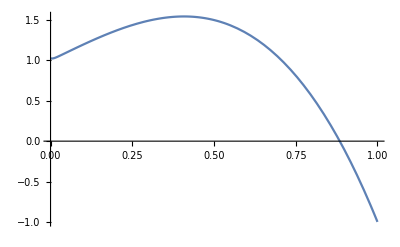

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(zh^4 zh) encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. ComplexInfinity)/(zh^4 zh) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[zh]
Series[z2der/.z[r]->zh-ϵ,{ϵ,0,1}]
Normal[Series[z2der/.z[r]->zh-ϵ,{ϵ,0,-1}]]==α
Solve[%,z'[r]][[1]]
Plot[z2der/.%/.z[r]->zh-ϵ/.{ϵ->10^-6,α->1}/.zh->1,{r,0,1}]
Plot[z2der/.%%/.z[r]->zh-ϵ/.{ϵ->0,α->0}/.zh->1,{r,0,1}]
```

(-2 r z'[r]^2-zh z'[r]^3)/(2 ϵ)+(-8 r-8 zh z'[r]-10 r z'[r]^2-3 zh z'[r]^3)/(4 zh)-(5 (16 r+6 r z'[r]^2+zh z'[r]^3) ϵ)/(8 zh^2)+O[ϵ]^2

(-8 r-8 zh z'[r]-10 r z'[r]^2-3 zh z'[r]^3)/(4 zh)+(-2 r z'[r]^2-zh z'[r]^3)/(2 ϵ)==α

{z'[r]→-(2 r (2 zh+5 ϵ))/(3 zh (2 zh+3 ϵ))+(2^(1/3) (24 zh^2 ϵ (2 zh+3 ϵ)-4 r^2 (2 zh+5 ϵ)^2))/(3 zh (2 zh+3 ϵ) (128 r^3 zh^3+960 r^3 zh^2 ϵ+288 r zh^4 ϵ+432 zh^5 α ϵ+2400 r^3 zh ϵ^2+288 r zh^3 ϵ^2+1296 zh^4 α ϵ^2+2000 r^3 ϵ^3-216 r zh^2 ϵ^3+972 zh^3 α ϵ^3+√((128 r^3 zh^3+960 r^3 zh^2 ϵ+288 r zh^4 ϵ+432 zh^5 α ϵ+2400 r^3 zh ϵ^2+288 r zh^3 ϵ^2+1296 zh^4 α ϵ^2+2000 r^3 ϵ^3-216 r zh^2 ϵ^3+972 zh^3 α ϵ^3)^2+4 (24 zh^2 ϵ (2 zh+3 ϵ)-4 r^2 (2 zh+5 ϵ)^2)^3))^(1/3))-1/(3 2^(1/3) zh (2 zh+3 ϵ))(128 r^3 zh^3+960 r^3 zh^2 ϵ+288 r zh^4 ϵ+432 zh^5 α ϵ+2400 r^3 zh ϵ^2+288 r zh^3 ϵ^2+1296 zh^4 α ϵ^2+2000 r^3 ϵ^3-216 r zh^2 ϵ^3+972 zh^3 α ϵ^3+√((128 r^3 zh^3+960 r^3 zh^2 ϵ+288 r zh^4 ϵ+432 zh^5 α ϵ+2400 r^3 zh ϵ^2+288 r zh^3 ϵ^2+1296 zh^4 α ϵ^2+2000 r^3 ϵ^3-216 r zh^2 ϵ^3+972 zh^3 α ϵ^3)^2+4 (24 zh^2 ϵ (2 zh+3 ϵ)-4 r^2 (2 zh+5 ϵ)^2)^3))^(1/3)}

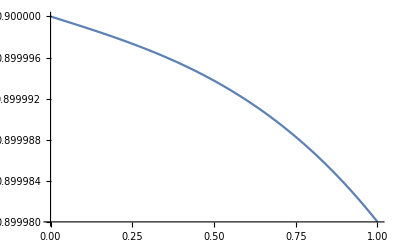

```mathematica
Series[z2der/.z[r]->zh-ϵ,{ϵ,0,1}]
Normal[Series[z2der/.z[r]->zh-ϵ,{ϵ,0,0}]]==α
Solve[%,z'[r]][[1]]
Plot[z2der/.%/.z[r]->zh-ϵ/.{ϵ->10^-6,α->0.9}/.zh->1,{r,0,1}]
```

```mathematica
z2der/.z'[r]->0/.r->0
```

0

```mathematica
Simplify[z'[r]^2 z2dercoffs[[3]]+ z'[r]^3 z2dercoffs[[4]]]
Series[%/.z[r]->zh-ϵ,{ϵ,0,1}]
```

(2 zh^4 z'[r]^2 (2 r+z[r] z'[r]))/(-zh^4 z[r]+z[r]^5)

-(z'[r]^2 (2 r+zh z'[r]))/(2 ϵ)-(z'[r]^2 (10 r+3 zh z'[r]))/(4 zh)-(5 (z'[r]^2 (6 r+zh z'[r])) ϵ)/(8 zh^2)+O[ϵ]^2

```mathematica
Simplify[z'[r]^2 z2dercoffs[[3]]+ z'[r]^3 z2dercoffs[[4]]/.z'[r]->Sqrt[1-z[r]^4/zh^4]]
Limit[%,z[r]->zh]
```

-(4 r)/z[r]-2 √(1-z[r]^4/zh^4)

-(4 r)/zh

```mathematica
Simplify[z'[r]^2 z2dercoffs[[3]]+ z'[r]^3 z2dercoffs[[4]]]
Solve[zh^4(2 r + z[r]z'[r])==α Denominator[%],z'[r]](*include zh^4 to match dimensions - z' is dimensionless*)
%%/.%[[1]]
Limit[%,z[r]->zh]
```

(2 zh^4 z'[r]^2 (2 r+z[r] z'[r]))/(-zh^4 z[r]+z[r]^5)

{{z'[r]→(-2 r zh^4-zh^4 α z[r]+α z[r]^5)/(zh^4 z[r])}}

(2 (-2 r zh^4-zh^4 α z[r]+α z[r]^5)^2 (2 r+(-2 r zh^4-zh^4 α z[r]+α z[r]^5)/zh^4))/(zh^4 z[r]^2 (-zh^4 z[r]+z[r]^5))

(8 r^2 α)/zh^2

This is the unique non-vanishing solution, up to dimensionless rescaling, only possibilities seems to be some function of l/zh since we don’t have any other dimensionless scales

so we have for the value at the horizon

```mathematica
-(2 r)/z[r]-α (1-z[r]^4/zh^4)
z'[zh]==Limit[%,z[r]->zh]
```

-(2 r)/z[r]-α (1-z[r]^4/zh^4)

z'[zh]==-(2 r)/zh

```mathematica
z2der
```

-(2 (-3 r z[r]^4+r z[r]^8-z[r]^5 z'[r]+2 r (1+z'[r]^2)+z[r] z'[r] (1+z'[r]^2)))/(z[r] (1-z[r]^4))

we are fixing r here (and expanding abotu the value r=0 where the second derivative vanishes) and looking for the value of z where the sedond derivative changes sign (z=1 is at the horizon)

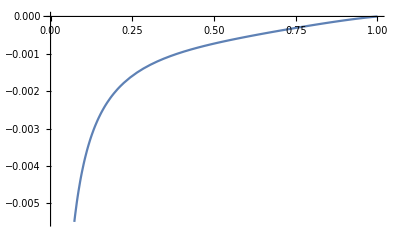

```mathematica
Plot[z2der f[z[r]]/.z[r]->z/.z'[r]->0/.r->10^-4,{z,0,1}]
```

It' s monotonic, so there are no points where it changes sign and hence the solution will always fall towards the horizon if we shoot from r=0 unless we do something like add in a potential

#### numerical solutions

NDSolve::ndsz: At r == 2.48398, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

2.48398

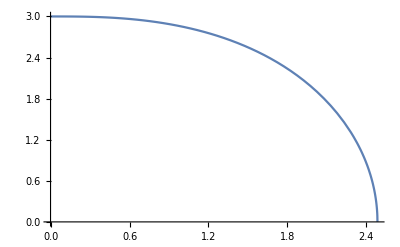

InterpolatingFunction::dmval: Input value {3.51237} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.51287} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.27159} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
zstaticsol=z/.NDSolve[{z''[r]==z2der/.zh->11,z[0]==3,z'[0]==0},z,{r,0,10}][[1]]
rmax=(zstaticsol@Domain)[[1,2]]
Plot[(zstaticsol)[r],{r,0,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-0.29]]
```

check to make sure that we haven’t made any coordinate mistakes, this looks right if horizon is at z=0, but we have the horizon set to z=11 here so it looks like the bubble is away from the horizon. 

It could be interesting if that’s true, then maybe we can literally have bubbles boiling off the horizon. but I have likely done something weird here. 

Also if these solutions exist then they probably  exist in the other direction too.

InterpolatingFunction[…]

2.49

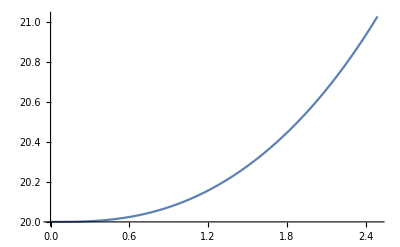

InterpolatingFunction::dmval: Input value {3.52089} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.52139} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.27952} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
zstaticsol=z/.NDSolve[{z''[r]==z2der/.zh->11,z[0]==20,z'[0]==0},z,{r,0,2.49}][[1]]
rmax=(zstaticsol@Domain)[[1,2]]
Plot[(zstaticsol)[r],{r,0,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-0.29]]
```

**** FORGOT A FACTOR OF r!!!!!!!!!!!!!!!!!!!

NDSolve::ndsz: At r == 8.8994, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

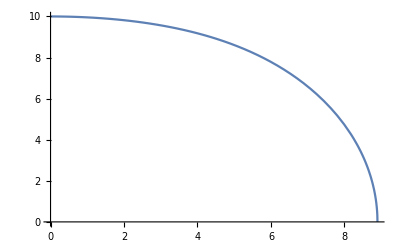

InterpolatingFunction::dmval: Input value {12.5839} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.5857} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {11.7212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
stiffcutoff = 10^-6;
zstaticsol=z/.NDSolve[{r z''[r]==z2der/.zh->11,z[stiffcutoff]==10,z'[stiffcutoff]==0},z,{r,stiffcutoff,10}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{0,11}]
```

This does seem very weird, this solution seems to correspond to some weird silo solution with the top near the horizon and the shaft extending to z of -∞

 I wonder if adding in a potential changes things
 
 also could be that by taking z’=0 away from r=0 is forcing it up, give z’ a small positive value see if that changes direction

NDSolve::ndsz: At r == 8.89941, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

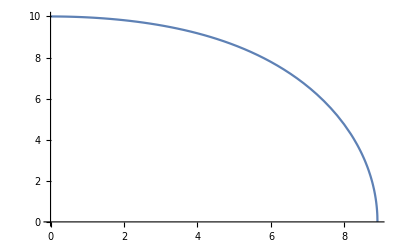

InterpolatingFunction::dmval: Input value {12.5839} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.5857} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {11.7212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
stiffcutoff = 10^-5;
zstaticsol=z/.NDSolve[{r z''[r]==z2der/.zh->11,z[stiffcutoff]==10,z'[stiffcutoff]==10},z,{r,stiffcutoff,10}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2]]
```

just moving on because I found another hair free cutoff

NDSolve::ndsz: At r == 9.39366, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

9.39366

0.00001

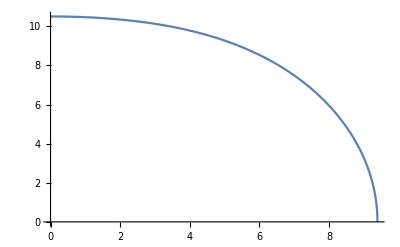

InterpolatingFunction::dmval: Input value {13.2827} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {13.2846} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.3722} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
stiffcutoff = 10^-5;
zstaticsol=z/.NDSolve[{r z''[r]==z2der/.zh->11,z[stiffcutoff]==10.5,z'[stiffcutoff]==10000},z,{r,stiffcutoff,10}][[1]]
rmax=(zstaticsol@Domain)[[1,2]]
rmin = (zstaticsol@Domain)[[1,1]]
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2]]
```

WTF, it seems incredibly insensitive to the initial value of the first derivative, so long as it’s abs is less than 1/stiffcutoff

I think this is just because of the tiny cutoff, if you look below, increasing the cutoff to a macroscopic finite value makes it again sensitive to the derivative

NDSolve::ndsz: At r == 846.819, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

846.819

0.00001

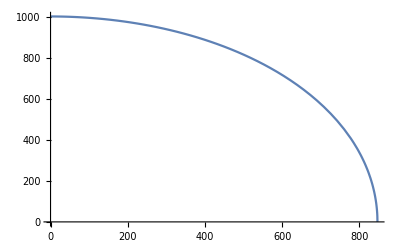

InterpolatingFunction::dmval: Input value {1197.41} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1197.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1115.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
stiffcutoff = 10^-5;
zstaticsol=z/.NDSolve[{r z''[r]==z2der/.zh->11000,z[stiffcutoff]==1000.5,z'[stiffcutoff]==10},z,{r,stiffcutoff,1000}][[1]]
rmax=(zstaticsol@Domain)[[1,2]]
rmin = (zstaticsol@Domain)[[1,1]]
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2]]
```

NDSolve::ndsz: At r == 16.0193, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

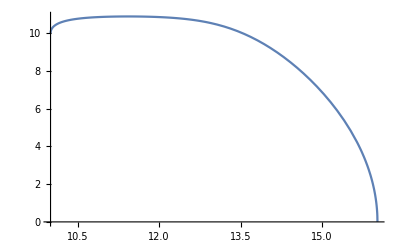

InterpolatingFunction::dmval: Input value {22.6515} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {22.6548} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {21.0987} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
stiffcutoff = 10;
zstaticsol=z/.NDSolve[{r z''[r]==z2der/.zh->11,z[stiffcutoff]==10,z'[stiffcutoff]==30000},z,{r,stiffcutoff,100}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2]]
```

this seems promising, it looks like it it is beginning to approach the horizon. This gives some confidence that such solutions on the horizon exist

to patch it together we would need a solution that starts near the horizon and approaches this solution

```mathematica
Clear[z]
r0 = 50;
zstaticsol=z/.NDSolve[{(r0-r) z''[r0-r]==z2der/.zh->11,z[r0]==10,z'[r0]==10},z,{r,0,r0}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2]]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::idelay: Initial history needs to be specified for all variables for delay-differential equations.

ReplaceAll::reps: {(50-r) z''[50-r]==-(2 (-43923 r z[r]^4+r z[r]^8-14641 («1»)^5 z'[r]+428717762 r (1+((«1»)^(«1»)[«1»])^2)+214358881 z[r] z'[r] (1+((«1»)^(«1»)[«1»])^2)))/(14641 z[r] (14641-z[«1»]^4)),z[50]==10,z'[50]==10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

z/.{(50-r) z''[50-r]==-((2 (-43923 r z[r]^4+r z[r]^8-14641 z[r]^5 z'[r]+428717762 r (1+z'[r]^2)+214358881 z[r] z'[r] (1+z'[r]^2)))/(14641 z[r] (14641-z[r]^4))),z[50]==10,z'[50]==10}

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{(50-r) z''[50+Times[«2»]]==-(2 (-43923 r Power[«2»]+r Power[«2»]-«1»+428717762 r Plus[«2»]+214358881 z[«1»] («1»)^(«1»)[«1»] Plus[«2»]))/(14641 z[r] (14641+Times[«2»])),z[50]==10,z'[50]==10})[Domain]⟦1,2⟧ is longer than depth of object.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{(50-r) z''[50+Times[«2»]]==-(2 (-43923 r Power[«2»]+r Power[«2»]-«1»+428717762 r Plus[«2»]+214358881 z[«1»] («1»)^(«1»)[«1»] Plus[«2»]))/(14641 z[r] (14641+Times[«2»])),z[50]==10,z'[50]==10})[Domain]⟦1,1⟧ is longer than depth of object.

ReplaceAll::reps: {(50.-1. r) z''[50.-1. r]==-(0.000136603 (-43923. r z[r]^4+r z[r]^8-«1»+«14» r («1»)+2.14359×10^8 z[r] z'[r] (1.+((«1»)^(«1»)[«1»])^2)))/(z[r] (14641.-1. z[«1»]^4)),z[50.]==10.,z'[50.]==10.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{(50.-1. r) z''[50.+Times[«2»]]==-(0.000136603 («1»))/(z[r] (14641.+Times[«2»])),z[50.]==10.,z'[50.]==10.})[Domain]⟦1,1⟧ is longer than depth of object.

Plot::plln: Limiting value (z/.{(50-r) z''[50+Times[«2»]]==-(2 (-43923 r Power[«2»]+r Power[«2»]-«1»+428717762 r Plus[«2»]+214358881 z[«1»] («1»)^(«1»)[«1»] Plus[«2»]))/(14641 z[r] (14641+Times[«2»])),z[50]==10,z'[50]==10})[Domain]⟦1,1⟧ in {r,(z/.{(50+Times[«2»]) z''[Plus[«2»]]==-(2 (Times[«3»]+«4»))/(14641 z[«1»] Plus[«2»]),z[50]==10,z'[50]==10})[Domain]⟦1,1⟧,(z/.{(50+Times[«2»]) z''[Plus[«2»]]==-(2 (Times[«3»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«4»]))/(14641 z[«1»] Plus[«2»]),z[50]==10,z'[50]==10})[Domain]⟦1,2⟧} is not a machine-sized real number.

Plot[zstaticsol[r],{r,rmin,rmax}]

ReplaceAll::reps: {(50.-1. r) z''[50.-1. r]==-(0.000136603 (-43923. r z[r]^4+r z[r]^8-«1»+«14» r («1»)+2.14359×10^8 z[r] z'[r] (1.+((«1»)^(«1»)[«1»])^2)))/(z[r] (14641.-1. z[«1»]^4)),z[50.]==10.,z'[50.]==10.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{(50.-1. r) z''[50.+Times[«2»]]==-(0.000136603 («1»))/(z[r] (14641.+Times[«2»])),z[50.]==10.,z'[50.]==10.})[Domain]⟦1,2⟧ is longer than depth of object.

Plot3D::plln: Limiting value -(z/.{(50+Times[«2»]) z''[Plus[«2»]]==-(2 (Times[«3»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«4»]))/(14641 z[«1»] Plus[«2»]),z[50]==10,z'[50]==10})[Domain]⟦1,2⟧ in {x,-(z/.{Plus[«2»] («1»)^(«1»)[«1»]==-(2 Power[«2»] «1» Plus[«5»])/14641,z[50]==10,z'[50]==10})[Domain]⟦1,2⟧,(z/.{(50+Times[«2»]) z''[Plus[«2»]]==-(2 (Times[«3»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«4»]))/(14641 z[«1»] Plus[«2»]),z[50]==10,z'[50]==10})[Domain]⟦1,2⟧} is not a machine-sized real number.

Plot3D[zstaticsol[√(x^2+y^2)],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction→Function[{x,y,z},rmin^2<x^2+y^2<rmax^2]]

UPSHOTS:

start some and put all this into notes
also consider redoing this analysis with r(z) to see if we can get the solution we are looking for

NDSolve::ndsz: At r == 0.878164, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

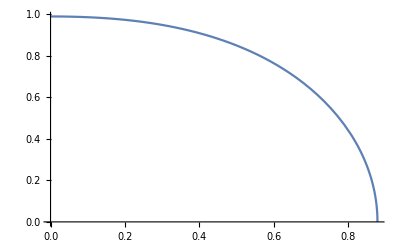

InterpolatingFunction::dmval: Input value {1.24173} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.24191} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.15661} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
stiffcutoff = 10^-6;
zstaticsol=z/.NDSolve[{r z''[r]==z2der/.zh->1,z[stiffcutoff]==0.99,z'[stiffcutoff]==0},z,{r,stiffcutoff,0.9}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax-0.02)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{0,1}]
```

InterpolatingFunction[…][r]

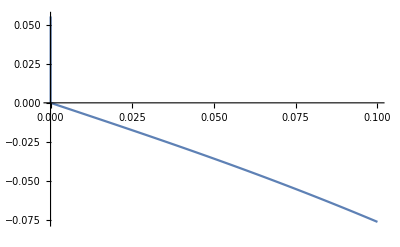

InterpolatingFunction[…][r]

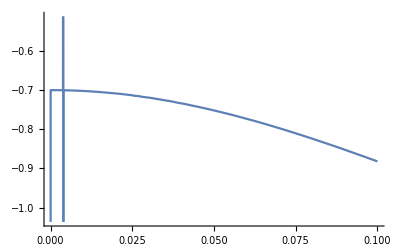

```mathematica
D[zstaticsol[r],r]
Plot[%,{r,0,0.1}]
D[zstaticsol[r],{r,2}]
Plot[%,{r,0,0.1}]
```

```mathematica
Simplify[z2der f[z[r]]]/.z[r]->zh
Solve[%==0,z'[r]]
```

(4 r)/zh+2 z'[r]-(4 r (1+z'[r]^2))/zh-2 (z'[r]+z'[r]^3)

{{z'[r]→0},{z'[r]→0},{z'[r]→-(2 r)/zh}}

```mathematica
zhz2deris0=z'[r]/.PowerExpand[Solve[z2der==0,z'[r]][[1]]/.z[r]->zh]
```

-(2 r)/(3 zh)+(2 (-1)^(1/3) r)/(3 zh)-(2 (-1)^(2/3) r)/(3 zh)

Try again but this time multiply both sides by the blackening factor to remove the singularity

```mathematica
Clear[z]
stiffcutoff = 10^-6;
zstaticsol=z/.NDSolve[{f[z[r]]r z''[r]==z2der f[z[r]]/.zh->11,z[stiffcutoff]==10,z'[stiffcutoff]==0},z,{r,stiffcutoff,10}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{0,11}]
```

NDSolve::ndsz: At r == 8.8994, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

-Graphics-

InterpolatingFunction::dmval: Input value {12.5839} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {12.5857} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {11.7212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

works , now try with BC starting on the horizon

```mathematica
Simplify[z2der f[z[r]]]/.z[r]->zh
Solve[%==0,z'[r]]
```

(4 r)/zh+2 z'[r]-(4 r (1+z'[r]^2))/zh-2 (z'[r]+z'[r]^3)

{{z'[r]→0},{z'[r]→0},{z'[r]→-(2 r)/zh}}

```mathematica
Clear[z]
rh = 0.4;
zh=1;
Simplify[z2der f[z[r]]]
zstaticsol=z/.NDSolve[{f[z[r]]r  z''[r]==%,z[rh]==zh,z'[rh]==-(2rh)/zh},z,{r,rh,0}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{11,13}]
```

6 r z[r]^3-2 r z[r]^7+2 z[r]^4 z'[r]-(4 r (1+z'[r]^2))/z[r]-2 (z'[r]+z'[r]^3)

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 0.4.

ReplaceAll::reps: {r (1-z[r]^4) z''[r]==6 r z[r]^3-2 r z[r]^7+2 z[r]^4 z'[r]-(4 r (1+z'[r]^2))/z[r]-2 (z'[r]+z'[r]^3),z[0.4]==1,z'[0.4]==-0.8} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

z/.{r (1-z[r]^4) z''[r]==6 r z[r]^3-2 r z[r]^7+2 z[r]^4 z'[r]-(4 r (1+z'[r]^2))/z[r]-2 (z'[r]+z'[r]^3),z[0.4]==1,z'[0.4]==-0.8}

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r (1-Power[«2»]) z''[r]==6 r z[«1»]^3-2 r z[«1»]^7+2 z[«1»]^4 z'[r]-(4 r (1+Power[«2»]))/z[«1»]-2 ((«1»)^(«1»)[«1»]+Power[«2»]),z[0.4]==1,z'[0.4]==-0.8})[Domain]⟦1,2⟧ is longer than depth of object.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r (1-Power[«2»]) z''[r]==6 r z[«1»]^3-2 r z[«1»]^7+2 z[«1»]^4 z'[r]-(4 r (1+Power[«2»]))/z[«1»]-2 ((«1»)^(«1»)[«1»]+Power[«2»]),z[0.4]==1,z'[0.4]==-0.8})[Domain]⟦1,1⟧ is longer than depth of object.

ReplaceAll::reps: {r (1.-1. z[r]^4) z''[r]==6. r z[r]^3-2. r z[r]^7+2. z[r]^4 z'[r]-(4. r (1.+z'[r]^2))/z[r]-2. (z'[r]+z'[r]^3),z[0.4]==1.,z'[0.4]==-0.8} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r (1.-1. Power[«2»]) z''[r]==6. r z[«1»]^3-2. r z[«1»]^7+2. z[«1»]^4 z'[r]-(4. r (1.+Power[«2»]))/z[«1»]-2. ((«1»)^(«1»)[«1»]+Power[«2»]),z[0.4]==1.,z'[0.4]==-0.8})[Domain]⟦1,1⟧ is longer than depth of object.

Plot::plln: Limiting value (z/.{r (1-Power[«2»]) z''[r]==6 r z[«1»]^3-2 r z[«1»]^7+2 z[«1»]^4 z'[r]-(4 r (1+Power[«2»]))/z[«1»]-2 ((«1»)^(«1»)[«1»]+Power[«2»]),z[0.4]==1,z'[0.4]==-0.8})[Domain]⟦1,1⟧ in {r,(z/.{r (1+Times[«2»]) z''[r]==6 r Power[«2»]-2 r Power[«2»]+2 Power[«2»] («1»)^(«1»)[«1»]-4 r Power[«2»] Plus[«2»]-2 Plus[«2»],z[0.4]==1,z'[0.4]==-0.8})[Domain]⟦1,1⟧,(z/.{r (1+Times[«2»]) z''[r]==6 r Power[«2»]-2 r Power[«2»]+2 Power[«2»] («1»)^(«1»)[«1»]-4 r Power[«2»] Plus[«2»]-2 Plus[«2»],z[0.4]==1,z'[0.4]==-0.8})[Domain]⟦1,2⟧} is not a machine-sized real number.

Plot[zstaticsol[r],{r,rmin,rmax}]

ReplaceAll::reps: {r (1.-1. z[r]^4) z''[r]==6. r z[r]^3-2. r z[r]^7+2. z[r]^4 z'[r]-(4. r (1.+z'[r]^2))/z[r]-2. (z'[r]+z'[r]^3),z[0.4]==1.,z'[0.4]==-0.8} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r (1.-1. Power[«2»]) z''[r]==6. r z[«1»]^3-2. r z[«1»]^7+2. z[«1»]^4 z'[r]-(4. r (1.+Power[«2»]))/z[«1»]-2. ((«1»)^(«1»)[«1»]+Power[«2»]),z[0.4]==1.,z'[0.4]==-0.8})[Domain]⟦1,2⟧ is longer than depth of object.

Plot3D::plln: Limiting value -(z/.{r (1+Times[«2»]) z''[r]==6 r Power[«2»]-2 r Power[«2»]+2 Power[«2»] («1»)^(«1»)[«1»]-4 r Power[«2»] Plus[«2»]-2 Plus[«2»],z[0.4]==1,z'[0.4]==-0.8})[Domain]⟦1,2⟧ in {x,-(z/.{r Plus[«2»] («1»)^(«1»)[«1»]==Times[«3»]+Times[«3»]+Times[«3»]+Times[«4»]+Times[«2»],z[0.4]==1,z'[0.4]==-0.8})[Domain]⟦1,2⟧,(z/.{r (1+Times[«2»]) z''[r]==6 r Power[«2»]-2 r Power[«2»]+2 Power[«2»] («1»)^(«1»)[«1»]-4 r Power[«2»] Plus[«2»]-2 Plus[«2»],z[0.4]==1,z'[0.4]==-0.8})[Domain]⟦1,2⟧} is not a machine-sized real number.

Plot3D[zstaticsol[√(x^2+y^2)],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction→Function[{x,y,z},rmin^2<x^2+y^2<rmax^2],AxesLabel→{,,z},PlotLabel→AdS Boundary at z=0 - BBH at z_h=11,PlotRange→{11,13}]

#### numerical solution - with regularity condition

```mathematica
Limit[z2der/.z'[r]->-2 r/zh,z[r]->zh]
```

-(16 r^3 zh^5-8 r zh^7)/(4 zh^8)

```mathematica
z[rh]==zh/.zh->11
z'[rh]==-(2r)/zh/.zh->11
```

```mathematica
r  z''[r]==Simplify[z2der/.z[r]->zh]
```

Power::infy: Infinite expression 1/0 encountered.

r z''[r]==ComplexInfinity

```mathematica
r  z''[r]==Simplify[z2der/.{z'[r]->(-2 rh)/zh}]/.z[r]->zh
```

Power::infy: Infinite expression 1/0 encountered.

r z''[r]==ComplexInfinity

```mathematica
Clear[z]
rh = 3;
zh=11;
zstaticsol=z/.NDSolve[{r  z''[r]==z2der,z[rh]==zh,z'[rh]==-(2rh)/zh},z,{r,rh,0}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{0,11}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 3..

ReplaceAll::reps: {r z''[r]==-(2 (-43923 r z[r]^4+r z[r]^8-14641 z[r]^5 z'[r]+428717762 r (1+((«1»)^(«1»)[«1»])^2)+214358881 z[r] z'[r] (1+((«1»)^(«1»)[«1»])^2)))/(14641 z[r] (14641-z[«1»]^4)),z[3]==11,z'[3]==-6/11} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

z/.{r z''[r]==-(2 (-43923 r z[r]^4+r z[r]^8-14641 z[r]^5 z'[r]+428717762 r (1+z'[r]^2)+214358881 z[r] z'[r] (1+z'[r]^2)))/(14641 z[r] (14641-z[r]^4)),z[3]==11,z'[3]==-6/11}

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r z''[r]==-(2 (-43923 r Power[«2»]+r Power[«2»]-14641 Power[«2»] («1»)^(«1»)[«1»]+428717762 r Plus[«2»]+214358881 z[«1»] («1»)^(«1»)[«1»] Plus[«2»]))/(14641 z[r] (14641+Times[«2»])),z[3]==11,z'[3]==-6/11})[Domain]⟦1,2⟧ is longer than depth of object.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r z''[r]==-(2 (-43923 r Power[«2»]+r Power[«2»]-14641 Power[«2»] («1»)^(«1»)[«1»]+428717762 r Plus[«2»]+214358881 z[«1»] («1»)^(«1»)[«1»] Plus[«2»]))/(14641 z[r] (14641+Times[«2»])),z[3]==11,z'[3]==-6/11})[Domain]⟦1,1⟧ is longer than depth of object.

ReplaceAll::reps: {r z''[r]==-(0.000136603 (-43923. r z[r]^4+r z[r]^8-14641. z[r]^5 z'[r]+4.28718×10^8 r (1.+((«1»)^(«1»)[«1»])^2)+2.14359×10^8 z[r] z'[r] (1.+((«1»)^(«1»)[«1»])^2)))/(z[r] (14641.-1. z[«1»]^4)),z[3.]==11.,z'[3.]==-0.545455} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r z''[r]==-(0.000136603 (-43923. r Power[«2»]+r Power[«2»]-14641. Power[«2»] («1»)^(«1»)[«1»]+4.28718×10^8 r Plus[«2»]+2.14359×10^8 z[«1»] («1»)^(«1»)[«1»] Plus[«2»]))/(z[r] (14641.+Times[«2»])),z[3.]==11.,z'[3.]==-0.545455})[Domain]⟦1,1⟧ is longer than depth of object.

Plot::plln: Limiting value (z/.{r z''[r]==-(2 (-43923 r Power[«2»]+r Power[«2»]-14641 Power[«2»] («1»)^(«1»)[«1»]+428717762 r Plus[«2»]+214358881 z[«1»] («1»)^(«1»)[«1»] Plus[«2»]))/(14641 z[r] (14641+Times[«2»])),z[3]==11,z'[3]==-6/11})[Domain]⟦1,1⟧ in {r,(z/.{r z''[r]==-(2 (Times[«3»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«4»]))/(14641 z[«1»] Plus[«2»]),z[3]==11,z'[3]==-6/11})[Domain]⟦1,1⟧,(z/.{r z''[r]==-(2 (Times[«3»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«4»]))/(14641 z[«1»] Plus[«2»]),z[3]==11,z'[3]==-6/11})[Domain]⟦1,2⟧} is not a machine-sized real number.

Plot[zstaticsol[r],{r,rmin,rmax}]

ReplaceAll::reps: {r z''[r]==-(0.000136603 (-43923. r z[r]^4+r z[r]^8-14641. z[r]^5 z'[r]+4.28718×10^8 r (1.+((«1»)^(«1»)[«1»])^2)+2.14359×10^8 z[r] z'[r] (1.+((«1»)^(«1»)[«1»])^2)))/(z[r] (14641.-1. z[«1»]^4)),z[3.]==11.,z'[3.]==-0.545455} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r z''[r]==-(0.000136603 (-43923. r Power[«2»]+r Power[«2»]-14641. Power[«2»] («1»)^(«1»)[«1»]+4.28718×10^8 r Plus[«2»]+2.14359×10^8 z[«1»] («1»)^(«1»)[«1»] Plus[«2»]))/(z[r] (14641.+Times[«2»])),z[3.]==11.,z'[3.]==-0.545455})[Domain]⟦1,2⟧ is longer than depth of object.

Plot3D::plln: Limiting value -(z/.{r z''[r]==-(2 (Times[«3»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«4»]))/(14641 z[«1»] Plus[«2»]),z[3]==11,z'[3]==-6/11})[Domain]⟦1,2⟧ in {x,-(z/.{r («1»)^(«1»)[«1»]==-(2 Power[«2»] Power[«2»] Plus[«5»])/14641,z[3]==11,z'[3]==-6/11})[Domain]⟦1,2⟧,(z/.{r z''[r]==-(2 (Times[«3»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«4»]))/(14641 z[«1»] Plus[«2»]),z[3]==11,z'[3]==-6/11})[Domain]⟦1,2⟧} is not a machine-sized real number.

Plot3D[zstaticsol[√(x^2+y^2)],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction→Function[{x,y,z},rmin^2<x^2+y^2<rmax^2],AxesLabel→{,,z},PlotLabel→AdS Boundary at z=0 - BBH at z_h=11,PlotRange→{0,11}]

the above isn’t working because of the removable singularity at zh=z, try using a piecewise function instead

```mathematica
Piecewise[{{z2dert,rt!=rh&&z[rt]!=zh}},-(16 rh^3 zh^5-8 rh zh^7)/(4 zh^8)]/.rt->rh-0.1
```

Piecewise[{{-(2 (-127377. z[2.9]^4+2.9 z[2.9]^8-14641 z[2.9]^5 z'[2.9]+1.24328×10^9 (1+z'[2.9]^2)+214358881 z[2.9] z'[2.9] (1+z'[2.9]^2)))/(14641 z[2.9] (14641-z[2.9]^4)), z[2.9]≠11}, {618/1331, True}}]

-(2 (-43923 rt z[rt]^4+rt z[rt]^8-14641 z[rt]^5 z'[rt]+428717762 rt (1+z'[rt]^2)+214358881 z[rt] z'[rt] (1+z'[rt]^2)))/(14641 z[rt] (14641-z[rt]^4))

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {-0.988949,ComplexInfinity} is not a list of numbers with dimensions {2} at {r,z[r],z'[r]} = {0.,13.0452,-0.988949}.

InterpolatingFunction[…]

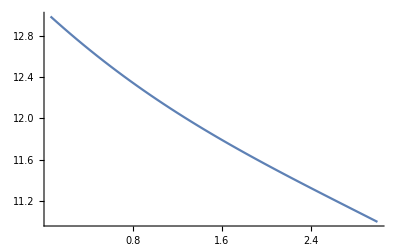

InterpolatingFunction::dmval: Input value {4.24203} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.24264} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.95123} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
rh = 3;
zh=11;
z2dert = z2der/.r->rt
zstaticsol=z/.NDSolve[{r  z''[r]==Piecewise[{{z2dert,rt!=rh&&z[rt]!=zh}},-(16 rh^3 zh^5-8 rh zh^7)/(4 zh^8)]/.rt->r,z[rh]==zh,z'[rh]==-(2rh)/zh},z,{r,rh,0}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{11,13}]
```

Getting there, but it is still evolving the wrong way

```mathematica
Limit[z2der/.z'[r]->-6 r/zh,z[r]->zh]
Plot[%,{r,0,1}]
```

Indeterminate

-Graphics-

{z'[r]→-(2 r)/(3 zh)+(2 (-1)^(1/3) r)/(3 zh)-(2 (-1)^(2/3) r)/(3 zh)}

1/100000

0.39999

1/1000000

999999/1000000

NDSolve::ndsz: At r == 0.39999, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

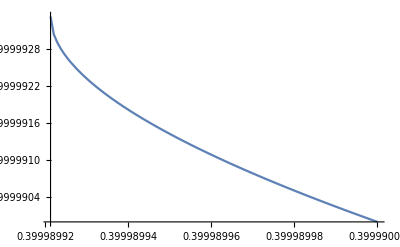

InterpolatingFunction::dmval: Input value {0.56559} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.565671} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.526818} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
rh = 0.4;
zh=1;
z2dert = z2der/.r->rt;
rcutoff=10^-5
r0=rh-rcutoff
zcutoff = 10^-6
z0 = zh-zcutoff
zstaticsol=z/.NDSolve[{r  z''[r]==Piecewise[{{z2dert,rt!=rh&&z[rt]!=zh}},0]/.rt->r,z[r0]==z0,z'[r0]==-(6rh)/zh},z,{r,r0,0}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{11,13}]
```

1/100000

0.39999

1/1000000

999999/1000000

NDSolve::ndsz: At r == 0.000243151, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

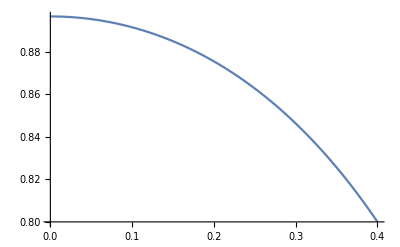

InterpolatingFunction::dmval: Input value {0.56559} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.565671} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.526818} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
rh = 0.4;
zh=1;
z2dert = z2der/.r->rt;
rcutoff=10^-5
r0=rh-rcutoff
zcutoff = 10^-6
z0 = zh-zcutoff
zstaticsol=z/.NDSolve[{r  z''[r]==Piecewise[{{z2dert,rt!=rh&&z[rt]!=zh}},0]/.rt->r,z[r0]==z0-0.2,z'[r0]==-(1.416585 rh)/zh},z,{r,r0,0}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{0,1}]
```

1/100000

0.39999

1/1000000

999999/1000000

NDSolve::ndsz: At r == 0.353846, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

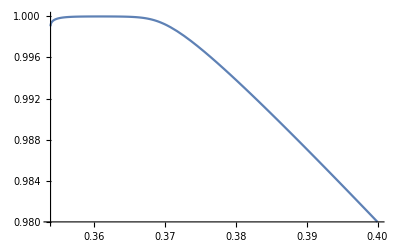

InterpolatingFunction::dmval: Input value {0.56559} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.565671} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.526818} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
rh = 0.4;
zh=1;
z2dert = z2der/.r->rt;
rcutoff=10^-5
r0=rh-rcutoff
zcutoff = 10^-6
z0 = zh-zcutoff
zstaticsol=z/.NDSolve[{r  z''[r]==Piecewise[{{z2dert,rt!=rh&&z[rt]!=zh}},0]/.rt->r,z[r0]==z0-0.02,z'[r0]==(-1.8rh)/zh},z,{r,r0,0}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{0,1}]
```

1/100000

0.39999

1/1000000

999999/1000000

NDSolve::ndsz: At r == 0.39999, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

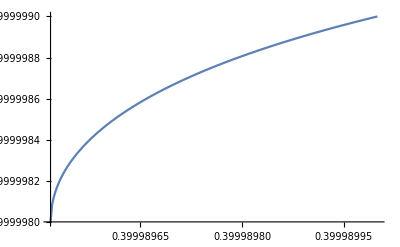

InterpolatingFunction::dmval: Input value {0.56559} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.565671} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.526818} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
rh = 0.4;
zh=1;
z2dert = z2der/.r->rt;
rcutoff=10^-5
r0=rh-rcutoff
zcutoff = 10^-6
z0 = zh-zcutoff
zstaticsol=z/.NDSolve[{r  z''[r]==Piecewise[{{z2dert,rt!=rh&&z[rt]!=zh}},0]/.rt->r,z[r0]==z0,z'[r0]==2 rh/zh},z,{r,r0,0}][[1]]
rmax=(zstaticsol@Domain)[[1,2]];
rmin = (zstaticsol@Domain)[[1,1]];
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2],AxesLabel->{"","","z"},PlotLabel->"AdS Boundary at z=0 - BBH at z_h=11",PlotRange->{0,1}]
```

### Add in potential

#### static z(r) (potential from pujolas notes)

```mathematica
sqrtmg = Sqrt[(1-z^4/zh^4)+drz^2]
potrepl={β->0.3,δ->0.1076}
L = -4 π r^2 σ l^4/z^4 sqrtmg+(l^4 σ)/z^4(-1 +δ - β z)/.potrepl
```

√(1+drz^2-z^4/zh^4)

{β→0.3,δ→0.1076}

(l^4 (-0.8924-0.3 z) σ)/z^4-(4 l^4 π r^2 √(1+drz^2-z^4/zh^4) σ)/z^4

```mathematica
zrepl={z->z[r],drz->D[z[r],r]}
```

{z→z[r],drz→z'[r]}

```mathematica
Clear[dLdz,pr,pt]
dLdz=D[L,z]/.zrepl
pr = D[L,drz]/.zrepl
pt = D[L,dtz]/.zrepl
```

-(4 l^4 σ (-0.8924-0.3 z[r]))/z[r]^5-(0.3 l^4 σ)/z[r]^4+(8 l^4 π r^2 σ)/(zh^4 z[r] √(1-z[r]^4/zh^4+z'[r]^2))+(16 l^4 π r^2 σ √(1-z[r]^4/zh^4+z'[r]^2))/z[r]^5

-(4 l^4 π r^2 σ z'[r])/(z[r]^4 √(1-z[r]^4/zh^4+z'[r]^2))

0

```mathematica
zsolpot=Solve[D[pr,r]+D[pt,t]==dLdz,z''[r]]
z2derpot=Simplify[(z''[r]/.zsolpot[[1]])]r(*multiply by r so non-singular at r=0 *)
Simplify[CoefficientList[z2derpot,z'[r]]]
```

{{z''[r]→(-(4. l^4 σ (-0.8924-0.3 z[r]))/z[r]^5-(0.3 l^4 σ)/z[r]^4+(25.1327 l^4 r^2 σ z'[r]^2)/(zh^4 z[r] (1.-(1. z[r]^4)/zh^4+z'[r]^2)^(3/2))+(25.1327 l^4 r^2 σ)/(zh^4 z[r] √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+(25.1327 l^4 r σ z'[r])/(z[r]^4 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))-(50.2655 l^4 r^2 σ z'[r]^2)/(z[r]^5 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+(50.2655 l^4 r^2 σ √(1.-(1. z[r]^4)/zh^4+z'[r]^2))/z[r]^5)/((12.5664 l^4 r^2 σ z'[r]^2)/(z[r]^4 (1.-(1. z[r]^4)/zh^4+z'[r]^2)^(3/2))-(12.5664 l^4 r^2 σ)/(z[r]^4 √(1.-(1. z[r]^4)/zh^4+z'[r]^2)))}}

1/(r zh^4 (1. zh^4 z[r]-1. z[r]^5))(-2. r^2 z[r]^8+zh^4 z[r]^5 (2. r z'[r]+0.0716197 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+zh^4 z[r]^4 (6. r^2+0.28406 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+zh^8 z[r] (-2. r z'[r]-2. r z'[r]^3-0.0716197 √(1.-(1. z[r]^4)/zh^4+z'[r]^2)-0.0716197 z'[r]^2 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+zh^8 (-4. r^2-0.28406 √(1.-(1. z[r]^4)/zh^4+z'[r]^2)+z'[r]^2 (-4. r^2-0.28406 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))))

{(2. r^2 z[r]^12-0.0716197 zh^12 z[r] √(1.-(1. z[r]^4)/zh^4+z'[r]^2)+0.143239 zh^8 z[r]^5 √(1.-(1. z[r]^4)/zh^4+z'[r]^2)-0.0716197 zh^4 z[r]^9 √(1.-(1. z[r]^4)/zh^4+z'[r]^2)+zh^4 z[r]^8 (-8. r^2-0.28406 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+zh^12 (-4. r^2-0.28406 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+zh^8 z[r]^4 (10. r^2+0.568119 √(1.-(1. z[r]^4)/zh^4+z'[r]^2)))/(r zh^4 z[r] (1. zh^8-2. zh^4 z[r]^4+1. z[r]^8)),-2.,(zh^4 (-4. r^2-0.28406 √(1.-(1. z[r]^4)/zh^4+z'[r]^2)-0.0716197 z[r] √(1.-(1. z[r]^4)/zh^4+z'[r]^2)))/(r (1. zh^4 z[r]-1. z[r]^5)),-(2. zh^4)/(1. zh^4-1. z[r]^4)}

```mathematica
Clear[zh]
FullSimplify[z2derpot ]
```

1/(r^2 zh^4 (1. zh^4 z[r]-1. z[r]^5))(-2. r^2 z[r]^8+zh^4 z[r]^5 (2. r z'[r]+0.0716197 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+zh^4 z[r]^4 (6. r^2+0.28406 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+zh^8 z[r] (-2. r z'[r]-2. r z'[r]^3-0.0716197 √(1.-(1. z[r]^4)/zh^4+z'[r]^2)-0.0716197 z'[r]^2 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))+zh^8 (-4. r^2-0.28406 √(1.-(1. z[r]^4)/zh^4+z'[r]^2)+z'[r]^2 (-4. r^2-0.28406 √(1.-(1. z[r]^4)/zh^4+z'[r]^2))))

NDSolve::ndsz: At r == 0.119034, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

0.119034

0.1

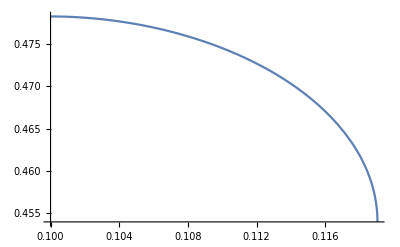

InterpolatingFunction::dmval: Input value {0.168316} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.16834} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.156778} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
stiffcutoff = 10^-1;
zstaticsol=z/.NDSolve[{r z''[r]==z2derpot/.zh->11,z[stiffcutoff]==4/3 δ/β/.potrepl,z'[stiffcutoff]==0},z,{r,stiffcutoff,10}][[1]]
rmax=(zstaticsol@Domain)[[1,2]]
rmin = (zstaticsol@Domain)[[1,1]]
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2]]
```

NDSolve::ndsz: At r == 24.4118, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

24.4118

20.

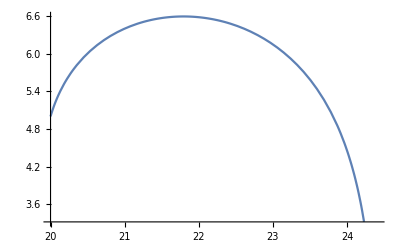

InterpolatingFunction::dmval: Input value {34.5186} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {34.5235} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {32.1523} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Clear[z]
stiffcutoff = 20;
zstaticsol=z/.NDSolve[{r z''[r]==z2derpot/.zh->11,z[stiffcutoff]==5,z'[stiffcutoff]==4},z,{r,stiffcutoff,100}][[1]]
rmax=(zstaticsol@Domain)[[1,2]]
rmin = (zstaticsol@Domain)[[1,1]]
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2]]
```

multiply by f[z]

```mathematica
zsolpot=Solve[D[pr,r]+D[pt,t]==dLdz,z''[r]];
z2derpot=Simplify[(z''[r]/.zsolpot[[1]])r^2 f[z[r]]](*multiply by r so non-singular at r=0 *)
Simplify[CoefficientList[z2derpot,z'[r]]] ;
```

1/z[r](-4. r^2-2. r^2 z[r]^8-0.28406 √(1.-1. z[r]^4+z'[r]^2)+z'[r]^2 (-4. r^2-0.28406 √(1.-1. z[r]^4+z'[r]^2))+z[r]^5 (2. r z'[r]+0.0716197 √(1.-1. z[r]^4+z'[r]^2))+z[r]^4 (6. r^2+0.28406 √(1.-1. z[r]^4+z'[r]^2))+z[r] (-2. r z'[r]-2. r z'[r]^3-0.0716197 √(1.-1. z[r]^4+z'[r]^2)-0.0716197 z'[r]^2 √(1.-1. z[r]^4+z'[r]^2)))

```mathematica
Clear[zh]
z2der0withpot=z'[r]/.Solve[(z2derpot/.z[r]->zh)==0,z'[r]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(0.5 (-2.38879×10^35 r^3 zh-1. r^2 √(1.15111×10^69+5.80457×10^68 zh+7.3175×10^67 zh^2)))/(-1.2047×10^33-6.07479×10^32 zh-7.65815×10^31 zh^2+5.97199×10^34 r^2 zh^2)

```mathematica
rh=0.4;
zh=1;
zstaticsol=z/.NDSolve[{f[z[r]] r^2 z''[r]==z2derpot,z[rh]==zh,z'[rh]==z2der0withpot/.r->rh},z,{r,rh,0}][[1]]
rmax=(zstaticsol@Domain)[[1,2]]
rmin = (zstaticsol@Domain)[[1,1]]
Plot[(zstaticsol)[r],{r,rmin,rmax}]
(*Plot3D[Sqrt[x^2+y^2],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},x^2+y^2<rmax^2-10^-2]]*)
Plot3D[(zstaticsol)[Sqrt[x^2+y^2]],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction->Function[{x,y,z},rmin^2< x^2+y^2<(rmax)^2]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at r == 0.4.

ReplaceAll::reps: {r^2 (1-z[r]^4) z''[r]==(-4. r^2-2. r^2 z[r]^8-0.28406 √(1.+Times[«2»]+Power[«2»])+(«1»)^2 «1»+z[r]^5 (2. r («1»)^(«1»)[«1»]+«20» Power[«1»])+z[r]^4 (6. Power[«2»]+0.28406 Power[«2»])+z[r] (-2. r («1»)^(«1»)[«1»]-2. r Power[«2»]-0.0716197 Power[«2»]-0.0716197 Power[«2»] Power[«2»]))/z[r],z[0.4]==1,z'[0.4]==-1.4404} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

z/.{r^2 (1-z[r]^4) z''[r]==1/z[r](-4. r^2-2. r^2 z[r]^8-0.28406 √(1.-1. z[r]^4+z'[r]^2)+z'[r]^2 (-4. r^2-0.28406 √(1.-1. z[r]^4+z'[r]^2))+z[r]^5 (2. r z'[r]+0.0716197 √(1.-1. z[r]^4+z'[r]^2))+z[r]^4 (6. r^2+0.28406 √(1.-1. z[r]^4+z'[r]^2))+z[r] (-2. r z'[r]-2. r z'[r]^3-0.0716197 √(1.-1. z[r]^4+z'[r]^2)-0.0716197 z'[r]^2 √(1.-1. z[r]^4+z'[r]^2))),z[0.4]==1,z'[0.4]==-1.4404}

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r^2 (1-Power[«2»]) z''[r]==(-4. Power[«2»]-2. Power[«2»] Power[«2»]-0.28406 Power[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+z[«1»] Plus[«4»])/z[r],z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,2⟧ is longer than depth of object.

(z/.{r^2 (1-z[r]^4) z''[r]==1/z[r](-4. r^2-2. r^2 z[r]^8-0.28406 √(1.-1. z[r]^4+z'[r]^2)+z'[r]^2 (-4. r^2-0.28406 √(1.-1. z[r]^4+z'[r]^2))+z[r]^5 (2. r z'[r]+0.0716197 √(1.-1. z[r]^4+z'[r]^2))+z[r]^4 (6. r^2+0.28406 √(1.-1. z[r]^4+z'[r]^2))+z[r] (-2. r z'[r]-2. r z'[r]^3-0.0716197 √(1.-1. z[r]^4+z'[r]^2)-0.0716197 z'[r]^2 √(1.-1. z[r]^4+z'[r]^2))),z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,2⟧

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r^2 (1-Power[«2»]) z''[r]==(-4. Power[«2»]-2. Power[«2»] Power[«2»]-0.28406 Power[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+z[«1»] Plus[«4»])/z[r],z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,1⟧ is longer than depth of object.

(z/.{r^2 (1-z[r]^4) z''[r]==1/z[r](-4. r^2-2. r^2 z[r]^8-0.28406 √(1.-1. z[r]^4+z'[r]^2)+z'[r]^2 (-4. r^2-0.28406 √(1.-1. z[r]^4+z'[r]^2))+z[r]^5 (2. r z'[r]+0.0716197 √(1.-1. z[r]^4+z'[r]^2))+z[r]^4 (6. r^2+0.28406 √(1.-1. z[r]^4+z'[r]^2))+z[r] (-2. r z'[r]-2. r z'[r]^3-0.0716197 √(1.-1. z[r]^4+z'[r]^2)-0.0716197 z'[r]^2 √(1.-1. z[r]^4+z'[r]^2))),z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,1⟧

ReplaceAll::reps: {r^2 (1.-1. z[r]^4) z''[r]==(-4. r^2-2. r^2 z[r]^8-0.28406 √(1.+Times[«2»]+Power[«2»])+(«1»)^2 («1»)+z[r]^5 (2. r («1»)^(«1»)[«1»]+«20» «1»)+z[r]^4 (6. Power[«2»]+0.28406 Power[«2»])+z[r] (-2. r («1»)^(«1»)[«1»]-2. r Power[«2»]-0.0716197 Power[«2»]-0.0716197 Power[«2»] Power[«2»]))/z[r],z[0.4]==1.,z'[0.4]==-1.4404} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r^2 (1.-1. Power[«2»]) z''[r]==(-4. Power[«2»]-2. Power[«2»] Power[«2»]-0.28406 Power[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+z[«1»] Plus[«4»])/z[r],z[0.4]==1.,z'[0.4]==-1.4404})[Domain]⟦1,1⟧ is longer than depth of object.

Plot::plln: Limiting value (z/.{r^2 (1-Power[«2»]) z''[r]==(-4. Power[«2»]-2. Power[«2»] Power[«2»]-0.28406 Power[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+z[«1»] Plus[«4»])/z[r],z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,1⟧ in {r,(z/.{r^2 (1+Times[«2»]) z''[r]==(Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»])/z[«1»],z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,1⟧,(z/.{r^2 (1+Times[«2»]) z''[r]==(Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»])/z[«1»],z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,2⟧} is not a machine-sized real number.

Plot[zstaticsol[r],{r,rmin,rmax}]

ReplaceAll::reps: {r^2 (1.-1. z[r]^4) z''[r]==(-4. r^2-2. r^2 z[r]^8-0.28406 √(1.+Times[«2»]+Power[«2»])+(«1»)^2 («1»)+z[r]^5 (2. r («1»)^(«1»)[«1»]+«20» «1»)+z[r]^4 (6. Power[«2»]+0.28406 Power[«2»])+z[r] (-2. r («1»)^(«1»)[«1»]-2. r Power[«2»]-0.0716197 Power[«2»]-0.0716197 Power[«2»] Power[«2»]))/z[r],z[0.4]==1.,z'[0.4]==-1.4404} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (z/.{r^2 (1.-1. Power[«2»]) z''[r]==(-4. Power[«2»]-2. Power[«2»] Power[«2»]-0.28406 Power[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+Power[«2»] Plus[«2»]+z[«1»] Plus[«4»])/z[r],z[0.4]==1.,z'[0.4]==-1.4404})[Domain]⟦1,2⟧ is longer than depth of object.

Plot3D::plln: Limiting value -(z/.{r^2 (1+Times[«2»]) z''[r]==(Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»])/z[«1»],z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,2⟧ in {x,-(z/.{Power[«2»] Plus[«2»] («1»)^(«1»)[«1»]==Power[«2»] Plus[«7»],z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,2⟧,(z/.{r^2 (1+Times[«2»]) z''[r]==(Times[«2»]+Times[«3»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»])/z[«1»],z[0.4]==1,z'[0.4]==-1.4404})[Domain]⟦1,2⟧} is not a machine-sized real number.

Plot3D[zstaticsol[√(x^2+y^2)],{x,-rmax,rmax},{y,-rmax,rmax},RegionFunction→Function[{x,y,z},rmin^2<x^2+y^2<rmax^2]]

```mathematica
Limit[(z2derpot r)/.z[r]->zr0/.z'[r]->zp,r->0]
```

1/zr0(0.-0.28406 √(1.+zp^2-1. zr0^4)+zp^2 (0.-0.28406 √(1.+zp^2-1. zr0^4))+zr0^5 (0.+0.0716197 √(1.+zp^2-1. zr0^4))+zr0^4 (0.+0.28406 √(1.+zp^2-1. zr0^4))+zr0 (0.-0.0716197 √(1.+zp^2-1. zr0^4)-0.0716197 zp^2 √(1.+zp^2-1. zr0^4)))

```mathematica
Limit[(z2derpot r)/.z[r]->zr0,r->0]
```

$Aborted

### Thoughts on divergences at z=0

Looking at the metric made me realize that z=0 corresponds to the boundary of AdS, it is infinite proper distance away.

## seperation of variables ansatz - for dynamics

#### t(z,r)=ξ(r)χ(z)

```mathematica
met = l^2/z^2{{-(1-z^4/zh^4) dzt dzt+1/(1-z^4/zh^4),-(1-z^4/zh^4) dzt drt,0,0},{-(1-z^4/zh^4) drt dzt,-(1-z^4/zh^4) drt drt  + 1 ,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
-Det[met]
Simplify[% z^8/(l^8 r^4 Sin[θ]^2)]
Simplify[%  /(drt^2 - 1/(1-z^4/zh^4) + (1-z^4/zh^4) dzt^2)]
```

((l^2 (1/(1-z^4/zh^4)+dzt^2 (-1+z^4/zh^4)))/z^2 | (drt dzt l^2 (-1+z^4/zh^4))/z^2 | 0 | 0
(drt dzt l^2 (-1+z^4/zh^4))/z^2 | (l^2 (1+drt^2 (-1+z^4/zh^4)))/z^2 | 0 | 0
0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

(dzt^2 l^8 r^4 Sin[θ]^2)/z^8-(l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))+(drt^2 l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))-(dzt^2 l^8 r^4 Sin[θ]^2)/(z^4 zh^4)-(drt^2 l^8 r^4 Sin[θ]^2)/(z^4 (1-z^4/zh^4) zh^4)

drt^2+dzt^2 (1-z^4/zh^4)+zh^4/(z^4-zh^4)

1

```mathematica
L = r^2 l^4/z^4 Sqrt[-1/(1-z^4/zh^4)+drt^2+(1-z^4/zh^4)dzt^2]
```

(l^4 r^2 √(drt^2-1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4)))/z^4

```mathematica
trepl ={drt->ξ'[r]χ[z],dzt->ξ[r]χ'[z]}
```

{drt→χ[z] ξ'[r],dzt→ξ[r] χ'[z]}

```mathematica
pz =D[L,dzt]/.trepl
pr = D[L,drt]/.trepl
```

(l^4 r^2 (1-z^4/zh^4) ξ[r] χ'[z])/(z^4 √(-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2))

(l^4 r^2 χ[z] ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2))

### define an auxiliary variable M for the sqrt[-g^(2)]

```mathematica
pzM =Numerator[D[L,dzt]/.trepl]/(z^4 M[r,z])
prM = Numerator[D[L,drt]/.trepl]/(z^4 M[r,z])
```

(l^4 r^2 (1-z^4/zh^4) ξ[r] χ'[z])/(z^4 M[r,z])

(l^4 r^2 χ[z] ξ'[r])/(z^4 M[r,z])

```mathematica
Simplify[(D[pzM,z]+D[prM,r])M[r,z] z^4 zh^4/(l^4 r^2)]==0
```

ξ[r] ((-z^4+zh^4) χ''[z]+χ'[z] (-(4 zh^4)/z+((z^4-zh^4) M^(0,1)[r,z])/M[r,z]))+zh^4 χ[z] (ξ''[r]+ξ'[r] (2/r-(M^(1,0)[r,z])/M[r,z]))==0

```mathematica
Simplify[(D[pzM,z]+D[prM,r])M[r,z] z^4 zh^4/(l^4 r^2)]==0
```

This seems very promising, dividing this by ξ[r]χ[z] leaves terms that are independent of z and r plus coupling terms only through M. Perhaps we can treat this as a second order ODE / laplacian style with a source. Alternatively we can check to see if the M terms are independent of r,z

```mathematica
Measure = Sqrt[-1/(1-z^4/zh^4)+drt^2+(1-z^4/zh^4)dzt^2]/.trepl
Simplify[Log[Measure]]
Simplify[(D[pzM,z]+D[prM,r])M[r,z] z^4 zh^4/(l^4 r^2)]==0 /.{M[r,z]->Measure,D[M[r,z],r]->D[Measure,r],D[M[r,z],z]->D[Measure,z]}
```

√(-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2)

Log[√(zh^4/(z^4-zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2)]

zh^4 χ[z] (ξ''[r]+ξ'[r] (2/r-(2 (1-z^4/zh^4) ξ[r] ξ'[r] χ'[z]^2+2 χ[z]^2 ξ'[r] ξ''[r])/(2 (-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2))))+ξ[r] ((-z^4+zh^4) χ''[z]+χ'[z] (-(4 zh^4)/z+((z^4-zh^4) (-(4 z^3)/((1-z^4/zh^4)^2 zh^4)+2 χ[z] ξ'[r]^2 χ'[z]-(4 z^3 ξ[r]^2 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) ξ[r]^2 χ'[z] χ''[z]))/(2 (-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2))))==0

{{ξ→Function[{r},(ⅇ^(-√3 (1+r)) ((3-2 √3) ⅇ^(2 √3)+(3+2 √3) ⅇ^(2 √3 r)))/(3 r)]}}

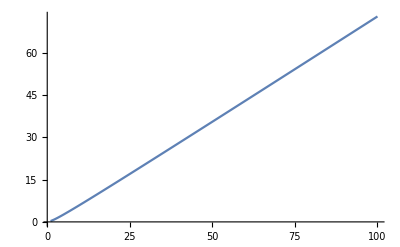

{{χ→InterpolatingFunction[…]}}

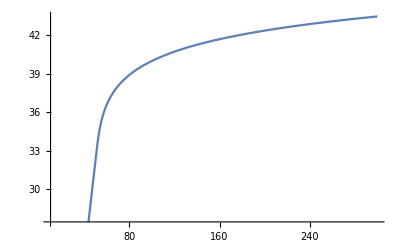

-Graphics3D-

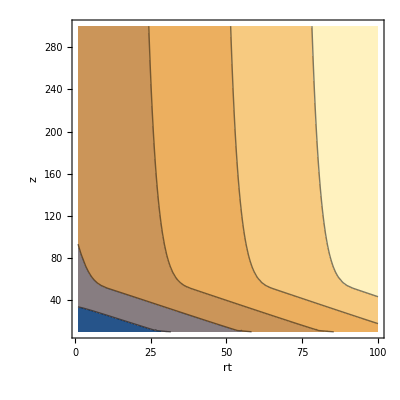

```mathematica
(*ξsol=DSolve[ξ''[r]+2/r ξ'[r]==Λ ξ[r],ξ[r],r]/.{zh->400,Λ->3}*)
ξsol=DSolve[{(ξ''[r]+2/r ξ'[r]==Λ ξ[r])/.{zh->400,Λ->3},ξ[1]==2,ξ'[1]==2},ξ,{r,1,100}]
Plot[Log[10,(ξ[r]/.ξsol[[1]])/.r->rt],{rt,1,100}]
χsol =NDSolve[{((1-z^4/zh^4)χ''[z]-4/z χ'[z]==-Λ χ[z])/.{zh->400,Λ->-3},χ[10]==0,χ'[10]==20},χ,{z,10,50}]
Plot[Log[10,(χ/.χsol[[1]])[z]],{z,10,300}]
Plot3D[Log[10,(χ/.χsol[[1]])[z] (ξ[r]/.ξsol[[1]])/.r->rt],{rt,1,100},{z,10,300},AxesLabel->{"r","z","t"}]
ContourPlot[Log[10,(χ/.χsol[[1]])[z] (ξ[r]/.ξsol[[1]])/.r->rt],{rt,1,100},{z,10,300},AxesLabel->Automatic]
```

{{ξ→Function[{r},(ⅇ^(-√3 (1+r)) ((3-2 √3) ⅇ^(2 √3)+(3+2 √3) ⅇ^(2 √3 r)))/(3 r)]}}

-Graphics-

{{χ→InterpolatingFunction[…]}}

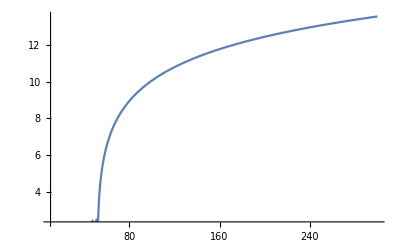

-Graphics3D-

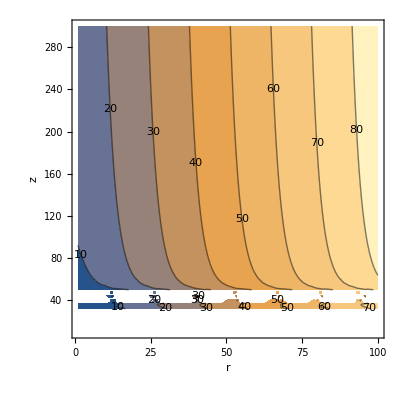

```mathematica
(*ξsol=DSolve[ξ''[r]+2/r ξ'[r]==Λ ξ[r],ξ[r],r]/.{zh->400,Λ->3}*)
ξsol=DSolve[{(ξ''[r]+2/r ξ'[r]==Λ ξ[r])/.{zh->300,Λ->3},ξ[1]==2,ξ'[1]==2},ξ,{r,1,100}]
Plot[Log[10,(ξ[r]/.ξsol[[1]])/.r->rt],{rt,1,100}]
χsol =NDSolve[{((1-z^4/zh^4)χ''[z]-4/z χ'[z]==Λ χ[z])/.{zh->300,Λ->-3},χ[10]==0,χ'[10]==20},χ,{z,10,50}]
Plot[Log[10,(χ/.χsol[[1]])[z]],{z,10,300}]
Plot3D[Log[10,(χ/.χsol[[1]])[z] (ξ[r]/.ξsol[[1]])/.r->rt],{rt,1,100},{z,10,300},AxesLabel->{"r","z","t"}]
ContourPlot[Log[10,(χ/.χsol[[1]])[z] (ξ[r]/.ξsol[[1]])/.r->rt],{rt,1,100},{z,10,300},AxesLabel->Automatic,ContourLabels->True,FrameLabel->{{"z",""},{"r","t(r,z) - z_h=300, z_b=0"}}]
```

```mathematica
(ξ[r]/.ξsol[[1]])/.r->1
```

1/3 ⅇ^(-2 √3) ((3-2 √3) ⅇ^(2 √3)+(3+2 √3) ⅇ^(2 √3))

```mathematica
χ[z]/.χsol[[1]]/.z->1/.x->1
```

[1]

```mathematica
χ[z_]:=DifferentialRoot[Function[{y,x},{-x zh^4 Λ y[x]+4 zh^4 y'[x]+(x^5-x zh^4) y''[x]==0,y[1]==C[1],y'[1]==C[2]}],Function[x,{{Re[x]≤Re[zh],Im[x]==Im[zh]}}]][z]
```

```mathematica
χ[z]
```

```mathematica
Plot[χ[z],{z,4,7}]
```

$Aborted

```mathematica
detg[r,z]=Sqrt[-1/(1-z^4/zh^4)+drt^2+(1-z^4/zh^4)dzt^2]/.trepl
(-ξ'[r])/ξ[r] D[detg[r,z],r]/detg[r,z]
-(1-z^4/zh^4)χ'[z]/χ[z] D[detg[r,z],z]/detg[r,z]
Simplify[%+%%]
```

√(-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2)

-(ξ'[r] (2 (1-z^4/zh^4) ξ[r] ξ'[r] χ'[z]^2+2 χ[z]^2 ξ'[r] ξ''[r]))/(2 ξ[r] (-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2))

-((1-z^4/zh^4) χ'[z] (-(4 z^3)/((1-z^4/zh^4)^2 zh^4)+2 χ[z] ξ'[r]^2 χ'[z]-(4 z^3 ξ[r]^2 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) ξ[r]^2 χ'[z] χ''[z]))/(2 χ[z] (-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2))

(-2 zh^4 ξ[r] χ'[z] (-z^3 zh^4+(z^4-zh^4)^2 χ[z] ξ'[r]^2 χ'[z])+zh^8 (z^4-zh^4) χ[z]^3 ξ'[r]^2 ξ''[r]+(z^4-zh^4)^2 ξ[r]^3 χ'[z]^2 (2 z^3 χ'[z]+(z^4-zh^4) χ''[z]))/(zh^4 ξ[r] χ[z] (-zh^8+zh^4 (-z^4+zh^4) χ[z]^2 ξ'[r]^2+(z^4-zh^4)^2 ξ[r]^2 χ'[z]^2))

```mathematica
-D[Log[ξ[r]],r]D[Log[detg[r,z]],r]
-(1-z^4/zh^4)D[Log[χ'[z]],z]D[Log[detg[r,z]],z]
```

-(ξ'[r] (2 (1-z^4/zh^4) ξ[r] ξ'[r] χ'[z]^2+2 χ[z]^2 ξ'[r] ξ''[r]))/(2 ξ[r] (-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2))

((-1+z^4/zh^4) χ''[z] (-(4 z^3)/((1-z^4/zh^4)^2 zh^4)+2 χ[z] ξ'[r]^2 χ'[z]-(4 z^3 ξ[r]^2 χ'[z]^2)/zh^4+2 (1-z^4/zh^4) ξ[r]^2 χ'[z] χ''[z]))/(2 χ'[z] (-1/(1-z^4/zh^4)+χ[z]^2 ξ'[r]^2+(1-z^4/zh^4) ξ[r]^2 χ'[z]^2))

```mathematica
sol=Solve[D[pzM,z]+D[prM,r]==0,ξ''[r]]
ξ2der=Simplify[ξ''[r]/.sol[[1]]]
CoefficientList[ξ2der,ξ'[r]];
ξcoeffs=%/.{χ'[z]->1/v,χ''[z]->0}
%%/.zh->Subscript[z, h]
```

{{ξ''[r]→(-2 z zh^4 M[r,z] χ[z] ξ'[r]+4 r zh^4 M[r,z] ξ[r] χ'[z]+r z^5 M[r,z] ξ[r] χ''[z]-r z zh^4 M[r,z] ξ[r] χ''[z]-r z^5 ξ[r] χ'[z] M^(0,1)[r,z]+r z zh^4 ξ[r] χ'[z] M^(0,1)[r,z]+r z zh^4 χ[z] ξ'[r] M^(1,0)[r,z])/(r z zh^4 M[r,z] χ[z])}}

(M[r,z] (-2 z zh^4 χ[z] ξ'[r]+r ξ[r] (4 zh^4 χ'[z]+z (z^4-zh^4) χ''[z]))+r z ((-z^4+zh^4) ξ[r] χ'[z] M^(0,1)[r,z]+zh^4 χ[z] ξ'[r] M^(1,0)[r,z]))/(r z zh^4 M[r,z] χ[z])

{(4 ξ[r])/(v z χ[z])+((-z^4+zh^4) ξ[r] M^(0,1)[r,z])/(v zh^4 M[r,z] χ[z]),-2/r+(M^(1,0)[r,z])/M[r,z]}

{(ξ[r] (4 z_h^4 χ'[z]+z (z^4-z_h^4) χ''[z]))/(z z_h^4 χ[z])+((-z^4+z_h^4) ξ[r] χ'[z] M^(0,1)[r,z])/(M[r,z] z_h^4 χ[z]),-2/r+(M^(1,0)[r,z])/M[r,z]}

```mathematica
(pr^2+pz^2)(( r^2 l^4/z^4)^-2 L/.trepl)^2// Simplify
```

(zh^8 χ[z]^2 ξ'[r]^2+(z^4-zh^4)^2 ξ[r]^2 χ'[z]^2)/zh^8

```mathematica
(l^4 r^2 (1-z^4/zh^4)  χ'[z]/χ[z])/(z^4 √(-1/((1-z^4/zh^4)χ[z]^2 ξ[r]^2)+ ξ'[r]^2/ξ[r]^2+(1-z^4/zh^4)  χ'[z]^2/χ[z]^2))
(l^4 r^2 ξ'[r]/ξ[r])/(z^4 √(-1/((1-z^4/zh^4)χ[z]^2 ξ[r]^2)+ ξ'[r]^2/ξ[r]^2+(1-z^4/zh^4)  χ'[z]^2/χ[z]^2))
```

(l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^4 χ[z] √(-1/((1-z^4/zh^4) ξ[r]^2 χ[z]^2)+ξ'[r]^2/ξ[r]^2+((1-z^4/zh^4) χ'[z]^2)/χ[z]^2))

(l^4 r^2 ξ'[r])/(z^4 ξ[r] √(-1/((1-z^4/zh^4) ξ[r]^2 χ[z]^2)+ξ'[r]^2/ξ[r]^2+((1-z^4/zh^4) χ'[z]^2)/χ[z]^2))

```mathematica
D[pz,z]//Simplify
D[pr,r]//Simplify
```

-(l^4 r^2 ξ[r] (M[z,r] (4 zh^4 χ'[z]+z (z^4-zh^4) χ''[z])+z (-z^4+zh^4) χ'[z] M^(1,0)[z,r]))/(z^5 zh^4 M[z,r]^2)

(l^4 r χ[z] (M[z,r] (2 ξ'[r]+r ξ''[r])-r ξ'[r] M^(0,1)[z,r]))/(z^4 M[z,r]^2)

```mathematica
Simplify[D[pz,z]+D[pr,r]==0]
%[[1]] Denominator[% [[1]]]/(χ[z]^2 ξ[r]^2)
```

(l r (M[z,r] (-z zh^4 χ[z] (2 ξ'[r]+r ξ''[r])+r ξ[r] (4 zh^4 χ'[z]+z (z^4-zh^4) χ''[z]))+r z (zh^4 χ[z] ξ'[r] M^(0,1)[z,r]+(-z^4+zh^4) ξ[r] χ'[z] M^(1,0)[z,r])))/(z zh M[z,r])==0

(l r (M[z,r] (-z zh^4 χ[z] (2 ξ'[r]+r ξ''[r])+r ξ[r] (4 zh^4 χ'[z]+z (z^4-zh^4) χ''[z]))+r z (zh^4 χ[z] ξ'[r] M^(0,1)[z,r]+(-z^4+zh^4) ξ[r] χ'[z] M^(1,0)[z,r])))/(ξ[r]^2 χ[z]^2)

```mathematica
sol=Solve[D[pz,z]+D[pr,r]==0,ξ''[r]]
ξ2der=Simplify[ξ''[r]/.sol[[1]]]
CoefficientList[ξ2der,ξ'[r]];
ξcoeffs=%/.{χ'[z]->1/v,χ''[z]->0}
%%/.zh->Subscript[z, h]
```

{{ξ''[r]→(-2 z zh^4 M[z,r] χ[z] ξ'[r]+4 r zh^4 M[z,r] ξ[r] χ'[z]+r z^5 M[z,r] ξ[r] χ''[z]-r z zh^4 M[z,r] ξ[r] χ''[z]+r z zh^4 χ[z] ξ'[r] M^(0,1)[z,r]-r z^5 ξ[r] χ'[z] M^(1,0)[z,r]+r z zh^4 ξ[r] χ'[z] M^(1,0)[z,r])/(r z zh^4 M[z,r] χ[z])}}

(M[z,r] (-2 z zh^4 χ[z] ξ'[r]+r ξ[r] (4 zh^4 χ'[z]+z (z^4-zh^4) χ''[z]))+r z (zh^4 χ[z] ξ'[r] M^(0,1)[z,r]+(-z^4+zh^4) ξ[r] χ'[z] M^(1,0)[z,r]))/(r z zh^4 M[z,r] χ[z])

{(4 ξ[r])/(v z χ[z])+((-z^4+zh^4) ξ[r] M^(1,0)[z,r])/(v zh^4 M[z,r] χ[z]),-2/r+(M^(0,1)[z,r])/M[z,r]}

{(ξ[r] (4 z_h^4 χ'[z]+z (z^4-z_h^4) χ''[z]))/(z z_h^4 χ[z])+((-z^4+z_h^4) ξ[r] χ'[z] M^(1,0)[z,r])/(M[z,r] z_h^4 χ[z]),-2/r+(M^(0,1)[z,r])/M[z,r]}

```mathematica
sol=Solve[D[pz,z]+D[pr,r]==0,χ''[z]]
χ2der=Simplify[χ''[z]/.sol[[1]]]
Simplify[CoefficientList[χ2der,χ'[z]]]
```

{{χ''[z]→(-(2 l^4 r^2 χ'[z])/(z (1-z^4/zh^4) zh^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(2 l^4 r^2 (1-z^4/zh^4) χ'[z]^3)/(z zh^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(2 l^4 r ξ'[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^5 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(4 l^4 r^2 χ'[z])/(z zh^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2))+(l^4 r^2 ξ'[r]^2 ξ''[r])/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))-(l^4 r^2 ξ''[r])/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)))/(-(l^4 r^2 (1-z^4/zh^4)^2 χ'[z]^2)/(z^4 (-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)^(3/2))+(l^4 r^2 (1-z^4/zh^4))/(z^4 √(-1/(1-z^4/zh^4)+ξ'[r]^2+(1-z^4/zh^4) χ'[z]^2)))}}

1/(r z zh^4 (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2))(2 z zh^8 (z^4-zh^4) ξ'[r]^3+4 r zh^8 (-z^4+zh^4) ξ'[r]^2 χ'[z]-2 z zh^4 ξ'[r] (-zh^8+(z^4-zh^4)^2 χ'[z]^2)-r (2 zh^8 (z^4+2 zh^4) χ'[z]+2 (z^4-2 zh^4) (z^4-zh^4)^2 χ'[z]^3-z zh^12 ξ''[r]+z zh^4 (z^4-zh^4)^2 χ'[z]^2 ξ''[r]))

{(2 zh^8 ξ'[r]+2 zh^4 (z^4-zh^4) ξ'[r]^3+r zh^8 ξ''[r])/(r (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2)),-(2 zh^4 (z^4+2 zh^4+2 (z^4-zh^4) ξ'[r]^2))/(z (z^4-zh^4) (zh^4+(z^4-zh^4) ξ'[r]^2)),((z^4-zh^4) (2 ξ'[r]+r ξ''[r]))/(r (-zh^4+(-z^4+zh^4) ξ'[r]^2)),-(2 (z^8-3 z^4 zh^4+2 zh^8))/(z zh^4 (zh^4+(z^4-zh^4) ξ'[r]^2))}

## AdS Painleve for handling coordinate singularity on the horizon

#### finding the measure

This is for function of z, but this will make z dependent on t hat, which is a function of both t and z. So painleve will only work if we use r for this instead

```mathematica
Clear[zh]
f[z_]:=1-z^4/zh^4
met5DPL = l^2/z^2{{-f[z],z^2/zh^2,0,0,0},{z^2/zh^2,1,0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
X = {t,z[r,t],r,θ,ϕ};
x= {t,r,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}];
Transpose[JXx].(met5DPL/.z->z[r,t]).JXx  //MatrixForm 
Simplify[-Det[%] z[r,t]^8/(l^8 r^4 Sin[θ]^2)]
```

((l^2 (-1+z^4/zh^4))/z^2 | l^2/zh^2 | 0 | 0 | 0
l^2/zh^2 | l^2/z^2 | 0 | 0 | 0
0 | 0 | l^2/z^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

((l^2 (-1+z[r,t]^4/zh^4))/z[r,t]^2+(l^2 z^(0,1)[r,t])/zh^2+z^(0,1)[r,t] (l^2/zh^2+(l^2 z^(0,1)[r,t])/z[r,t]^2) | (l^2/zh^2+(l^2 z^(0,1)[r,t])/z[r,t]^2) z^(1,0)[r,t] | 0 | 0
(l^2 z^(1,0)[r,t])/zh^2+(l^2 z^(0,1)[r,t] z^(1,0)[r,t])/z[r,t]^2 | l^2/z[r,t]^2+(l^2 (z^(1,0)[r,t])^2)/z[r,t]^2 | 0 | 0
0 | 0 | (l^2 r^2)/z[r,t]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[r,t]^2)

1-z[r,t]^4/zh^4-(2 z[r,t]^2 z^(0,1)[r,t])/zh^2-(z^(0,1)[r,t])^2+(z^(1,0)[r,t])^2

```mathematica
Clear[zh]
f[z_]:=1-z^4/zh^4
met5DPL = l^2/z^2{{-f[z],z^2/zh^2,0,0,0},{z^2/zh^2,1,0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
X = {t,z,r[t,z],θ,ϕ};
x= {t,z,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}];
Transpose[JXx].(met5DPL/.r->r[t,z]).JXx  //MatrixForm 
Measure=Simplify[Sqrt[-Det[%] z^8/(l^8 r[t,z]^4 Sin[θ]^2)]]
```

((l^2 (-1+z^4/zh^4))/z^2 | l^2/zh^2 | 0 | 0 | 0
l^2/zh^2 | l^2/z^2 | 0 | 0 | 0
0 | 0 | l^2/z^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

((l^2 (-1+z^4/zh^4))/z^2+(l^2 (r^(1,0)[t,z])^2)/z^2 | l^2/zh^2+(l^2 r^(0,1)[t,z] r^(1,0)[t,z])/z^2 | 0 | 0
l^2/zh^2+(l^2 r^(0,1)[t,z] r^(1,0)[t,z])/z^2 | l^2/z^2+(l^2 (r^(0,1)[t,z])^2)/z^2 | 0 | 0
0 | 0 | (l^2 r[t,z]^2)/z^2 | 0
0 | 0 | 0 | (l^2 r[t,z]^2 Sin[θ]^2)/z^2)

√(1+(1-z^4/zh^4) (r^(0,1)[t,z])^2+(2 z^2 r^(0,1)[t,z] r^(1,0)[t,z])/zh^2-(r^(1,0)[t,z])^2)

```mathematica
1+D[r[t,z],z]^2 - (z^2/zh^2 D[r[t,z],z] - D[r[t,z],t])^2
Simplify[%/Measure^2]
```

1+(r^(0,1)[t,z])^2-((z^2 r^(0,1)[t,z])/zh^2-r^(1,0)[t,z])^2

1

```mathematica
L=PowerExpand[(z^8/(l^8 r[t,z]^4))^(-1/2)] Measure
```

(l^4 r[t,z]^2 √(1+(1-z^4/zh^4) (r^(0,1)[t,z])^2+(2 z^2 r^(0,1)[t,z] r^(1,0)[t,z])/zh^2-(r^(1,0)[t,z])^2))/z^4

```mathematica
Simplify[D[L,D[r[t,z],z]]]
Simplify[D[L,D[r[t,z],t]]]
```

(l^4 r[t,z]^2 ((-z^4+zh^4) r^(0,1)[t,z]+z^2 zh^2 r^(1,0)[t,z]))/(z^4 zh^4 √(1+(1-z^4/zh^4) (r^(0,1)[t,z])^2+(2 z^2 r^(0,1)[t,z] r^(1,0)[t,z])/zh^2-(r^(1,0)[t,z])^2))

(l^4 r[t,z]^2 (z^2 r^(0,1)[t,z]-zh^2 r^(1,0)[t,z]))/(z^4 zh^2 √(1+(1-z^4/zh^4) (r^(0,1)[t,z])^2+(2 z^2 r^(0,1)[t,z] r^(1,0)[t,z])/zh^2-(r^(1,0)[t,z])^2))

```mathematica
pzM =Numerator[Simplify[D[L,D[r[t,z],z]]]]/(z^4 zh^4 M[t,z])
ptM = Numerator[D[L,D[r[t,z],t]]]/(z^4 M[t,z])
dLdr = D[L,r[t,z]]
```

(l^4 r[t,z]^2 ((-z^4+zh^4) r^(0,1)[t,z]+z^2 zh^2 r^(1,0)[t,z]))/(z^4 zh^4 M[t,z])

(l^4 r[t,z]^2 ((2 z^2 r^(0,1)[t,z])/zh^2-2 r^(1,0)[t,z]))/(z^4 M[t,z])

(2 l^4 r[t,z] √(1+(1-z^4/zh^4) (r^(0,1)[t,z])^2+(2 z^2 r^(0,1)[t,z] r^(1,0)[t,z])/zh^2-(r^(1,0)[t,z])^2))/z^4

```mathematica
(D[pzM,z]-D[ptM,t]-dLdr) M[t,z] z^4/(l^4 r^2)
```

1/(l^4 r^2)z^4 M[t,z] ((l^4 r[t,z]^2 M^(1,0)[t,z] ((2 z^2 r^(0,1)[t,z])/zh^2-2 r^(1,0)[t,z]))/(z^4 M[t,z]^2)-(2 l^4 r[t,z] ((2 z^2 r^(0,1)[t,z])/zh^2-2 r^(1,0)[t,z]) r^(1,0)[t,z])/(z^4 M[t,z])-(4 l^4 r[t,z]^2 ((-z^4+zh^4) r^(0,1)[t,z]+z^2 zh^2 r^(1,0)[t,z]))/(z^5 zh^4 M[t,z])-(l^4 r[t,z]^2 M^(0,1)[t,z] ((-z^4+zh^4) r^(0,1)[t,z]+z^2 zh^2 r^(1,0)[t,z]))/(z^4 zh^4 M[t,z]^2)+(2 l^4 r[t,z] r^(0,1)[t,z] ((-z^4+zh^4) r^(0,1)[t,z]+z^2 zh^2 r^(1,0)[t,z]))/(z^4 zh^4 M[t,z])-(2 l^4 r[t,z] √(1+(1-z^4/zh^4) (r^(0,1)[t,z])^2+(2 z^2 r^(0,1)[t,z] r^(1,0)[t,z])/zh^2-(r^(1,0)[t,z])^2))/z^4+(l^4 r[t,z]^2 (-4 z^3 r^(0,1)[t,z]+(-z^4+zh^4) r^(0,2)[t,z]+2 z zh^2 r^(1,0)[t,z]+z^2 zh^2 r^(1,1)[t,z]))/(z^4 zh^4 M[t,z])-(l^4 r[t,z]^2 ((2 z^2 r^(1,1)[t,z])/zh^2-2 r^(2,0)[t,z]))/(z^4 M[t,z]))

## Velocity ansatz

### z=Z(r-v(r)t)

```mathematica
f[z_]:= (1-z^4/zh^4)
sqrtmg = Sqrt[f[z]+drz^2-1/f[z] dtz^2]
L = 4 π σ r^2 l^4/z^4 sqrtmg
zrepl = {z->z[r,t],drz->D[z[r,t],r],dtz->D[z[r,t],t]}
```

√(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4)

(4 l^4 π r^2 √(1+drz^2-dtz^2/(1-z^4/zh^4)-z^4/zh^4) σ)/z^4

{z→z[r,t],drz→z^(1,0)[r,t],dtz→z^(0,1)[r,t]}

```mathematica
HoldForm[L]==(L/.zrepl/.vrepl )
```

L==(4 l^4 π r^2 σ √(1-Z[r-t vr[r]]^4/zh^4+(1-t vr[r])^2 Z'[r-t vr[r]]^2-(vr[r]^2 Z'[r-t vr[r]]^2)/(1-Z[r-t vr[r]]^4/zh^4)))/Z[r-t vr[r]]^4

```mathematica
D[L,z]/.zrepl
D[L,drz]/.zrepl
D[L,dtz]/.zrepl
```

(2 l^4 π r^2 σ (-(4 z[r,t]^3)/zh^4-(4 z[r,t]^3 (z^(0,1)[r,t])^2)/(zh^4 (1-z[r,t]^4/zh^4)^2)))/(z[r,t]^4 √(1-z[r,t]^4/zh^4-((z^(0,1)[r,t])^2)/(1-z[r,t]^4/zh^4)+(z^(1,0)[r,t])^2))-(16 l^4 π r^2 σ √(1-z[r,t]^4/zh^4-((z^(0,1)[r,t])^2)/(1-z[r,t]^4/zh^4)+(z^(1,0)[r,t])^2))/z[r,t]^5

(4 l^4 π r^2 σ z^(1,0)[r,t])/(z[r,t]^4 √(1-z[r,t]^4/zh^4-((z^(0,1)[r,t])^2)/(1-z[r,t]^4/zh^4)+(z^(1,0)[r,t])^2))

-(4 l^4 π r^2 σ z^(0,1)[r,t])/(z[r,t]^4 (1-z[r,t]^4/zh^4) √(1-z[r,t]^4/zh^4-((z^(0,1)[r,t])^2)/(1-z[r,t]^4/zh^4)+(z^(1,0)[r,t])^2))

define an auxiliary variable for the measure

```mathematica
dLdz=(2 l^4 π r^2 σ (-((4 z[r, t]^3)/zh^4) - (4 z[r, t]^3 
Derivative[0,1][z][r, t]^2)/(zh^4 (1 - z[r, t]^4/zh^4)^2)))/(
 z[r, t]^4  M[r,t]) - (
 16 l^4 π r^2 σ M[r,t])/z[r, t]^5

pr = Numerator[D[L,drz]/.zrepl]/(z[r,t]^4 M[r,t])
pt = Numerator[D[L,dtz]/.zrepl]/(z[r,t]^4 f[z[r,t]]M[r,t])
D[pr,r]
D[pt,t]
```

-(16 l^4 π r^2 σ M[r,t])/z[r,t]^5+(2 l^4 π r^2 σ (-(4 z[r,t]^3)/zh^4-(4 z[r,t]^3 (z^(0,1)[r,t])^2)/(zh^4 (1-z[r,t]^4/zh^4)^2)))/(M[r,t] z[r,t]^4)

(4 l^4 π r^2 σ z^(1,0)[r,t])/(M[r,t] z[r,t]^4)

-(4 l^4 π r^2 σ z^(0,1)[r,t])/(M[r,t] z[r,t]^4 (1-z[r,t]^4/zh^4))

(8 l^4 π r σ z^(1,0)[r,t])/(M[r,t] z[r,t]^4)-(4 l^4 π r^2 σ M^(1,0)[r,t] z^(1,0)[r,t])/(M[r,t]^2 z[r,t]^4)-(16 l^4 π r^2 σ (z^(1,0)[r,t])^2)/(M[r,t] z[r,t]^5)+(4 l^4 π r^2 σ z^(2,0)[r,t])/(M[r,t] z[r,t]^4)

(4 l^4 π r^2 σ M^(0,1)[r,t] z^(0,1)[r,t])/(M[r,t]^2 z[r,t]^4 (1-z[r,t]^4/zh^4))-(16 l^4 π r^2 σ (z^(0,1)[r,t])^2)/(zh^4 M[r,t] z[r,t] (1-z[r,t]^4/zh^4)^2)+(16 l^4 π r^2 σ (z^(0,1)[r,t])^2)/(M[r,t] z[r,t]^5 (1-z[r,t]^4/zh^4))-(4 l^4 π r^2 σ z^(0,2)[r,t])/(M[r,t] z[r,t]^4 (1-z[r,t]^4/zh^4))

Now make the velocity ansatz

```mathematica
vrepl = {z[r,t]->Z[r-vr[r] t],D[z[r,t],r]->(1-vr[r] t)Z'[r-vr[r] t],D[z[r,t],{r,2}]->vr''[r] t Z'[r-vr[r] t]+(1-vr[r] t)^2 Z''[r-vr[r] t] ,D[z[r,t],t]->- vr[r]Z'[r-vr[r] t],D[z[r,t],{t,2}]->vr[r]^2 Z''[r-vr[r] t]}
vreplsimparg = {z[r,t]->Z,D[z[r,t],r]->(1-vr[r] t)Z',D[z[r,t],{r,2}]->vr''[r] t Z'+(1-vr[r] t)^2 Z'' ,D[z[r,t],t]->- vr[r]Z',D[z[r,t],{t,2}]->vr[r]^2 Z''}
```

{z[r,t]→Z[r-t vr[r]],z^(1,0)[r,t]→(1-t vr[r]) Z'[r-t vr[r]],z^(2,0)[r,t]→t Z'[r-t vr[r]] vr''[r]+(1-t vr[r])^2 Z''[r-t vr[r]],z^(0,1)[r,t]→-vr[r] Z'[r-t vr[r]],z^(0,2)[r,t]→vr[r]^2 Z''[r-t vr[r]]}

{z[r,t]→Z,z^(1,0)[r,t]→(1-t vr[r]) Z',z^(2,0)[r,t]→(1-t vr[r])^2 Z''+t Z' vr''[r],z^(0,1)[r,t]→-vr[r] Z',z^(0,2)[r,t]→vr[r]^2 Z''}

```mathematica
D[Z[r-vr[r] t],{r,2}]
```

-t Z'[r-t vr[r]] vr''[r]+(1-t vr'[r])^2 Z''[r-t vr[r]]

```mathematica
dzterms = M[r,t] z[r,t]^4/(4 π σ r^2 l^4)dLdz //Simplify// Expand
drterms =M[r,t] z[r,t]^4/(4 π σ r^2 l^4)D[pr,r]//Simplify
dtterms =M[r,t] z[r,t]^4/(4 π σ r^2 l^4)D[pt ,t]//Simplify// Expand
```

-(4 zh^8 M[r,t]^2)/(z[r,t] (zh^4-z[r,t]^4)^2)-(2 zh^4 z[r,t]^3)/((zh^4-z[r,t]^4)^2)+(8 zh^4 M[r,t]^2 z[r,t]^3)/((zh^4-z[r,t]^4)^2)+(4 z[r,t]^7)/((zh^4-z[r,t]^4)^2)-(4 M[r,t]^2 z[r,t]^7)/((zh^4-z[r,t]^4)^2)-(2 z[r,t]^11)/(zh^4 (zh^4-z[r,t]^4)^2)-(2 zh^4 z[r,t]^3 (z^(0,1)[r,t])^2)/((zh^4-z[r,t]^4)^2)

(2/r-(M^(1,0)[r,t])/M[r,t]) z^(1,0)[r,t]-(4 (z^(1,0)[r,t])^2)/z[r,t]+z^(2,0)[r,t]

(zh^8 M^(0,1)[r,t] z^(0,1)[r,t])/(M[r,t] (zh^4-z[r,t]^4)^2)-(zh^4 z[r,t]^4 M^(0,1)[r,t] z^(0,1)[r,t])/(M[r,t] (zh^4-z[r,t]^4)^2)+(4 zh^8 (z^(0,1)[r,t])^2)/(z[r,t] (zh^4-z[r,t]^4)^2)-(8 zh^4 z[r,t]^3 (z^(0,1)[r,t])^2)/((zh^4-z[r,t]^4)^2)-(zh^8 z^(0,2)[r,t])/((zh^4-z[r,t]^4)^2)+(zh^4 z[r,t]^4 z^(0,2)[r,t])/((zh^4-z[r,t]^4)^2)

```mathematica
dzterms/.vrepl
drterms/.vrepl
dtterms/.vrepl
```

-(4 zh^8 M[r,t]^2)/(Z[r-t vr[r]] (zh^4-Z[r-t vr[r]]^4)^2)-(2 zh^4 Z[r-t vr[r]]^3)/((zh^4-Z[r-t vr[r]]^4)^2)+(8 zh^4 M[r,t]^2 Z[r-t vr[r]]^3)/((zh^4-Z[r-t vr[r]]^4)^2)+(4 Z[r-t vr[r]]^7)/((zh^4-Z[r-t vr[r]]^4)^2)-(4 M[r,t]^2 Z[r-t vr[r]]^7)/((zh^4-Z[r-t vr[r]]^4)^2)-(2 Z[r-t vr[r]]^11)/(zh^4 (zh^4-Z[r-t vr[r]]^4)^2)-(2 zh^4 vr[r]^2 Z[r-t vr[r]]^3 Z'[r-t vr[r]]^2)/((zh^4-Z[r-t vr[r]]^4)^2)

-(4 (1-t vr[r])^2 Z'[r-t vr[r]]^2)/Z[r-t vr[r]]+t Z'[r-t vr[r]] vr''[r]+(1-t vr[r])^2 Z''[r-t vr[r]]+(1-t vr[r]) Z'[r-t vr[r]] (2/r-(M^(1,0)[r,t])/M[r,t])

(4 zh^8 vr[r]^2 Z'[r-t vr[r]]^2)/(Z[r-t vr[r]] (zh^4-Z[r-t vr[r]]^4)^2)-(8 zh^4 vr[r]^2 Z[r-t vr[r]]^3 Z'[r-t vr[r]]^2)/((zh^4-Z[r-t vr[r]]^4)^2)-(zh^8 vr[r]^2 Z''[r-t vr[r]])/((zh^4-Z[r-t vr[r]]^4)^2)+(zh^4 vr[r]^2 Z[r-t vr[r]]^4 Z''[r-t vr[r]])/((zh^4-Z[r-t vr[r]]^4)^2)-(zh^8 vr[r] Z'[r-t vr[r]] M^(0,1)[r,t])/(M[r,t] (zh^4-Z[r-t vr[r]]^4)^2)+(zh^4 vr[r] Z[r-t vr[r]]^4 Z'[r-t vr[r]] M^(0,1)[r,t])/(M[r,t] (zh^4-Z[r-t vr[r]]^4)^2)

```mathematica
Simplify[(zh^12 f[Z]^2(drterms - dtterms - dzterms) /.vreplsimparg) ]== 0
CoefficientList[%,Z'']
```

(4 zh^4 (Z^4-zh^4)^2 M[r,t]^2)/Z-(2 zh^4 (2 (Z^4-zh^4)^2-4 t (Z^4-zh^4)^2 vr[r]+(-5 Z^4 zh^4+2 zh^8+2 t^2 (Z^4-zh^4)^2) vr[r]^2) (Z')^2)/Z+(Z^4-zh^4) (2 Z^3 (Z^4-zh^4)-zh^4 (-Z^4+zh^4+2 t (Z^4-zh^4) vr[r]+(zh^4+t^2 (-Z^4+zh^4)) vr[r]^2) Z'')+(zh^4 (Z^4-zh^4)^2 Z' (2-2 t vr[r]+r t vr''[r]))/r+(zh^4 (-Z^4+zh^4) Z' ((Z^4-zh^4) M^(1,0)[r,t]+vr[r] (zh^4 M^(0,1)[r,t]+t (-Z^4+zh^4) M^(1,0)[r,t])))/M[r,t]==0

{(4 zh^4 (Z^4-zh^4)^2 M[r,t]^2)/Z-(2 zh^4 (2 (Z^4-zh^4)^2-4 t (Z^4-zh^4)^2 vr[r]+(-5 Z^4 zh^4+2 zh^8+2 t^2 (Z^4-zh^4)^2) vr[r]^2) (Z')^2)/Z+(Z^4-zh^4) (2 Z^3 (Z^4-zh^4)-zh^4 (-Z^4+zh^4+2 t (Z^4-zh^4) vr[r]+(zh^4+t^2 (-Z^4+zh^4)) vr[r]^2) Z'')+(zh^4 (Z^4-zh^4)^2 Z' (2-2 t vr[r]+r t vr''[r]))/r+(zh^4 (-Z^4+zh^4) Z' ((Z^4-zh^4) M^(1,0)[r,t]+vr[r] (zh^4 M^(0,1)[r,t]+t (-Z^4+zh^4) M^(1,0)[r,t])))/M[r,t]==0}

### t(r,z)=(r-χ(z))/(v_r(r))

#### eom

```mathematica
met = l^2/z^2{{-(1-z^4/zh^4) dzt dzt+1/(1-z^4/zh^4),-(1-z^4/zh^4) dzt drt,0,0},{-(1-z^4/zh^4) drt dzt,-(1-z^4/zh^4) drt drt  + 1 ,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
-Det[met]
Simplify[% z^8/(l^8 r^4 Sin[θ]^2)]
Simplify[%  /(drt^2 - 1/(1-z^4/zh^4) + (1-z^4/zh^4) dzt^2)]
```

((l^2 (1/(1-z^4/zh^4)+dzt^2 (-1+z^4/zh^4)))/z^2 | (drt dzt l^2 (-1+z^4/zh^4))/z^2 | 0 | 0
(drt dzt l^2 (-1+z^4/zh^4))/z^2 | (l^2 (1+drt^2 (-1+z^4/zh^4)))/z^2 | 0 | 0
0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

(dzt^2 l^8 r^4 Sin[θ]^2)/z^8-(l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))+(drt^2 l^8 r^4 Sin[θ]^2)/(z^8 (1-z^4/zh^4))-(dzt^2 l^8 r^4 Sin[θ]^2)/(z^4 zh^4)-(drt^2 l^8 r^4 Sin[θ]^2)/(z^4 (1-z^4/zh^4) zh^4)

drt^2+dzt^2 (1-z^4/zh^4)+zh^4/(z^4-zh^4)

1

```mathematica
Measure = Sqrt[-1/(1-z^4/zh^4)+drt^2+(1-z^4/zh^4)dzt^2]
L = r^2 l^4/z^4 Measure
```

√(drt^2-1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4))

(l^4 r^2 √(drt^2-1/(1-z^4/zh^4)+dzt^2 (1-z^4/zh^4)))/z^4

```mathematica
D[(r-χ[z])/v[r],r]
```

1/v[r]-((r-χ[z]) v'[r])/v[r]^2

```mathematica
trepl ={drt->D[(r-χ[z])/v[r],r],dzt->D[(r-χ[z])/v[r],z]}
```

{drt→1/v[r]-((r-χ[z]) v'[r])/v[r]^2,dzt→-χ'[z]/v[r]}

```mathematica
pz =D[L,dzt]/.trepl
pr = D[L,drt]/.trepl
```

-(l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^4 v[r] √(-1/(1-z^4/zh^4)+(1/v[r]-((r-χ[z]) v'[r])/v[r]^2)^2+((1-z^4/zh^4) χ'[z]^2)/v[r]^2))

(l^4 r^2 (1/v[r]-((r-χ[z]) v'[r])/v[r]^2))/(z^4 √(-1/(1-z^4/zh^4)+(1/v[r]-((r-χ[z]) v'[r])/v[r]^2)^2+((1-z^4/zh^4) χ'[z]^2)/v[r]^2))

Define Auxiliary variable

```mathematica
pz=D[L,dzt] Measure/M[r,z]/.trepl
pr=D[L,drt] Measure/M[r,z]/.trepl
dLdt = D[L,t]
```

-(l^4 r^2 (1-z^4/zh^4) χ'[z])/(z^4 M[r,z] v[r])

(l^4 r^2 (1/v[r]-((r-χ[z]) v'[r])/v[r]^2))/(z^4 M[r,z])

0

```mathematica
D[pz,z] M[r,z] v[r] z^4/(l^4 r^2)//Simplify
v[r]^2(D[pr,r]M[r,z] v[r] z^4/(l^4 r^2))//Simplify (*v[r]^2 just to make it more readible*)
```

((z^4-zh^4) χ''[z]+χ'[z] ((4 zh^4)/z+((-z^4+zh^4) M^(0,1)[r,z])/M[r,z]))/zh^4

(2 v[r]^2+2 r (r-χ[z]) v'[r]^2+v[r] ((-4 r+2 χ[z]) v'[r]+r (-r+χ[z]) v''[r]))/r-(v[r] (v[r]+(-r+χ[z]) v'[r]) M^(1,0)[r,z])/M[r,z]

```mathematica
D[Log[Measure/.trepl],r]
```

(-(2 (1-z^4/zh^4) v'[r] χ'[z]^2)/v[r]^3+2 (1/v[r]-((r-χ[z]) v'[r])/v[r]^2) (-(2 v'[r])/v[r]^2+(2 (r-χ[z]) v'[r]^2)/v[r]^3-((r-χ[z]) v''[r])/v[r]^2))/(2 (-1/(1-z^4/zh^4)+(1/v[r]-((r-χ[z]) v'[r])/v[r]^2)^2+((1-z^4/zh^4) χ'[z]^2)/v[r]^2))

#### finding the measure

```mathematica
Clear[zh]
f[z_]:=1-z^4/zh^4
met5DPL = l^2/z^2{{-f[z],0,0,0,0},{0,1/f[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
X = {th[r,z]+r/v[r],z,r,θ,ϕ}; (*t=th+r/v[r]*)
x= {z,r,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}];
Transpose[JXx].(met5DPL).JXx  //MatrixForm 
Simplify[-Det[%] z^8/(l^8 r^4 Sin[θ]^2)]
Measure = Sqrt[%]
```

((l^2 (-1+z^4/zh^4))/z^2 | 0 | 0 | 0 | 0
0 | l^2/(z^2 (1-z^4/zh^4)) | 0 | 0 | 0
0 | 0 | l^2/z^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

(l^2/(z^2 (1-z^4/zh^4))+(l^2 (-1+z^4/zh^4) (th^(0,1)[r,z])^2)/z^2 | (l^2 (-1+z^4/zh^4) th^(0,1)[r,z] (1/v[r]-(r v'[r])/v[r]^2+th^(1,0)[r,z]))/z^2 | 0 | 0
(l^2 (-1+z^4/zh^4) th^(0,1)[r,z] (1/v[r]-(r v'[r])/v[r]^2+th^(1,0)[r,z]))/z^2 | l^2/z^2+(l^2 (-1+z^4/zh^4) (1/v[r]-(r v'[r])/v[r]^2+th^(1,0)[r,z])^2)/z^2 | 0 | 0
0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

zh^4/(z^4-zh^4)+((-z^4+zh^4) (th^(0,1)[r,z])^2)/zh^4+((v[r]-r v'[r]+v[r]^2 th^(1,0)[r,z])^2)/v[r]^4

√(zh^4/(z^4-zh^4)+((-z^4+zh^4) (th^(0,1)[r,z])^2)/zh^4+((v[r]-r v'[r]+v[r]^2 th^(1,0)[r,z])^2)/v[r]^4)

```mathematica
threpl = {D[th[r,z],r]->-v'[r]/v[r]^2 χ[z],D[th[r,z],z]->v[r]χ'[z]}
Measure=Measure/.threpl
```

{th^(1,0)[r,z]→-(χ[z] v'[r])/v[r]^2,th^(0,1)[r,z]→v[r] χ'[z]}

√(zh^4/(z^4-zh^4)+(v[r]-r v'[r]-χ[z] v'[r])^2/v[r]^4+((-z^4+zh^4) v[r]^2 χ'[z]^2)/zh^4)

Maybe we can do a seperate variation for v[r], find it’s eoms. then we have two seperate coupled pdes. And maybe with knowledge that th is proportional to 1/v[r] will let us solve

Or maybe we can try this more generally, when we have a seperable solution, we can vary each function individually?

```mathematica
(D[Measure,v'[r]]-D[Measure,v[r]])Measure /.D[th[r,z],r]->(-v'[r])/v[r]^2 χ[z]//Simplify  (*v[r] eom*)
```

-(((-1+r) v[r]+2 r v'[r]) (v[r]-(r+χ[z]) v'[r]))/v[r]^5

We run into the issue of the ansatz being inconsistent again since now there is z dependence in the v[r] equation

unless we have that χ[z]=-r for all r

wait, no this is not true, we forgot derivatives

```mathematica
(Simplify[D[D[r^2 Measure,v'[r]] Measure/M[r,z],r]]-Simplify[D[Measure,v[r]] Measure/M[r,z]])
```

((v[r]-2 r v'[r]) (v[r]-r v'[r]+v[r]^2 th^(1,0)[r,z]))/(M[r,z] v[r]^5)+1/(M[r,z]^2 v[r]^5)r^2 (r v[r] M^(1,0)[r,z] (v[r]-r v'[r]+v[r]^2 th^(1,0)[r,z])+M[r,z] (-4 r^2 v'[r]^2+r v[r] (7 v'[r]+r v''[r])+v[r]^2 (-3+2 r v'[r] th^(1,0)[r,z])-v[r]^3 (3 th^(1,0)[r,z]+r th^(2,0)[r,z])))

```mathematica
pr = D[r^2 Measure,v'[r]]
Simplify[pr Measure/M[r,z]]
D[%,r]M[r,z] v[r]^4/r^2//Simplify
CoefficientList[%,χ[z]]
```

(r^2 (-r-χ[z]) (v[r]-r v'[r]-χ[z] v'[r]))/(v[r]^4 √(zh^4/(z^4-zh^4)+(v[r]-r v'[r]-χ[z] v'[r])^2/v[r]^4+((-z^4+zh^4) v[r]^2 χ'[z]^2)/zh^4))

(r^2 (r+χ[z]) (-v[r]+(r+χ[z]) v'[r]))/(M[r,z] v[r]^4)

v[r] (-3-(2 χ[z])/r)-(4 (r+χ[z])^2 v'[r]^2)/v[r]+((r+χ[z]) ((7 r+2 χ[z]) v'[r]+r (r+χ[z]) v''[r]))/r-((r+χ[z]) (-v[r]+(r+χ[z]) v'[r]) M^(1,0)[r,z])/M[r,z]

{-3 v[r]+7 r v'[r]-(4 r^2 v'[r]^2)/v[r]+r^2 v''[r]+(r v[r] M^(1,0)[r,z])/M[r,z]-(r^2 v'[r] M^(1,0)[r,z])/M[r,z],-(2 v[r])/r+9 v'[r]-(8 r v'[r]^2)/v[r]+2 r v''[r]+(v[r] M^(1,0)[r,z])/M[r,z]-(2 r v'[r] M^(1,0)[r,z])/M[r,z],(2 v'[r])/r-(4 v'[r]^2)/v[r]+v''[r]-(v'[r] M^(1,0)[r,z])/M[r,z]}

**** no need to substitute for D[th,r] before variation.

```mathematica
pr = D[1/z^4 Measure/.th[r,z]->(-χ[z])/v[r],χ'[z]]
Simplify[pr Measure/M[r,z]]
D[%,r]M[r,z] v[r]^4/r^2//Simplify
```

0

0

0

```mathematica
D[Log[Measure],r]
D[Log[Measure],z]
```

(-(4 v'[r] (v[r]-r v'[r]-χ[z] v'[r])^2)/v[r]^5+(2 (-z^4+zh^4) v[r] v'[r] χ'[z]^2)/zh^4+(2 (v[r]-r v'[r]-χ[z] v'[r]) (-r v''[r]-χ[z] v''[r]))/v[r]^4)/(2 (zh^4/(z^4-zh^4)+(v[r]-r v'[r]-χ[z] v'[r])^2/v[r]^4+((-z^4+zh^4) v[r]^2 χ'[z]^2)/zh^4))

(-(4 z^3 zh^4)/((z^4-zh^4)^2)-(2 v'[r] (v[r]-r v'[r]-χ[z] v'[r]) χ'[z])/v[r]^4-(4 z^3 v[r]^2 χ'[z]^2)/zh^4+(2 (-z^4+zh^4) v[r]^2 χ'[z] χ''[z])/zh^4)/(2 (zh^4/(z^4-zh^4)+(v[r]-r v'[r]-χ[z] v'[r])^2/v[r]^4+((-z^4+zh^4) v[r]^2 χ'[z]^2)/zh^4))

## Polyakov Action

```mathematica
Clear[zh]
f[z_]:=1-z^4/zh^4
met5DPL = l^2/z^2{{-f[z],0,0,0,0},{0,1/f[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
X = {t,z[r,t],r,θ,ϕ};
x= {t,r,θ,ϕ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,4}];
Transpose[JXx].(met5DPL/.z->z[r,t]).JXx  //MatrixForm 
Simplify[-Det[%] z[r,t]^8/(l^8 r^4 Sin[θ]^2)]
Simplify[CoefficientList[%,D[z[r,t],r]]]//Expand
```

((l^2 (-1+z^4/zh^4))/z^2 | 0 | 0 | 0 | 0
0 | l^2/(z^2 (1-z^4/zh^4)) | 0 | 0 | 0
0 | 0 | l^2/z^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

((l^2 (-1+z[r,t]^4/zh^4))/z[r,t]^2+(l^2 (z^(0,1)[r,t])^2)/(z[r,t]^2 (1-z[r,t]^4/zh^4)) | (l^2 z^(0,1)[r,t] z^(1,0)[r,t])/(z[r,t]^2 (1-z[r,t]^4/zh^4)) | 0 | 0
(l^2 z^(0,1)[r,t] z^(1,0)[r,t])/(z[r,t]^2 (1-z[r,t]^4/zh^4)) | l^2/z[r,t]^2+(l^2 (z^(1,0)[r,t])^2)/(z[r,t]^2 (1-z[r,t]^4/zh^4)) | 0 | 0
0 | 0 | (l^2 r^2)/z[r,t]^2 | 0
0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z[r,t]^2)

(z[r,t]^8-zh^4 z[r,t]^4 (2+(z^(1,0)[r,t])^2)+zh^8 (1-(z^(0,1)[r,t])^2+(z^(1,0)[r,t])^2))/(zh^8-zh^4 z[r,t]^4)

{zh^8/(zh^8-zh^4 z[r,t]^4)-(2 zh^4 z[r,t]^4)/(zh^8-zh^4 z[r,t]^4)+z[r,t]^8/(zh^8-zh^4 z[r,t]^4)-(zh^8 (z^(0,1)[r,t])^2)/(zh^8-zh^4 z[r,t]^4),0,1}

## Gauge Choice via Zwiebach

### find effective 2D action

```mathematica
Clear[zh]
f[z_]:=1-z^4/zh^4
(*met5DPL = r^2(l^2/z^2)^3{{-f[z],0,0},{0,1/f[z],0},{0,0,1}}*)
met5DPL = l^2/z^2{{-HoldForm[f[z]],0,0,0,0},{0,HoldForm[1/f[z]],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
(*X = {t[τ,σ],z[τ,σ],r[τ,σ]};*)
X = {t,z[t,σ],r[t,σ],θ,ϕ};
x= {t,σ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,2}];
Transpose[JXx].(met5DPL/.z->z[r,t]).JXx  //MatrixForm 
Simplify[-Det[%] ]
Simplify[CoefficientList[%,D[z[r,t],r]]]
```

(-(l^2 f[z])/z^2 | 0 | 0 | 0 | 0
0 | (l^2 1/f[z])/z^2 | 0 | 0 | 0
0 | 0 | l^2/z^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

(-(l^2 f[z[r,t]])/z[r,t]^2+(l^2 (r^(1,0)[t,σ])^2)/z[r,t]^2+(l^2 1/f[z[r,t]] (z^(1,0)[t,σ])^2)/z[r,t]^2 | (l^2 r^(0,1)[t,σ] r^(1,0)[t,σ])/z[r,t]^2+(l^2 1/f[z[r,t]] z^(0,1)[t,σ] z^(1,0)[t,σ])/z[r,t]^2
(l^2 r^(0,1)[t,σ] r^(1,0)[t,σ])/z[r,t]^2+(l^2 1/f[z[r,t]] z^(0,1)[t,σ] z^(1,0)[t,σ])/z[r,t]^2 | (l^2 (r^(0,1)[t,σ])^2)/z[r,t]^2+(l^2 1/f[z[r,t]] (z^(0,1)[t,σ])^2)/z[r,t]^2)

(l^4 (f[z[r,t]] ((r^(0,1)[t,σ])^2+1/f[z[r,t]] (z^(0,1)[t,σ])^2)-1/f[z[r,t]] (z^(0,1)[t,σ] r^(1,0)[t,σ]-r^(0,1)[t,σ] z^(1,0)[t,σ])^2))/z[r,t]^4

{(l^4 (f[z[r,t]] ((r^(0,1)[t,σ])^2+1/f[z[r,t]] (z^(0,1)[t,σ])^2)-1/f[z[r,t]] (z^(0,1)[t,σ] r^(1,0)[t,σ]-r^(0,1)[t,σ] z^(1,0)[t,σ])^2))/z[r,t]^4}

```mathematica
Clear[zh]
f[z_]:=1-z^4/zh^4
(*met5DPL = r^2(l^2/z^2)^3{{-f[z],0,0},{0,1/f[z],0},{0,0,1}}*)
met5D = l^2/z^2{{-f[z],0,0,0,0},{0,1/f[z],0,0,0},{0,0,1,0,0},{0,0,0,r^2,0},{0,0,0,0,r^2 Sin[θ]^2}};
MatrixForm[%]
Simplify[Det[%]]

met3D = l^2/z^2{{-HoldForm[f[z]],0,0},{0,HoldForm[1/f[z]],0},{0,0,1}};
MatrixForm[%]
Simplify[Det[%]]

(*X = {t[τ,σ],z[τ,σ],r[τ,σ]};*)
X = {t,z[t,σ],r[t,σ],θ,ϕ};
x= {t,σ};
JXx=Table[D[X[[i]],x[[j]]],{i,5},{j,2}];
Transpose[JXx].(met5DPL/.z->z[r,t]).JXx  //MatrixForm 
Simplify[-Det[%] ]
Simplify[CoefficientList[%,D[z[r,t],r]]]
```

((l^2 (-1+z^4/zh^4))/z^2 | 0 | 0 | 0 | 0
0 | l^2/(z^2 (1-z^4/zh^4)) | 0 | 0 | 0
0 | 0 | l^2/z^2 | 0 | 0
0 | 0 | 0 | (l^2 r^2)/z^2 | 0
0 | 0 | 0 | 0 | (l^2 r^2 Sin[θ]^2)/z^2)

-(l^10 r^4 Sin[θ]^2)/z^10

(-(l^2 f[z])/z^2 | 0 | 0
0 | (l^2 1/f[z])/z^2 | 0
0 | 0 | l^2/z^2)

-(l^6 1/f[z] f[z])/z^6

(-(l^2 f[z[r,t]])/z[r,t]^2+(l^2 (r^(1,0)[t,σ])^2)/z[r,t]^2+(l^2 1/f[z[r,t]] (z^(1,0)[t,σ])^2)/z[r,t]^2 | (l^2 r^(0,1)[t,σ] r^(1,0)[t,σ])/z[r,t]^2+(l^2 1/f[z[r,t]] z^(0,1)[t,σ] z^(1,0)[t,σ])/z[r,t]^2
(l^2 r^(0,1)[t,σ] r^(1,0)[t,σ])/z[r,t]^2+(l^2 1/f[z[r,t]] z^(0,1)[t,σ] z^(1,0)[t,σ])/z[r,t]^2 | (l^2 (r^(0,1)[t,σ])^2)/z[r,t]^2+(l^2 1/f[z[r,t]] (z^(0,1)[t,σ])^2)/z[r,t]^2)

(l^4 (f[z[r,t]] ((r^(0,1)[t,σ])^2+1/f[z[r,t]] (z^(0,1)[t,σ])^2)-1/f[z[r,t]] (z^(0,1)[t,σ] r^(1,0)[t,σ]-r^(0,1)[t,σ] z^(1,0)[t,σ])^2))/z[r,t]^4

{(l^4 (f[z[r,t]] ((r^(0,1)[t,σ])^2+1/f[z[r,t]] (z^(0,1)[t,σ])^2)-1/f[z[r,t]] (z^(0,1)[t,σ] r^(1,0)[t,σ]-r^(0,1)[t,σ] z^(1,0)[t,σ])^2))/z[r,t]^4}

### EOM from overleaf

```mathematica
Clear[T0]
f[z_]:= 1 - z^4/zh^4
L0 = - T0 f[z] (r^4 l^4)/z^8(1/f[z] dsz^2+ dsr^2)
```

-(l^4 r^4 T0 (dsr^2+dsz^2/(1-z^4/zh^4)) (1-z^4/zh^4))/z^8

```mathematica
L0repl = {r->r[t,σ],z->z[t,σ],dsz->D[z[t,σ],σ],dsr->D[r[t,σ],σ]}
```

{r→r[t,σ],z→z[t,σ],dsz→z^(0,1)[t,σ],dsr→r^(0,1)[t,σ]}

```mathematica
L0/.L0repl
```

-(l^4 T0 r[t,σ]^4 (1-z[t,σ]^4/zh^4) ((r^(0,1)[t,σ])^2+((z^(0,1)[t,σ])^2)/(1-z[t,σ]^4/zh^4)))/z[t,σ]^8

```mathematica
D[1/f[z[t,σ]] D[r[t,σ],t],t]
D[(r[t,σ]^4 l^4)/z[t,σ]^8 f[z[t,σ]]D[r[t,σ],σ],σ]
(4 L0/.L0repl)/(r[t,σ]T0)
%%% - %% - %
Simplify[%] 
%// Expand
Solve[%==0,D[r[t,σ],{σ,2}]]
```

(4 z[t,σ]^3 r^(1,0)[t,σ] z^(1,0)[t,σ])/(zh^4 (1-z[t,σ]^4/zh^4)^2)+(r^(2,0)[t,σ])/(1-z[t,σ]^4/zh^4)

(4 l^4 r[t,σ]^3 (1-z[t,σ]^4/zh^4) (r^(0,1)[t,σ])^2)/z[t,σ]^8-(4 l^4 r[t,σ]^4 r^(0,1)[t,σ] z^(0,1)[t,σ])/(zh^4 z[t,σ]^5)-(8 l^4 r[t,σ]^4 (1-z[t,σ]^4/zh^4) r^(0,1)[t,σ] z^(0,1)[t,σ])/z[t,σ]^9+(l^4 r[t,σ]^4 (1-z[t,σ]^4/zh^4) r^(0,2)[t,σ])/z[t,σ]^8

-(4 l^4 r[t,σ]^3 (1-z[t,σ]^4/zh^4) ((r^(0,1)[t,σ])^2+((z^(0,1)[t,σ])^2)/(1-z[t,σ]^4/zh^4)))/z[t,σ]^8

-(4 l^4 r[t,σ]^3 (1-z[t,σ]^4/zh^4) (r^(0,1)[t,σ])^2)/z[t,σ]^8+(4 l^4 r[t,σ]^4 r^(0,1)[t,σ] z^(0,1)[t,σ])/(zh^4 z[t,σ]^5)+(8 l^4 r[t,σ]^4 (1-z[t,σ]^4/zh^4) r^(0,1)[t,σ] z^(0,1)[t,σ])/z[t,σ]^9+(4 l^4 r[t,σ]^3 (1-z[t,σ]^4/zh^4) ((r^(0,1)[t,σ])^2+((z^(0,1)[t,σ])^2)/(1-z[t,σ]^4/zh^4)))/z[t,σ]^8-(l^4 r[t,σ]^4 (1-z[t,σ]^4/zh^4) r^(0,2)[t,σ])/z[t,σ]^8+(4 z[t,σ]^3 r^(1,0)[t,σ] z^(1,0)[t,σ])/(zh^4 (1-z[t,σ]^4/zh^4)^2)+(r^(2,0)[t,σ])/(1-z[t,σ]^4/zh^4)

(4 l^4 r[t,σ]^3 (z^(0,1)[t,σ])^2)/z[t,σ]^8+(l^4 r[t,σ]^4 (4 (2 zh^4-z[t,σ]^4) r^(0,1)[t,σ] z^(0,1)[t,σ]+z[t,σ] (-zh^4+z[t,σ]^4) r^(0,2)[t,σ]))/(zh^4 z[t,σ]^9)+(zh^4 (4 z[t,σ]^3 r^(1,0)[t,σ] z^(1,0)[t,σ]+zh^4 r^(2,0)[t,σ]-z[t,σ]^4 r^(2,0)[t,σ]))/((zh^4-z[t,σ]^4)^2)

(8 l^4 r[t,σ]^4 r^(0,1)[t,σ] z^(0,1)[t,σ])/z[t,σ]^9-(4 l^4 r[t,σ]^4 r^(0,1)[t,σ] z^(0,1)[t,σ])/(zh^4 z[t,σ]^5)+(4 l^4 r[t,σ]^3 (z^(0,1)[t,σ])^2)/z[t,σ]^8-(l^4 r[t,σ]^4 r^(0,2)[t,σ])/z[t,σ]^8+(l^4 r[t,σ]^4 r^(0,2)[t,σ])/(zh^4 z[t,σ]^4)+(4 zh^4 z[t,σ]^3 r^(1,0)[t,σ] z^(1,0)[t,σ])/((zh^4-z[t,σ]^4)^2)+(zh^8 r^(2,0)[t,σ])/((zh^4-z[t,σ]^4)^2)-(zh^4 z[t,σ]^4 r^(2,0)[t,σ])/((zh^4-z[t,σ]^4)^2)

{{r^(0,2)[t,σ]→(-(8 l^4 r[t,σ]^4 r^(0,1)[t,σ] z^(0,1)[t,σ])/z[t,σ]^9+(4 l^4 r[t,σ]^4 r^(0,1)[t,σ] z^(0,1)[t,σ])/(zh^4 z[t,σ]^5)-(4 l^4 r[t,σ]^3 (z^(0,1)[t,σ])^2)/z[t,σ]^8-(4 zh^4 z[t,σ]^3 r^(1,0)[t,σ] z^(1,0)[t,σ])/((zh^4-z[t,σ]^4)^2)-(zh^8 r^(2,0)[t,σ])/((zh^4-z[t,σ]^4)^2)+(zh^4 z[t,σ]^4 r^(2,0)[t,σ])/((zh^4-z[t,σ]^4)^2))/(-(l^4 r[t,σ]^4)/z[t,σ]^8+(l^4 r[t,σ]^4)/(zh^4 z[t,σ]^4))}}